## A. GetVariance[ns, nph, Δprior] function

```mathematica
GetVariance[NumShots_,NumPhotons_,Δprior_]:=Block[{(*all variables in this function are global*)},
(*We first calculate the probabilities for the first shot then change index of s to the shot number*)
(*This block outputs the matrix of probabilities for multiple photons and 2 shots, row represents shot number*)
Clear[γs1,φ,r,θ,Pmϕ,Δ,run];
Clear["θ*"];
Clear["r*"];
(*Set accuracy*)
accuracy = 5;
(*Uncertainty prior to this shot*)
Δ = Δprior;
(*number of shots*)
ns=NumShots;
(* Number of Photons *)
nph =NumPhotons;
(* Flat Prior P(ϕ)*)
Pϕ = 1/Δ;
(* creation Subscript[a, 1] out† and Subscript[a, 2 out]†*)
aDagger = {a1Dagger, a2Dagger};
(* annihilation*)
a = {a1,a2};
(*rk here represents Subscript[r, k],magnitude of input state coefficient*)
r=Table[Table[Symbol["r"<>ToString[k]<>"s"<>ToString[l]],{k,0,nph}],{l,1,ns}];
(*θk here represents Subscript[θ, k],real phase of input state coefficient(exponent)*)
θ=Table[Table[Symbol["θ"<>ToString[k]<>"s"<>ToString[l]],{k,0,nph}],{l,1,ns}];
(*Subscript[φ, k] here represents Subscript[ϕ̃, k] or the unbiased phase estimator*)
φ=Table[Table[Symbol["φm"<>ToString[l]<>"m"<>ToString[n]],{l,0,nph}],{n,0,nph}];
(*Pmxϕsy represent the conditional probability: mx-> x^th outcome, sy-> y^th shot*)
Pmϕ = Table[Table[Symbol["Pm"<>ToString[k]<>"ϕs"<>ToString[n]],{k,0,nph}],{n,1,ns}];
(*Final beamsplitter*)
MatrixForm[u2s1={{Cos[γs1], Sin[γs1]},{-Sin[γs1],Cos[γs1]}}];
(*Δ here is centered around ϕ*)
ketΨp=∑_(n=0)^nph (r⟦1,n+1⟧ ⅇ^(ⅈ θ⟦1,n+1⟧) ⅇ^(ⅈ (nph-n) ϕ) x1^(nph-n) x2^n)/(√n! √(nph-n)!);
(*Matrix multiplication substitution*)
sub2={x1->u2s1⟦1,1⟧a1Dagger+u2s1⟦2,1⟧a2Dagger,x2->u2s1⟦1,2⟧a1Dagger+u2s1⟦2,2⟧a2Dagger};
(*a1dagger goes to a1*)
sub3=Table[aDagger⟦n⟧->a⟦n⟧,{n,1,2}];
(*Phase sign change due to complex conjugation*)
sub4={ϕ->-ϕ};
(*Phase sign change due to complex conjugation*)
sub5=Table[Table[θ⟦k,n⟧->-θ⟦k,n⟧,{n,1,nph+1}],{k,1,ns}];
(*the ket mentioned below is at |ψ'''>, after the final beamsplitter*)
ketΨppp=ketΨp/.sub2;
braΨppp=ketΨppp/.sub3/.sub4/.sub5;
γs1 = Pi/4;
(*multiply coefficients of braΨppp *)
bracket=Table[(nph-n)!*n!*Coefficient[braΨppp ketΨppp,a1Dagger^n a2Dagger^(nph-n)a1^n a2^(nph-n)],{n,0,nph}];
(*Assigning values from the bracket matrix to the Probability matrix*)
MatrixForm[Table[Pmϕ[[1,n]]=bracket[[n,1]],{n,1,nph+1}] ];
(*This should show probabilities for shot 1 only*)
(*MatrixForm[Pmϕ];*)
(*Rows of Pmϕ correspond to shots and columns correspond to different outcomes*)
(*Pmϕ[[shot#, outcome#]]*)
(*Changing s1 to ss for all values of Pmϕ[[1,k]] to Pmϕ[[s,k]]*)
Subs = Table[Table[{r[[1,k]]-> r[[s,k]],θ[[1,k]]-> θ[[s,k]]},{k,1,nph+1}],{s,2,ns}];
(*Implimenting the substitution*)
Table[Table[Pmϕ[[shot,n]] = Pmϕ[[1,n]]/.Flatten[Subs[[shot-1]]],{n,1,nph+1}],{shot,2,ns}];
(*Clears elements of listOfϕ and listOfPmϕ for another run*)
Clear["ϕm*"];
(*List of possible outcomes as a list of strings - m0, m1 and so on...*)
AllOutcomes = Table[ToString[Symbol["m"<>ToString[n]]],{n,0,nph}];
(*Declaring all phase estimators*)
(*Starts with the base case of ϕ*)
ϕ1st ={"ϕ"} ;
(*Appends all possible m# to ϕ as shots require*)
(*e.g if ns=3 then this creates ϕm0m0m0, ϕm0m0m1 and so on*)
Table[ϕ1st = Outer[StringJoin,ϕ1st,AllOutcomes],ns];
(*Flattening this weird list of lists*)
listOfϕ=Flatten[ϕ1st];
(*Making each element of this list a symbol of its own, not doing this results in issues later*)
listOfϕ = Table[Symbol[listOfϕ[[j]]],{j,1,(nph+1)^ns}];
(*Need a better method of clearing the values assigned to variables in a list*)
Clear["aϕ*"];
(*Generates a list of dummy phase estimators*)
listOfaϕ =Table[Symbol["a"<>ToString[listOfϕ[[n]]]],{n,1,(nph+1)^ns}];
(*Generate a list of a product of probabilities that matches the outcome sequence*)
(*e.g outcome sequence m0m2m1 has the corresponding product of probabilities attached Pm0ϕs1*Pm2ϕs2*Pm1ϕs3 *)
(*converting trig expression to exponential form is important otherwise some parts later don't run*)
listOfPmϕ =Flatten[Outer[Times,Sequence@@Pmϕ]];
(*change this line*)
(*Split expressions into ϕ-dependent and ϕ-indepedent terms*)
(*Collecting terms by changing variables*)
If[nph==1,expr=Table[Table[Coefficient[listOfPmϕ[[n]],Exp[ⅈ ϕ],k],{k,0,ns*nph}],{n,1,(nph+1)^ns}];,
zzz=Table[Collect[listOfPmϕ[[n]]/.ϕ->Log[q]/I,q],{n,1,(nph+1)^ns}];
(*selecting correct coefficients for the correct exponent*)
GetOrder=Table[Table[Exponent[zzz[[n,j]],q],{j,1,Length[zzz[[n]]]}],{n,1,(nph+1)^ns}];
(*Find the ordering that sorts the lists*)
SetOrder=Table[Ordering[GetOrder[[n]]],{n,1,(nph+1)^ns}];
(*Converting sums into a list,because operators disturb the implementation of the ordering*)
zzzlist=Table[Flatten[Table[List[zzz[[m,n]]],{n,1,Length[zzz[[m]]]}]],{m,1,(nph+1)^ns}];
(*Check*)
(*Table[Table[Exponent[zzzlist[[n,j]],q],{j,1,Length[zzzlist[[n]]]}],{n,1,(nph+1)^ns}]*)
(*Implementing the ordering*)
zzzrearranged=Table[Flatten[Table[List[zzzlist[[m,n]]],{n,1,Length[zzzlist[[m]]]}]][[SetOrder[[m]]]],{m,1,(nph+1)^ns}];
(* Check*)(*exponentsRearranged=Table[Table[Exponent[zzzrearranged[[n,j]],q],{j,1,Length[zzzrearranged[[n]]]}],{n,1,(nph+1)^ns}];*)

(*Select positive exponents only*)
zzzselect=Table[Table[If[Exponent[zzzrearranged[[n,j]],q]<0,zzzrearranged[[n,j]]=0,zzzrearranged[[n,j]]],{j,1,Length[zzzrearranged[[n]]]}],{n,1,(nph+1)^ns}];
(*Delete the elements which match 0 (terms with negative exponent )*)
zzzselect=Table[DeleteCases[zzzselect[[n]],0],{n,1,(nph+1)^ns}];
(*Look-up table for zzzselect*)
exponentsSelected=Table[Table[Exponent[zzzselect[[n,j]],q],{j,1,Length[zzzselect[[n]]]}],{n,1,(nph+1)^ns}];
expr=zzzselect;];
(*If nph is even then run the next section, *)
If[EvenQ[nph],
(*Continue running if nph is even: to account for the abnormality of the middle term*)
middleTerm=((nph+1)^ns+1)/2;
numberOf0s=Count[exponentsSelected[[middleTerm]],0];
(*Give middleTerm the same dimensionality of the previous array*)
expr[[middleTerm]]=expr[[middleTerm-1]];
(*Check/Look-up table*)
(*Table[Exponent[expr1[[middleTerm,j]],q],{j,1,Length[expr1[[middleTerm]]]}]*)
(*collect all constants and put them in the 1st cell*)
expr[[middleTerm,1]]=Sum[zzzselect[[middleTerm,j]],{j,1,numberOf0s}];
(*Check/Look-up table*)
(* Table[Exponent[expr[[middleTerm,j]],q],{j,1,Length[expr[[middleTerm]]]}]*)
(*collect all coefficients for even kth exponents and overwrite them in the 2k+1th cell*)
Table[expr[[middleTerm,2i+1]]=zzzselect[[middleTerm,numberOf0s+i]],{i,1,ns*nph/2}];
(*Check/Look-up table*)
(*Table[Exponent[expr[[middleTerm,j]],q],{j,1,Length[expr[[middleTerm]]]}]*)

(*all coefficients for odd exponents set to 0 and overwrite them in the 2kth cell*)
Table[expr[[middleTerm,2i]]=0,{i,1,ns*nph/2}];
(*Check/Look-up table*)
(*Table[Exponent[expr[[middleTerm,j]],q],{j,1,Length[expr[[middleTerm]]]}]*)

(*Drop terms after the last if there are - There might not be...need to check, since we took care of dimensionality earlier*)
expr[[middleTerm]]=Drop[expr[[middleTerm]],{ns*nph+2,Length[expr[[middleTerm]]]}];
(*Check/Look-up table*)
(*Table[Exponent[expr[[middleTerm,j]],q],{j,1,Length[expr[[middleTerm]]]}]*)
(*else leave the expression alone*)
,expr];
(*Check*)
exponentsSelected2=Table[Table[Exponent[expr[[n,j]],q],{j,1,Length[expr[[n]]]}],{n,1,(nph+1)^ns}];
(*Print[exponentsSelected2];*)

expr=expr/.q->1;
(*expr[[n,k+1]] n is outcome number and k+1 is the coefficient of e^ikϕ*)
(*Splitting constant terms from the others and adding complex conjugate terms to the other - This is a check, not to be fed into the integral-*)
(* exprSplit =Table[expr[[n,1]]+2*Sum[expr[[n,k+1]]*E^(ⅈ k ϕ),{k,1,ns*nph}],{n,1,(nph+1)^ns}];*)
(*This list contains all the phase estimators*)
(*Removed integration and substituted pre-calculated integrals*)
(*The original integral (Check:1.3(Changes).nb): listOfϕ1 = Subscript[ϕ̃, m] = ParallelTable[ Integrate[ϕ listOfPmϕ[[n]],{ϕ,-Δ/2,Δ/2}]/Integrate[listOfPmϕ[[n]],{ϕ,-Δ/2,Δ/2}],{n,1,(nph+1)^ns}];*)
(*The denominator of this integral is Pm/Pϕ*)
listOfϕ1=ParallelTable[Re[(2*Sum[expr[[n,k+1]]*-((ⅈ (k Δ Cos[(k Δ)/2]-2 Sin[(k Δ)/2]))/k^2),{k,1,ns*nph}])]/Re[(expr[[n,1]]*Δ+2*Sum[expr[[n,k+1]]*((2 Sin[(k Δ)/2])/k),{k,1,ns*nph}])],{n,1,(nph+1)^ns}];
Pm = Pϕ Table[Re[(expr[[n,1]]*Δ+2*Sum[expr[[n,k+1]]*((2 Sin[(k Δ)/2])/k),{k,1,ns*nph}])],{n,1,(nph+1)^ns}];
(*ParallelTable or something causes listOfϕ to get the order reversed as per our conventions, reverting it back*)
(*We calculate the final variance using the dummy phase estimators*)
(*Removed integration and substituted pre-calculated integrals*)
(*This list contains all the variance values*)
listOfPartialVariance1 =
ParallelTable[Pϕ*Re[expr[[n,1]]*(Δ^3/12)+2*Sum[expr[[n,k+1]]*((4 k Δ Cos[(k Δ)/2]+(-8+k^2 Δ^2) Sin[(k Δ)/2])/(2 k^3)),{k,1,ns*nph}] -4*listOfaϕ[[n]]*Sum[expr[[n,k+1]]*-((ⅈ (k Δ Cos[(k Δ)/2]-2 Sin[(k Δ)/2]))/k^2),{k,1,ns*nph}]+Δ*expr[[n,1]]*listOfaϕ[[n]]^2+2*listOfaϕ[[n]]^2*Sum[expr[[n,k+1]]*((2 Sin[(k Δ)/2])/k),{k,1,ns*nph}] ],{n,1,(nph+1)^ns}];
(*We calculated the final variance using the dummy phase estimators - listOfaϕ*)
(*And then replace the dummy phase estimators in 1.3.3 by the real ones calculated in 1.3.2*)
dummyFinalVariance1=Flatten[listOfPartialVariance1/.{Table[listOfaϕ[[n]]-> listOfϕ1[[n]],{n,1,(nph+1)^ns}]},1];
(*Normalizing the variance, each product normalizes 1 probability term in the product (of listOfPmϕ); e.g (1 /(r0s1^2+r1s1^2+r2s1^2)) normalizes Pm#ϕs1*)
normalizationTerm = ∏_(i=1)^ns 1/(∑_(s=1)^(nph+1) (r[[i,s]])^2);
(*Final variance*)
(*Sum is replaced by ParallelSum to decrease the time of computation*)
(*Note: We are ommitting Pϕ here since we have already taken that into consideration earlier while constructing dummyfinalvariance*)
(*finalVariance is the weighted average variance of all the probable outcomes*)
finalVariance= normalizationTerm*Sum[dummyFinalVariance1[[j]], {j,1,(nph+1)^ns}];
(*for feedfoward, we need to output the variance for each of the probable outcomes - no sum*)
(*different normalization term eq17*)
listOfPartialVarianceFeedforward =normalizationTerm*Table[Re[dummyFinalVariance1[[j]]], {j,1,(nph+1)^ns}];
(*conditional probabilities*)
(*Print[listOfPmϕ];*)
(*phase estimator after measurement assuming outcome m*)
listOfϕ1Feedforward = Table[r[[1,n]]^2*listOfϕ1[[n]],{n,1,nph+1}];
(*While the imaginary term is essentially 0, mathematica may be calculating some expressions analytically and would keep ~0 imaginary values, therefore neglecting those*)
finalVariance = Re[finalVariance];
(* Print[finalVariance]; *)
(*Return[finalVariance]*)
Return[listOfPartialVarianceFeedforward]
(*Manual sanity check - Need to make it automatic*)
(*Print[Simplify[finalVariance/.{r0s1-> 1,r1s1-> 0,r2s1-> 0,r0s2-> 1,r1s2-> 0,r2s2-> 0},Assumptions-> Δ∈Reals]];*)]
```

## B. Optimal input states functions

```mathematica
PlugN00NSBS[]:=
Block[{},
(*feed in θ values*)
sublistN00Nθ = Table[Table[θ[[n,i]] ->  RandomReal[{-π,π}],{i,1,nph+1}],{n,1,ns}];
Table[sublistN00Nθ[[n,nph+1,2]]= sublistN00Nθ[[n,1,2]]-π/2,{n,1,ns}];
sublistN00Nθ;
(*feed in r values*)
sublistN00Nr=Table[Table[If[i==1 ||i==nph+1,r[[n,i]]-> 1/(√2) ,r[[n,i]]->0 ],{i,1,nph+1}],{n,1,ns}];
substlistN00N = Flatten[{sublistN00Nθ, sublistN00Nr}];
(*finalVarianceN00N=finalVariance/.substlistN00N;*)
(*Print[finalVarianceN00N/finalVarianceN00NOpt];*)
(*Print[substlistN00N];*)
(*returns the variance and state to be plugged in*)
Return[{substlistN00N}];]
```

```mathematica
PlugGSBS[]:=
Block[{},Clear[ρ3];
ρ3 = Table[Symbol["ρ3s"<>ToString[n]],{n,1,ns}];
Table[ρ3[[n]]=0.16Δ/nph;,{n,1,ns}];
ψG1r =Table[Table[(E^(-ρ3[[n]](k-nph/2)^2))/(√(∑_(kprime=0)^nph (E^(-ρ3[[n]](kprime-nph/2)^2))^2)),{k,0,nph}],{n,1,ns}];
ψG1θ=Table[Table[ k (π/2),{k,0,nph}],{n,1,ns}];
substlistG1r=Table[Table[r[[n,i]]-> ψG1r[[n,i]],{i,1,nph+1}],{n,1,ns}];
substlistG1θ = Table[Table[θ[[n,i]]-> ψG1θ[[n,i]],{i,1,nph+1}],{n,1,ns}];
substlistG1= Flatten[{substlistG1θ,substlistG1r}];
(*finalVarianceG1=finalVariance/.substlistG1;*)
(*Print[OptimalVarianceQG2];*)
(*this prints out optimized ρ and ρprime values*)
(*finalVarianceQG2[[2]]*)
(*Print[substlistG1];*)
(*This returns the state to be plugged in*)
Return[{substlistG1}];];
```

## (For check only) Adaptive global method - GetVffExact[NumShots_,NPhotons_,Δprior_]

```mathematica
GetVffExact[NumShots_,NPhotons_,Δprior_]:= 
Block[{IndVariance,rSubsList,θSubsList,listOfPmϕ,VffExact},
ns = NumShots;
nph = NPhotons;
Δ = Δprior;

IndVariance=GetVariance[ns,nph,Δ];
(*change variables of prob in such a way so as to differentiate between the two 1st shot outcomes*)
(*rVarChanged and θVarChanged need to be global since they are used in 3.ExtractOptState function*)
rVarChanged=Table[Table[Table[Symbol["r"<>ToString[k]<>"s"<>ToString[l]<>"m"<>ToString[m1]],{k,0,nph}],{m1,1,nph+1}],{l,2,ns}];
θVarChanged=Table[Table[Table[Symbol["θ"<>ToString[k]<>"s"<>ToString[l]<>"m"<>ToString[m1]],{k,0,nph}],{m1,1,nph+1}],{l,2,ns}];
rSubsList = Transpose[Table[Table[r[[2,b]]-> rVarChanged[[1,a,b]],{a,1,nph+1}],{b,1,nph+1}]];
θSubsList = Transpose[Table[Table[θ[[2,b]]-> θVarChanged[[1,a,b]],{a,1,nph+1}],{b,1,nph+1}]];
(*Substitution list*)
SubsList = Table[Flatten[{rSubsList[[m1]],θSubsList[[m1]]}],{m1,1,nph+1}];
(*Substituting variables in the individual variance expressions*)
IndVarianceSub = Table[IndVariance[[n]]/.SubsList[[Ceiling[n/(nph+1)]]],{n,1,(nph+1)^ns}];
(*listOfPm2m1ϕ = P(m1|ϕ)P(m2|ϕ,m1)*)
listOfPmϕ;
(*listOfPm2m1ϕ = Table[listOfPmϕ[[n]]/.SubsList[[Ceiling[n/(nph+1)]]],{n,1,(nph+1)^ns}];*)
(*Normalize probability*)
(*each product normalizes 1 probability term in the product (of listOfPm2m1ϕ); e.g (1 /(r0s1^2+r1s1^2)) normalizes Pm#ϕs1*)
ListOfnormalizationTerms = Table[1/(∑_(s=1)^(nph+1) (r[[1,s]])^2)1/(∑_(s=1)^(nph+1) (rVarChanged[[1,i,s]])^2),{i,1,nph+1}];
(*listOfPm2m1ϕ= Table[listOfPm2m1ϕ[[n]]*ListOfnormalizationTerms[[Ceiling[n/(nph+1)]]],{n,1,(nph+1)^ns}];
Pm2m1 = Table[Integrate[Pϕ listOfPm2m1ϕ[[n]],{ϕ,-Δ/2,Δ/2}],{n,1,(nph+1)^ns}];
ϕm2m1 = Table[Integrate[ϕ Pϕ listOfPm2m1ϕ[[n]],{ϕ,-Δ/2,Δ/2}]/Pm2m1[[n]],{n,1,(nph+1)^ns}];*)
Wm = Table[ListOfnormalizationTerms[[Ceiling[m2/(nph+1)]]]*IndVarianceSub[[m2]],{m2,1,(nph+1)^ns}];
VffExactInd=Partition[Wm,nph+1];
VffExactIndSum = Table[Total[VffExactInd[[n]]],{n,1,nph+1}];
VffExact = Sum[Wm[[m1]],{m1,1,Length[Wm]}];
Return[VffExactIndSum]
]
```

#### Checks

```mathematica
(*Probability*)
```

```mathematica
Checksub=Flatten[{{θ0s1->2.851490288263774},{θ1s1->0.25304094804538657},{θ2s1->-1.4739933234649785},{θ0s2m1->-3.093399176686934},{θ1s2m1->1.553767334364549},{θ2s2m1->2.4567718694141494},{θ0s2m2->-3.0911976444251295},{θ1s2m2->1.670070365372295},{θ2s2m2->2.4969781506465303},{θ0s2m3->-2.0057741338419515},{θ1s2m3->1.9589500610781467},{θ2s2m3->-2.17469519303548},{r0s1->0.062327025905407174},{r1s1->0.7408594969868596},{r2s1->0.5277260482635109},{r0s2m1->0.2979036019318746},{r1s2m1->0.13897817556102043},{r2s2m1->0.2456424044272012},{r0s2m2->0.578500557504519},{r1s2m2->0.8314464160878037},{r2s2m2->0.10511807207960588},{r0s2m3->0.3259088817360256},{r1s2m3->0.2749830952433989},{r2s2m3->0.014299502030310274}}]
```

{θ0s1→2.85149,θ1s1→0.253041,θ2s1→-1.47399,θ0s2m1→-3.0934,θ1s2m1→1.55377,θ2s2m1→2.45677,θ0s2m2→-3.0912,θ1s2m2→1.67007,θ2s2m2→2.49698,θ0s2m3→-2.00577,θ1s2m3→1.95895,θ2s2m3→-2.1747,r0s1→0.062327,r1s1→0.740859,r2s1→0.527726,r0s2m1→0.297904,r1s2m1→0.138978,r2s2m1→0.245642,r0s2m2→0.578501,r1s2m2→0.831446,r2s2m2→0.105118,r0s2m3→0.325909,r1s2m3→0.274983,r2s2m3→0.0142995}

```mathematica
Sum[Pm2m1[[n]],{n,1,Length[Pm2m1]}]/.Checksub/.{Δ->π}
```

1.-2.11249×10^-18 ⅈ

```mathematica
(*Variance*)
```

## Simulation for MCA

### Comparing MC A with Analytic A, for N=4, Δ=3π/10

```mathematica
nph=4;
initInterval =3π/10;
GlobalVarianceA=GetVffExact[2,nph,initInterval];
```

#### Trial

```mathematica
MCAVaryΔ=Table[
ntrial=10;
MCATrial=Table[
(*Set the number of photons*)
nph=4;
(*Start with some (*interval [-Delta,Delta]*)*)
initInterval =n π/10;
GlobalVarianceA=GetVffExact[2,nph,initInterval];
VarRatio=Table[
(*Nature chooses the true value for the phase in the interval (unknown to the experimentalist)*)
ϕTrue =phitrue;
(*The experimentalist starts with center point Subscript[ϕ, 0]=0 and uncertainty Subscript[Δ, 0]=initInterval.*)
ϕtilde=0;
Δinit = initInterval;
nshots=2;
(*can variance and probability be calculated only once?*)
Clear[delta];
partialvariance=GetVariance[1,nph,delta];
(*The output is : {Subscript[P, 1] Subscript[(δϕ^2), 1],Subscript[P, 2] Subscript[(δϕ^2), 2],...}. Need to divide probability from variance*)
δϕsquared = Table[partialvariance[[n]]/Pm[[n]],{n,1,nph+1}];
phitilde=Table[
delta=Δinit;
(*list of P(m|ϕ) are the probabilities of getting outcome m*)
(*The experimentalist constructs an optimal one-shot input state for this uncertainty interval,*)
(*Plug N00N in N00N regime, Gaussian in Gaussian regime*)
If[Δinit*nph> 5,OptState=PlugGSBS[](*Print["Gaussian"];*),OptState=PlugN00NSBS[](*Print["N00N"];*)];
(*changed here*)
UnshiftedOptState=OptState;
Table[OptState[[1,n,2]] += n ϕtilde,{n,1,nph+1}];
(*The experimentalist makes measurements m with the following probabilities*)
(*P(m|ϕ)*)
prob=Re[listOfPmϕ/.OptState];
(*This is the probability distribution that nature has/knows*)
prob2=Re[listOfPmϕ/.UnshiftedOptState/.ϕ->(ϕTrue)];
probDistrib = Accumulate[prob2[[1]]];
(*mRand is a uniformly distributed random real between 0 and 1*)
SeedRandom[];
mRand=Random[];
(*if mRand<probDistrib[[m]], outcome m occured experimentally*)
outcomeOccured =Max[Table[If[mRand>probDistrib[[m]],m,0],{m,1,nph+1}]]+1;
(*changed here*)
Indvariance=δϕsquared/.OptState;
variance=Indvariance[[1,outcomeOccured]];
Δnext = √(12*variance);
(*varianceDistrib[[1,outcomeOccured]]*)
(*changed here*)
phaseEstimators=listOfϕ1/.OptState;
(*and the following phase estimator*)
ϕtilde+=phaseEstimators[[1,outcomeOccured]];
(*Input state of the second shot gets phase shifted by this phase above*)
Δinit=Δnext;
{variance,phitrue,ϕtilde,initInterval,OptState,outcomeOccured,Δnext,prob2}
,{shot,1, nshots}];
(*save the 2 shot outcomes*)
TwoShotOutcomesFixed={phitilde[[1,6]],phitilde[[2,6]]};
(*1st shot outcome*)
OutcomeOccured1stShot=phitilde[[1,6]];
(*For the first shot*)
Shot1AptStateList=phitilde[[1,5,1]];
Shot2AptStatetempList=phitilde[[2,5,1]];
(*rk here represents Subscript[r, k],magnitude of input state coefficient*)
r=Table[Table[Symbol["r"<>ToString[k]<>"s"<>ToString[l]<>"m"<>ToString[OutcomeOccured1stShot]],{k,0,nph}],{l,1,2}];
(*θk here represents Subscript[θ, k],real phase of input state coefficient(exponent)*)
θ=Table[Table[Symbol["θ"<>ToString[k]<>"s"<>ToString[l]<>"m"<>ToString[OutcomeOccured1stShot]],{k,0,nph}],{l,1,2}];
(*Change variable names for second shot*)
Shot2AptStateList=Flatten[Table[{θ[[2,n]]-> Shot2AptStatetempList[[n,2]],r[[2,n]]-> Shot2AptStatetempList[[n+nph+1,2]]},{n,1,nph+1}]];
(*Substitution list*)
AptStates = Join[Shot1AptStateList,Shot2AptStateList];
(*Calculate the average phase estimator after 100 trials of 2 shots*)
ϕm1m2=phitilde[[2,3]];
(*outcome, probability1, probability2*)
probability1= {phitilde[[1,8]],phitilde[[2,8]]};
(*1st shot probability*)
Probability1stshot=phitilde[[1,8]][[1,OutcomeOccured1stShot]];
(*Normalized variance*)
variance2=GlobalVarianceA[[OutcomeOccured1stShot]]/.AptStates;
normalizedvariance=variance2/Probability1stshot;
(*VarianceRatio*)
BMSERatio = normalizedvariance/(initInterval^2/12);
(*ϕTrue, probability of 1st shot outcomes, probability of 2nd shot outcomes, variance*)
{phitrue,probability1,variance2,OutcomeOccured1stShot,BMSERatio},{phitrue,-initInterval/2,initInterval/2,initInterval/100}];
PartialVariances=VarRatio[[All,3]];
normalizedPartialVariance=Mean[VarRatio[[All,5]]];
normalizedPartialVariance,{trial,1,ntrial}];
Mean[MCATrial],{n,1,10}];
```

```mathematica
GlobalVarianceA[[OutcomeOccured1stShot]]
```

(10 Re[5+2 (-(3 ⅇ^(ⅈ θ0s1+5) (12/5 (-1-√5) π-√1 1) r0s1 r0s2m4 r4s1 r4s2m4)/32768+1/10368+5+1/48 (1) (6/5 π Cos[(3 π)/20]+(-8+(9 1)/100) Sin[1/20]))])/(3 π (r0s1^2+r1s1^2+r2s1^2+r3s1^2+r4s1^2)^2 (r0s2m4^2+r1s2m4^2+r2s2m4^2+r3s2m4^2+r4s2m4^2)^2)+(10 Re[1])/(3 π (r0s1^2+3+r4s1^2)^2 (r0s2m4^2+r1s2m4^2+r2s2m4^2+r3s2m4^2+r4s2m4^2)^2)+(10 Re[1])/(3 π 1^2 (1)^2)+(10 Re[5+2 (1)])/(3 π (1)^2 (r0s2m4^2+3+r4s2m4^2)^2)+(10 Re[5+2 (-(ⅇ^1 4 r4s2m4)/65536+6+1/288 (1) (1))])/(3 π (r0s1^2+r1s1^2+r2s1^2+r3s1^2+r4s1^2)^2 (r0s2m4^2+r1s2m4^2+r2s2m4^2+r3s2m4^2+r4s2m4^2)^2)
 |  |  |  |

```mathematica
(*{ϕtrue, probability of 1shot outcome, probability of 2nd shot outcome, partial variance for the particular 1st shot outcome, 1st shot outcome*)
```

```mathematica
MCAVaryΔ
```

{0.79585,0.465726,0.2893,0.276689,0.248536,0.183843,0.169411,0.10862,0.0881129,0.0772369}

#### Checks

```mathematica
(*1st and 2nd shot outcomes*)
```

```mathematica
(*Outcomes occured*)
```

```mathematica
TwoShotOutcomesFixed
```

{2,3}

```mathematica
(*1st shot probability*)
```

```mathematica
Mean[VarRatio[[All,2,1]]]
```

{{0.0586102,0.256552,0.369676,0.256552,0.0586102}}

```mathematica
(*2nd shot probability*)
```

```mathematica
Mean[VarRatio[[All,2,2]]]
```

{{0.0625,0.25,0.375,0.25,0.0625}}

```mathematica
(**)
```

```mathematica
Mean[VarRatio[[All,2,1]]]
```

{{0.0586102,0.256552,0.369676,0.256552,0.0586102}}

```mathematica
phitilde[[1,8]]
```

{{0.00128392,0.0000173272,0.158047,0.577303,0.263348}}

```mathematica
OutcomeOccured1stShot
```

2

```mathematica
AptStates
```

{θ0s1→0,θ1s1→π/2,θ2s1→π,θ3s1→(3 π)/2,θ4s1→2 π,r0s1→0.401641,r1s1→0.467013,r2s1→0.491087,r3s1→0.467013,r4s1→0.401641,θ0s2m2→-0.197425,r0s2m2→1/(√2),θ1s2m2→-1.66816,r1s2m2→0,θ2s2m2→2.21337,r2s2m2→0,θ3s2m2→-1.97867,r3s2m2→0,θ4s2m2→-2.94576,r4s2m2→1/(√2)}

```mathematica
NumOfOccurance
```

{1,0,0,0,0}

```mathematica
MCAVaryΔ
```

{{Probability1stShot,0.00956584}}

```mathematica
indvar={0.0010991090804640198,0.008688934533352777,0.019494074919258513,0.008688934533352767,0.0010991090804640148}
```

{0.00109911,0.00868893,0.0194941,0.00868893,0.00109911}

```mathematica
NumOfOccurance
```

{3,5,2,0,0}

```mathematica
Inner[Times,indvar,NumOfOccurance,Plus]
```

0.18664

```mathematica
(*variance - after shot 1 and 2*)
```

```mathematica
phitilde[[All,1]]
```

{0.0561993,0.0691783}

```mathematica
(*Mean of variance. The output is : {Subscript[P, 1] Subscript[(δϕ^2), 1],Subscript[P, 2] Subscript[(δϕ^2), 2],...}.*)
```

```mathematica
Mean[MCAVaryΔ[[1,All,3]]]
```

0.0342622

```mathematica
0.013600361981491753/0.25655176127787704
```

0.0530122

```mathematica
(*uncertainties - after shot 1 and shot 2*)
```

```mathematica
N[initInterval]
```

1.25664

```mathematica
phitilde[[All,7]]
```

{0.571295,0.703762}

```mathematica
(*optimal input states - shots 1 and 2*)
```

```mathematica
phitilde[[All,5]]
```

{{{θ0s1→0,θ1s1→π/2,θ2s1→π,θ3s1→(3 π)/2,θ4s1→2 π,r0s1→0.401641,r1s1→0.467013,r2s1→0.491087,r3s1→0.467013,r4s1→0.401641}},{{θ0s1→-0.886533,θ1s1→0.972221,θ2s1→-0.36039,θ3s1→3.23514,θ4s1→-0.715884,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→1/(√2)}}}

```mathematica
VarRatio
```

{{4,{{0.00128392,0.0000173272,0.158047,0.577303,0.263348}},{{0.0526534,0.289386,0.315921,0.289386,0.0526534}}}}

```mathematica
MCAVaryΔ[[All,2]];
```

```mathematica
MCAVaryΔ[[All,3]];
```

```mathematica
(*probability of 1st shot outcomes*)
```

```mathematica
Table[Mean[MCAVaryΔ[[All,2,n]]],{n,1,5}]
```

{0.0512417,0.253726,0.390065,0.253726,0.0512417}

```mathematica
(*probability of 2nd shot outcomes*)
```

```mathematica
Table[Mean[MCAVaryΔ[[All,3,n]]],{n,1,5}]
```

{0.0625,0.25,0.375,0.25,0.0625}

```mathematica
MCAVaryΔ
```

{{-π/5,0.262366}}

```mathematica
(*probabilities of 1st shot outcomes*)
```

```mathematica
phitilde[[All,8]]
```

{{{0.263348,0.577303,0.158047,0.0000173272,0.00128392}},{{0.123281,0.00687475,0.739688,0.00687475,0.123281}}}

```mathematica
Mean[{0.26334795992165755,0.5773034743958148,0.15804731556906382,0.000017327191833854955,0.00128392292162977}]
```

0.2

```mathematica
phitilde[[All,1]]
```

{0.0561993,0.0691783}

```mathematica
(*Mean Variance Ratio for N=4,Δ=3π/10 *)
```

```mathematica
Mean[MCAVaryΔ[[All,2]]]
```

0.487872

```mathematica
(*Here's what I had before*)
```

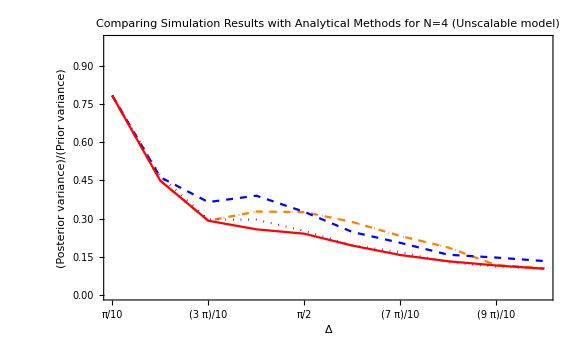

```mathematica
(*Needs to be 0.29662564242447337*)
```

```mathematica
(*(*Normalization term depending on the measurement outcome?*)
(*Normalizing the variance, each product normalizes 1 probability term in the product (of listOfPmϕ); e.g (1 /(r0s1^2+r1s1^2+r2s1^2)) normalizes Pm#ϕs1*)
NormalizationTerm=∏_(i=1)^2 1/(∑_(s=1)^(nph+1) (r[[i,s]])^2);
NormalizedBMSE = NormalizationTerm*BMSE/.AptStates;*)
```

#### Compare plots for N=4

```mathematica
MCA=MCAVaryΔ
```

{0.791559,0.446835,0.312248,0.287299,0.206233,0.134921,0.0910083,0.0672826,0.0779839,0.0485061}

```mathematica
MCA={0.7750201854703866,0.4942465681238499,0.3374615958772505,0.3452534692001444,0.2860898224128942,0.25007547813932435,0.17765369341379555,0.13153606847444343,0.11785530468575152,0.11670880858745618}
```

{0.77502,0.494247,0.337462,0.345253,0.28609,0.250075,0.177654,0.131536,0.117855,0.116709}

```mathematica
MCSA = {0.7837398433677253,0.4536090556738001,0.2739163064796318,0.2350774296474307,0.17770750155811743,0.14374881829066774,0.12245895320127148,0.10885047118339157,0.1044535037354056,0.08868957807323821}
```

{0.78374,0.453609,0.273916,0.235077,0.177708,0.143749,0.122459,0.10885,0.104454,0.0886896}

```mathematica
AnalyticA ={0.0064547614446658005,0.015362265800969058,0.02195683309461405,0.03891112854467223,0.051797884035783205,0.057654995088268504,0.06771113094186494,0.06721691385172052,0.07441611403221542,0.0842613968600595}
```

{0.00645476,0.0153623,0.0219568,0.0389111,0.0517979,0.057655,0.0677111,0.0672169,0.0744161,0.0842614}

```mathematica
AnalyticA=Table[AnalyticA[[n]]/((n π/10)^2/12),{n,1,10}]
```

{0.784805,0.466957,0.296626,0.295689,0.251915,0.194722,0.168014,0.127697,0.111703,0.10245}

```mathematica
AnalyticSA ={0.7832548199807943,0.4490954551497212,0.2916602859354953,0.3277416967803197,0.32562310100328096,0.2867386367203714,0.23189593990295326,0.18620363615424057,0.11710319710401186,0.10512412877158415}
```

{0.783255,0.449095,0.29166,0.327742,0.325623,0.286739,0.231896,0.186204,0.117103,0.105124}

```mathematica
OptimalSA = {0.7832548199808358,0.4490954551497609,0.29166028593618665,0.26058612809564585,0.2406540258448837,0.19393250958529862,0.1567902732388312,0.13218789349385024,0.11558869633632414,0.10285374254650627}
```

{0.783255,0.449095,0.29166,0.260586,0.240654,0.193933,0.15679,0.132188,0.115589,0.102854}

```mathematica
Listx = Table[{n,(n π)/10},{n,1,10}];
```

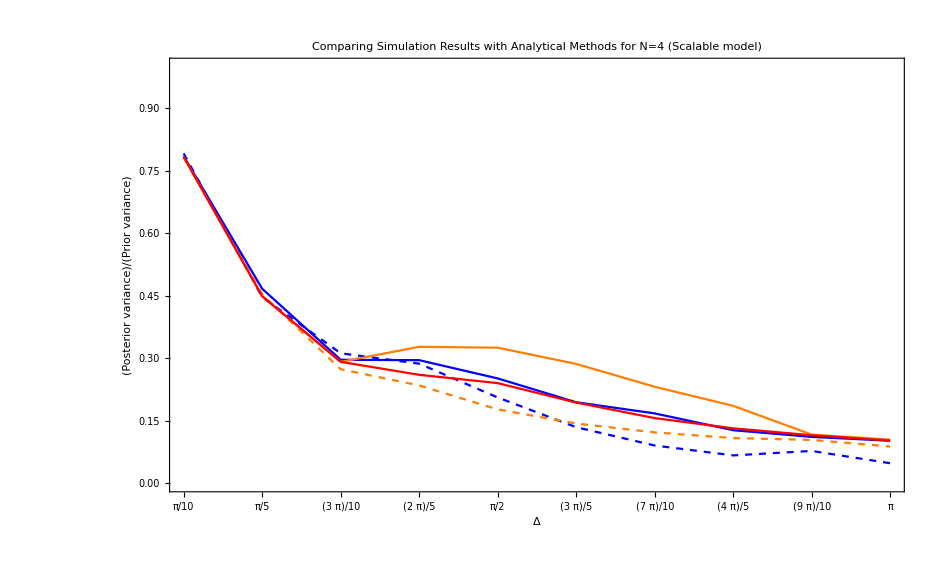

```mathematica
Show[ListLinePlot[MCA,PlotStyle->{Blue,Dashed},PlotLegends->Placed[{"MCA"},{Right,Top}]],ListLinePlot[MCSA,PlotStyle->{Orange,Dashed},PlotLegends->Placed[{"MCSA"},{Right,Top}]],ListLinePlot[AnalyticA,PlotStyle->{Blue},PlotLegends->Placed[{"Analytic Adaptive"},{Right,Top}]],ListLinePlot[AnalyticSA,PlotStyle->{Orange},PlotLegends->Placed[{"Analytic Semi-Adaptive"},{Right,Top}]],ListLinePlot[OptimalSA,PlotStyle->{Red},PlotLegends->Placed[{"Non-adaptive global"},{Right,Top}]],FrameLabel->{"Δ","(Posterior variance)/(Prior variance)"},PlotLabel-> "Comparing Simulation Results with Analytical Methods for N=4 (Scalable model)", PlotRange->{{1,10},{0,1}},Frame->True, FrameTicks->{{Automatic,Automatic},{Listx,Automatic}},ImageSize-> Large]
```

#### VarRatio MCSA, MCA with sbs optimal states plugged into global variance N=4, ns=2

```mathematica
(*Non-adaptive global*)
```

```mathematica
VRO4={0.7832548199809993,0.4490954551498136,0.29166028593590415,0.25787058571642585,0.24065402584283038,0.19393250958543157,0.15679027323873104,0.13218789349294494,0.11558869633651987,0.1028537425463464}
```

{0.783255,0.449095,0.29166,0.257871,0.240654,0.193933,0.15679,0.132188,0.115589,0.102854}

```mathematica
(*MonteCarlo Semi-Adaptive*)
```

```mathematica
MCSAPlugged={0.7832548199807943,0.44909545514972116,0.2916602859354953,0.3277416967803197,0.32562310100328096,0.28673863672037136,0.23189593990295332,0.18620363615424057,0.11710319710401186,0.10512412877158415}
```

{0.783255,0.449095,0.29166,0.327742,0.325623,0.286739,0.231896,0.186204,0.117103,0.105124}

```mathematica
(*Semi-adaptive*)
```

```mathematica
AnalyticSA={0.7832548199807943,0.4490954551497212,0.2916602859354953,0.3277416967803197,0.32562310100328096,0.2867386367203714,0.23189593990295326,0.18620363615424057,0.11710319710401186,0.10512412877158415}
```

{0.783255,0.449095,0.29166,0.327742,0.325623,0.286739,0.231896,0.186204,0.117103,0.105124}

```mathematica
(*MonteCarlo Adaptive 10 trials of 100 phitrue intervals (1000 total)*)
```

```mathematica
MCAPlugged10=MCAVaryΔ
```

{0.792134,0.479021,0.339269,0.263662,0.264563,0.182399,0.23943,0.0989743,0.0700832,0.0746591}

```mathematica
MCAPlugged100=MCAVaryΔ
```

{0.79585,0.465726,0.2893,0.276689,0.248536,0.183843,0.169411,0.10862,0.0881129,0.0772369}

```mathematica
MCAPlugged3=MCAVaryΔ
```

{0.798505,0.405386,0.225353,0.281024,0.263535,0.16197,0.157623,0.0834823,0.0734167,0.0614722}

```mathematica
(*Adaptive*)
```

```mathematica
AnalyticA ={0.7848048836429581,0.4669568863147173,0.29662564242447337,0.29568912007540094,0.2519147001923571,0.19472241150788455,0.16801400651733248,0.12769682385452574,0.11170264823418144,0.1024495735826159}
```

{0.784805,0.466957,0.296626,0.295689,0.251915,0.194722,0.168014,0.127697,0.111703,0.10245}

```mathematica
Listx = Table[{n,(n π)/10},{n,1,10}];
```

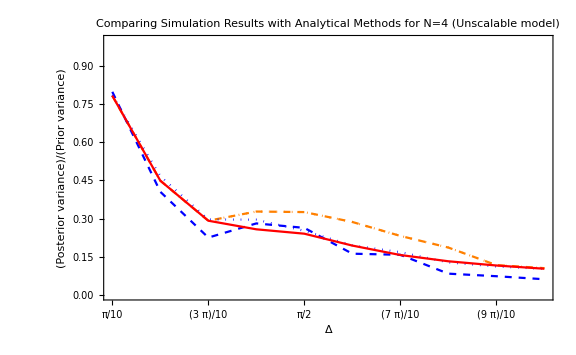

```mathematica
Show[ListLinePlot[MCSAPlugged,PlotStyle->{Orange,Dashed},PlotLegends->Placed[{"MCSA"},{Right,Top}]],ListLinePlot[AnalyticSA,PlotStyle->{Orange,Dotted},PlotLegends->Placed[{"Analytical semi adaptive"},{Right,Top}]],ListLinePlot[MCAPlugged3,PlotStyle->{Blue,Dashed},PlotLegends->Placed[{"MCA 3 trials of 100 phitrue intervals"},{Right,Top}]],ListLinePlot[AnalyticA,PlotStyle->{Blue,Dotted},PlotLegends->Placed[{"Analytical adaptive"},{Right,Top}]],ListLinePlot[VRO4,PlotStyle->{Red},PlotLegends->Placed[{"Non-adaptive global"},{Right,Top}]],FrameLabel->{"Δ","(Posterior variance)/(Prior variance)"},PlotLabel-> "Comparing Simulation Results with Analytical Methods for N=4 (Unscalable model)", PlotRange->{{1,10},{0,1}},Frame->True, FrameTicks->{{Automatic,Automatic},{Listx,Automatic}},ImageSize->Large]
```

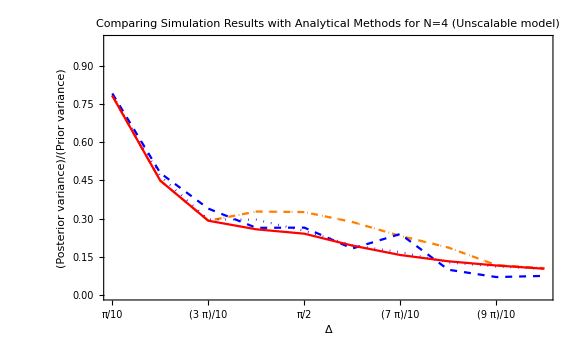

```mathematica
Show[ListLinePlot[MCSAPlugged,PlotStyle->{Orange,Dashed},PlotLegends->Placed[{"MCSA"},{Right,Top}]],ListLinePlot[AnalyticSA,PlotStyle->{Orange,Dotted},PlotLegends->Placed[{"Analytical semi adaptive"},{Right,Top}]],ListLinePlot[MCAPlugged10,PlotStyle->{Blue,Dashed},PlotLegends->Placed[{"MCA 10 trials of 100 phitrue intervals"},{Right,Top}]],ListLinePlot[AnalyticA,PlotStyle->{Blue,Dotted},PlotLegends->Placed[{"Analytical adaptive"},{Right,Top}]],ListLinePlot[VRO4,PlotStyle->{Red},PlotLegends->Placed[{"Non-adaptive global"},{Right,Top}]],FrameLabel->{"Δ","(Posterior variance)/(Prior variance)"},PlotLabel-> "Comparing Simulation Results with Analytical Methods for N=4 (Unscalable model)", PlotRange->{{1,10},{0,1}},Frame->True, FrameTicks->{{Automatic,Automatic},{Listx,Automatic}},ImageSize->Large]
```

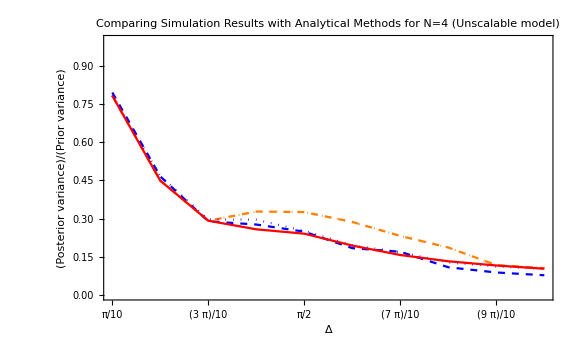

```mathematica
Show[ListLinePlot[MCSAPlugged,PlotStyle->{Orange,Dashed},PlotLegends->Placed[{"MCSA"},{Right,Top}]],ListLinePlot[AnalyticSA,PlotStyle->{Orange,Dotted},PlotLegends->Placed[{"Analytical semi adaptive"},{Right,Top}]],ListLinePlot[MCAPlugged100,PlotStyle->{Blue,Dashed},PlotLegends->Placed[{"MCA 100 trials of 100 phitrue intervals"},{Right,Top}]],ListLinePlot[AnalyticA,PlotStyle->{Blue,Dotted},PlotLegends->Placed[{"Analytical adaptive"},{Right,Top}]],ListLinePlot[VRO4,PlotStyle->{Red},PlotLegends->Placed[{"Non-adaptive global"},{Right,Top}]],FrameLabel->{"Δ","(Posterior variance)/(Prior variance)"},PlotLabel-> "Comparing Simulation Results with Analytical Methods for N=4 (Unscalable model)", PlotRange->{{1,10},{0,1}},Frame->True, FrameTicks->{{Automatic,Automatic},{Listx,Automatic}},ImageSize->Large]
```

```mathematica
Show[ListLinePlot[MCSAPlugged,PlotStyle->{Orange,Dashed},PlotLegends->Placed[{"MCSA"},{Right,Top}]],ListLinePlot[AnalyticSA,PlotStyle->{Orange,Dotted},PlotLegends->Placed[{"Analytical semi adaptive"},{Right,Top}]],ListLinePlot[MCAPlugged3,PlotStyle->{Blue,Dashed},PlotLegends->Placed[{"MCA 3 trials"},{Right,Top}]],ListLinePlot[AnalyticA,PlotStyle->{Blue,Dotted},PlotLegends->Placed[{"Analytical adaptive"},{Right,Top}]],ListLinePlot[VRO4,PlotStyle->{Red},PlotLegends->Placed[{"Non-adaptive global"},{Right,Top}]],FrameLabel->{"Δ","(Posterior variance)/(Prior variance)"},PlotLabel-> "Comparing Simulation Results with Analytical Methods for N=4 (Unscalable model)", PlotRange->{{1,10},{0,1}},Frame->True, FrameTicks->{{Automatic,Automatic},{Listx,Automatic}},ImageSize->Large]
```

-Graphics-

## D. Error Analysis for 100 trials of 30 shots of N=3

#### MC Adaptive Simulation after correction

```mathematica
MCAVaryΔ=Table[
ntrial=10;
MCATrial=Table[
(*Set the number of photons*)
nph=4;
(*Start with some (*interval [-Delta,Delta]*)*)
initInterval =n π/10;
GlobalVarianceA=GetVffExact[2,nph,initInterval];
VarRatio=Table[
(*Nature chooses the true value for the phase in the interval (unknown to the experimentalist)*)
ϕTrue =phitrue;
(*The experimentalist starts with center point Subscript[ϕ, 0]=0 and uncertainty Subscript[Δ, 0]=initInterval.*)
ϕtilde=0;
Δinit = initInterval;
nshots=30;
(*can variance and probability be calculated only once?*)
Clear[delta];
partialvariance=GetVariance[1,nph,delta];
(*The output is : {Subscript[P, 1] Subscript[(δϕ^2), 1],Subscript[P, 2] Subscript[(δϕ^2), 2],...}. Need to divide probability from variance*)
δϕsquared = Table[partialvariance[[n]]/Pm[[n]],{n,1,nph+1}];
phitilde=Table[
delta=Δinit;
(*list of P(m|ϕ) are the probabilities of getting outcome m*)
(*The experimentalist constructs an optimal one-shot input state for this uncertainty interval,*)
(*Plug N00N in N00N regime, Gaussian in Gaussian regime*)
If[Δinit*nph> 5,OptState=PlugGSBS[](*Print["Gaussian"];*),OptState=PlugN00NSBS[](*Print["N00N"];*)];
(*changed here*)
UnshiftedOptState=OptState;
Table[OptState[[1,n,2]] += n ϕtilde,{n,1,nph+1}];
(*The experimentalist makes measurements m with the following probabilities*)
(*P(m|ϕ)*)
prob=Re[listOfPmϕ/.OptState];
(*This is the probability distribution that nature has/knows*)
prob2=Re[listOfPmϕ/.UnshiftedOptState/.ϕ->(ϕTrue)];
probDistrib = Accumulate[prob2[[1]]];
(*mRand is a uniformly distributed random real between 0 and 1*)
SeedRandom[];
mRand=Random[];
(*if mRand<probDistrib[[m]], outcome m occured experimentally*)
outcomeOccured =Max[Table[If[mRand>probDistrib[[m]],m,0],{m,1,nph+1}]]+1;
(*changed here*)
Indvariance=δϕsquared/.OptState;
variance=Indvariance[[1,outcomeOccured]];
Δnext = √(12*variance);
(*varianceDistrib[[1,outcomeOccured]]*)
(*changed here*)
phaseEstimators=listOfϕ1/.OptState;
(*and the following phase estimator*)
ϕtilde+=phaseEstimators[[1,outcomeOccured]];
(*Input state of the second shot gets phase shifted by this phase above*)
Δinit=Δnext;
{variance,phitrue,ϕtilde,initInterval,OptState,outcomeOccured,Δnext,prob2}
,{shot,1, nshots}];
(*save the 2 shot outcomes*)
TwoShotOutcomesFixed={phitilde[[1,6]],phitilde[[2,6]]};
(*1st shot outcome*)
OutcomeOccured1stShot=phitilde[[1,6]];
(*For the first shot*)
Shot1AptStateList=phitilde[[1,5,1]];
Shot2AptStatetempList=phitilde[[2,5,1]];
(*rk here represents Subscript[r, k],magnitude of input state coefficient*)
r=Table[Table[Symbol["r"<>ToString[k]<>"s"<>ToString[l]<>"m"<>ToString[OutcomeOccured1stShot]],{k,0,nph}],{l,1,2}];
(*θk here represents Subscript[θ, k],real phase of input state coefficient(exponent)*)
θ=Table[Table[Symbol["θ"<>ToString[k]<>"s"<>ToString[l]<>"m"<>ToString[OutcomeOccured1stShot]],{k,0,nph}],{l,1,2}];
(*Change variable names for second shot*)
Shot2AptStateList=Flatten[Table[{θ[[2,n]]-> Shot2AptStatetempList[[n,2]],r[[2,n]]-> Shot2AptStatetempList[[n+nph+1,2]]},{n,1,nph+1}]];
(*Substitution list*)
AptStates = Join[Shot1AptStateList,Shot2AptStateList];
(*Calculate the average phase estimator after 100 trials of 2 shots*)
ϕm1m2=phitilde[[2,3]];
(*outcome, probability1, probability2*)
probability1= {phitilde[[1,8]],phitilde[[2,8]]};
(*1st shot probability*)
Probability1stshot=phitilde[[1,8]][[1,OutcomeOccured1stShot]];
(*Normalized variance*)
variance2=GlobalVarianceA[[OutcomeOccured1stShot]]/.AptStates;
normalizedvariance=variance2/Probability1stshot;
(*VarianceRatio*)
BMSERatio = normalizedvariance/(initInterval^2/12);
(*ϕTrue, probability of 1st shot outcomes, probability of 2nd shot outcomes, variance*)
{phitrue,probability1,variance2,OutcomeOccured1stShot,BMSERatio},{phitrue,-initInterval/2,initInterval/2,initInterval/100}];
PartialVariances=VarRatio[[All,3]];
normalizedPartialVariance=Mean[VarRatio[[All,5]]];
normalizedPartialVariance,{trial,1,ntrial}];
Mean[MCATrial],{n,1,10}];
```

```mathematica
{ntrial,nshots}
```

{100,10}

```mathematica
(*{ϕtrue, {{Δ,ϕ̃(after 100 shots for trial 1)} , {Δ,OverTilde[ϕ(after 100 shots for trial 2)]} ,...}}*)
```

```mathematica
MatrixForm[GridOfϕTrue]
```

(-1.5 | {{0.259422,-1.56755},{0.170769,-1.53043},{0.271216,-1.37799},{0.259422,-1.56755},{0.241567,-1.51471},{0.244883,-1.50077},{0.181929,-1.56945},{0.146673,-1.50745},{0.259422,-1.56755},{0.290194,-1.59249},{0.274245,-1.49436},{0.190061,-1.34446},{0.290194,-1.59249},{0.166957,-1.46304},{0.187729,-1.56312},{0.184236,-1.5571},{0.243105,-1.54192},{0.286202,-1.54655},{0.177968,-1.44128},{0.175476,-1.44597},{0.191006,-1.45365},{0.111064,-1.54124},{0.371124,-1.36025},{0.241567,-1.51471},{0.198265,-1.47236},{0.259422,-1.56755},{0.371124,-1.36025},{0.286202,-1.54655},{0.36165,-1.55259},{0.178774,-1.45618},{0.249928,-1.48689},{0.30896,-1.60556},{0.273312,-1.57996},{0.243105,-1.54192},{0.214821,-1.443},{0.174124,-1.39899},{0.243105,-1.54192},{0.169252,-1.54394},{0.187274,-1.49857},{0.270225,-1.4395},{0.108096,-1.50383},{0.240728,-1.52849},{0.286202,-1.54655},{0.262739,-1.46022},{0.19,-1.52481},{0.206195,-1.45763},{0.259422,-1.56755},{0.169285,-1.53947},{0.274245,-1.49436},{0.123062,-1.53012},{0.371124,-1.36025},{0.176918,-1.48372},{0.259422,-1.56755},{0.347032,-1.63539},{0.241567,-1.51471},{0.274245,-1.49436},{0.262739,-1.46022},{0.207996,-1.47019},{0.286202,-1.54655},{0.156723,-1.49429},{0.249265,-1.55492},{0.371124,-1.36025},{0.240728,-1.52849},{0.116285,-1.53784},{0.249928,-1.48689},{0.162653,-1.52294},{0.371124,-1.36025},{0.371124,-1.36025},{0.282146,-1.52714},{0.249265,-1.55492},{0.175948,-1.44864},{0.274245,-1.49436},{0.262739,-1.46022},{0.182246,-1.57549},{0.241567,-1.51471},{0.274245,-1.49436},{0.189864,-1.49187},{0.376517,-1.5311},{0.231707,-1.38377},{0.362628,-1.53661},{0.15412,-1.56288},{0.274245,-1.49436},{0.171418,-1.42885},{0.274245,-1.49436},{0.273312,-1.57996},{0.430113,-1.46431},{0.209458,-1.40527},{0.270225,-1.4395},{0.257117,-1.5449},{0.241567,-1.51471},{0.40046,-1.50591},{0.161172,-1.45906},{0.240728,-1.52849},{0.214821,-1.443},{0.16237,-1.49569},{0.159484,-1.48547},{0.286202,-1.54655},{0.249265,-1.55492},{0.380442,-1.52495},{0.128739,-1.51878}}
-1.2 | {{0.440047,-1.37243},{0.23917,-1.20804},{0.39683,-1.26798},{0.214284,-1.19965},{0.201577,-1.29653},{0.205924,-1.27631},{0.212768,-1.23093},{0.209748,-1.25222},{0.228657,-1.1913},{0.228051,-1.26419},{0.211663,-1.17747},{0.208838,-1.19889},{0.200106,-1.25815},{0.25135,-1.08747},{0.203713,-1.28297},{0.242777,-1.08397},{0.214563,-1.17133},{0.21228,-1.18521},{0.229283,-1.26653},{0.234403,-1.30026},{0.214849,-1.28531},{0.22849,-1.10849},{0.220199,-1.21001},{0.214296,-1.20462},{0.204632,-1.28885},{0.219389,-1.11811},{0.228042,-1.27778},{0.2154,-1.2959},{0.210983,-1.24873},{0.508979,-1.03738},{0.212616,-1.20518},{0.249826,-1.17101},{0.249942,-1.13997},{0.221483,-1.18942},{0.21199,-1.18914},{0.228136,-1.13378},{0.229327,-1.23276},{0.226738,-1.11171},{0.215047,-1.15017},{0.220307,-1.22793},{0.210787,-1.18875},{0.254194,-1.23935},{0.222455,-1.1951},{0.228935,-1.18022},{0.235967,-1.37175},{0.321374,-1.25118},{0.209874,-1.24264},{0.401248,-1.30854},{0.228517,-1.13532},{0.202125,-1.24336},{0.20544,-1.27434},{0.227709,-1.20403},{0.219428,-1.14814},{0.218024,-1.21609},{1.75729,-1.57414},{0.222861,-1.07453},{0.218128,-1.23659},{0.214374,-1.16125},{0.242171,-1.12068},{0.217016,-1.15915},{0.240781,-1.1987},{0.241176,-1.23744},{0.231896,-1.24303},{0.237233,-1.11222},{0.283048,-1.17456},{0.205526,-1.33828},{0.244125,-1.15238},{0.218943,-1.20738},{0.208093,-1.30648},{0.226305,-1.29088},{0.24377,-1.39371},{0.237402,-1.1921},{0.223598,-1.2729},{0.321541,-1.17243},{0.234748,-1.29275},{0.227433,-1.10465},{0.2168,-1.20286},{0.206542,-1.24336},{0.238394,-1.25318},{0.250928,-1.1228},{0.246947,-1.31281},{0.22355,-1.13206},{0.442008,-1.33105},{0.222302,-1.2165},{0.241678,-1.13854},{0.23877,-1.17571},{0.221242,-1.12155},{0.25365,-1.25345},{0.352909,-1.10979},{0.203009,-1.24286},{0.371124,-1.36025},{0.222381,-1.22329},{0.22424,-1.1931},{0.218758,-1.11851},{0.211391,-1.17624},{0.218781,-1.19379},{0.2357,-1.14797},{0.212008,-1.19168},{0.223837,-1.05423},{0.224728,-1.10472}}
-0.9 | {{0.459084,-0.818373},{0.229877,-1.00329},{0.227853,-0.908963},{0.235795,-0.822715},{0.228364,-0.865494},{0.217627,-0.931975},{0.222268,-0.926199},{0.22736,-0.939959},{0.226261,-0.91956},{0.209234,-0.887671},{0.222321,-0.93341},{0.222544,-0.920407},{0.218389,-0.810189},{0.228489,-0.988872},{0.222809,-0.883873},{0.212152,-0.781417},{0.234548,-0.801207},{0.2209,-0.847908},{0.200503,-0.838757},{0.211037,-0.843445},{0.228053,-0.935279},{0.236265,-0.929154},{0.213259,-0.923779},{0.303992,-0.751968},{0.296624,-0.909164},{1.80599,-1.55218},{0.238489,-0.953281},{0.217083,-0.847369},{0.221124,-0.945191},{0.226367,-1.02658},{0.226958,-0.880981},{0.234931,-0.866234},{0.219296,-0.912563},{0.209195,-0.848395},{0.256592,-0.849194},{0.21942,-0.990829},{0.226455,-0.989575},{0.441481,-0.487131},{0.24493,-0.880664},{0.22289,-1.02127},{0.632063,-0.567187},{0.239784,-1.00251},{0.250996,-0.84847},{0.236431,-0.881729},{0.211065,-0.809371},{0.223975,-0.90661},{0.213852,-0.88052},{0.230283,-0.925833},{0.228267,-0.971586},{0.222086,-0.887583},{0.217154,-0.905913},{0.273095,-0.867161},{0.258068,-0.902994},{0.239664,-1.00018},{0.220758,-0.895635},{0.212972,-0.809158},{0.232236,-0.838789},{0.236987,-0.996291},{0.239958,-0.827758},{0.212328,-0.805154},{0.274276,-0.815701},{0.216501,-0.885544},{0.259413,-0.91166},{0.215422,-0.948314},{0.205073,-0.872579},{0.223142,-0.9476},{0.855677,-0.59076},{0.228032,-0.991337},{0.229041,-0.929735},{0.257895,-0.858097},{0.210234,-0.8407},{0.211748,-0.894417},{0.226146,-1.05919},{0.218172,-0.911888},{0.220396,-0.98644},{0.503714,-0.616408},{0.210412,-0.776164},{0.244558,-1.02364},{0.223353,-0.9306},{0.207623,-0.842609},{0.222657,-0.849751},{0.19914,-0.788927},{0.217348,-0.948742},{0.219083,-0.838494},{0.241672,-0.855327},{0.660821,-0.929918},{0.213322,-0.813408},{0.236126,-0.970442},{0.228135,-0.96497},{0.215989,-0.959268},{0.211599,-0.826765},{0.202632,-0.835436},{0.225992,-0.913421},{0.214617,-0.943048},{0.230399,-0.908746},{0.233602,-1.02055},{0.240767,-0.897638},{0.218656,-0.812769},{0.202196,-0.805097},{2.67316,-1.57117}}
-0.6 | {{0.366604,-0.470567},{0.239256,-0.531261},{0.287226,-0.39736},{0.243556,-0.628764},{0.226034,-0.566417},{0.295331,-0.537968},{0.204462,-0.522613},{0.1877,-0.561372},{0.342728,-0.559225},{0.252192,-0.662089},{0.274104,-0.510901},{0.380746,-0.754946},{0.240542,-0.541978},{0.312209,-0.556801},{0.425497,-0.502107},{0.252192,-0.662089},{0.248932,-0.628801},{0.349861,-0.551082},{0.202813,-0.54342},{0.152223,-0.538315},{0.355313,-0.553744},{0.19534,-0.575721},{0.229006,-0.520735},{0.358263,-0.555542},{0.363767,-0.629228},{0.299341,-0.423672},{0.359517,-0.577425},{0.309307,-0.532975},{0.232924,-0.645812},{0.241683,-0.519155},{0.37143,-0.565821},{0.334653,-0.545152},{0.136342,-0.553647},{0.148665,-0.613754},{0.252813,-0.591895},{0.292318,-0.541979},{0.213424,-0.732598},{0.148755,-0.576168},{0.229403,-0.591342},{0.204841,-0.474687},{0.151457,-0.655373},{0.165194,-0.682589},{0.312209,-0.556801},{0.178843,-0.582976},{0.160136,-0.535155},{0.363767,-0.629228},{0.207433,-0.734265},{0.252047,-0.676171},{0.224911,-0.566476},{0.263047,-0.620309},{0.261248,-0.540493},{0.169628,-0.666569},{0.225026,-0.60023},{0.142514,-0.493217},{0.311103,-0.483068},{0.170897,-0.665149},{0.233357,-0.603975},{0.198495,-0.450751},{0.25269,-0.499078},{0.221358,-0.770102},{0.152483,-0.602002},{0.322371,-0.455184},{0.413819,-0.543418},{0.158167,-0.632268},{0.333231,-0.722268},{0.229188,-0.705681},{0.229403,-0.591342},{0.223486,-0.628628},{0.20332,-0.710306},{0.243556,-0.628764},{0.147386,-0.587104},{0.366604,-0.470567},{0.185641,-0.526797},{0.229006,-0.520735},{0.229188,-0.705681},{0.279108,-0.595339},{0.237455,-0.701567},{0.13179,-0.564156},{0.324205,-0.554229},{0.315285,-0.697367},{0.227698,-0.63371},{0.261248,-0.540493},{0.33373,-0.554388},{0.412935,-0.523702},{0.185058,-0.67232},{0.173491,-0.457217},{0.175453,-0.614455},{0.225984,-0.688423},{0.342056,-0.747031},{0.247623,-0.656222},{0.194912,-0.58539},{0.156193,-0.5124},{0.2504,-0.575732},{0.396443,-0.361485},{0.252281,-0.56872},{0.335287,-0.545657},{0.187479,-0.534454},{0.201264,-0.719289},{0.151486,-0.557945},{0.430073,-0.551091}}
-0.3 | {{0.179149,-0.318829},{0.368275,-0.345316},{0.222817,-0.283529},{0.209198,-0.236125},{0.263033,-0.301196},{0.235829,-0.393239},{0.215156,-0.205613},{0.376791,-0.293199},{0.4936,-0.282377},{0.20124,-0.296899},{0.185444,-0.385866},{0.195875,-0.408434},{0.251038,-0.452807},{0.237374,-0.279094},{0.233799,-0.324847},{0.214438,-0.310683},{0.257553,-0.328313},{0.299341,-0.423672},{0.281055,-0.205986},{0.518999,-0.447731},{0.187633,-0.295684},{0.227486,-0.227114},{0.33544,1.83079},{0.235857,-0.299492},{0.20718,-0.227046},{0.202292,-0.294469},{0.195379,-0.291306},{0.269795,-0.40631},{0.223673,-0.349956},{0.389864,1.69581},{0.285417,-0.168398},{0.251907,-0.351661},{0.226572,-0.320812},{0.219804,-0.352394},{0.432806,-0.476156},{0.257553,-0.328313},{0.265366,-0.24399},{0.19239,-0.283183},{0.231729,-0.311334},{0.260476,-0.310181},{0.226116,-0.346666},{0.218964,-0.213753},{0.262398,-0.247658},{0.217839,-0.354734},{0.208873,-0.276155},{0.248899,-0.221766},{0.255573,-0.334758},{0.211874,-0.133866},{0.224636,-0.326678},{0.201957,-0.229294},{0.214965,-0.371318},{0.256828,-0.336585},{0.298595,-0.358192},{0.233143,-0.51118},{0.549605,-0.566061},{0.259396,-0.291375},{0.203873,-0.264037},{0.298595,-0.358192},{0.20513,-0.274222},{0.196142,-0.338382},{0.575494,1.46809},{0.292086,-0.421898},{0.22881,-0.322542},{0.24948,-0.4151},{0.234983,-0.327192},{0.227221,-0.27368},{0.260592,-0.29345},{2.35969,-1.57078},{0.212961,-0.388773},{0.265909,-0.290643},{0.207211,-0.30771},{0.412837,-0.401845},{0.36372,-0.371519},{0.322141,1.79394},{0.2475,-0.246439},{0.20726,-0.311609},{0.194952,-0.289715},{0.271782,-0.272943},{0.322053,-0.393712},{0.19509,-0.378493},{0.217366,-0.263732},{0.205279,-0.210994},{0.21238,-0.196451},{0.246286,-0.302243},{0.309609,-0.248152},{0.192819,-0.320461},{0.231334,-0.237946},{0.24153,-0.260587},{0.215333,-0.27236},{0.44357,-0.409078},{0.237641,-0.423465},{0.297984,-0.436073},{0.316854,1.7708},{0.21685,-0.269008},{0.264023,-0.318041},{0.224831,-0.229696},{0.260092,-0.355585},{0.177095,-0.407795},{0.376791,-0.293199},{0.231374,-0.391817}}
0. | {{0.2187,0.0759964},{0.231542,0.0419473},{1.17287,-0.639839},{0.229755,-0.0891357},{0.754867,0.41375},{0.25151,0.00370823},{0.221458,0.0790956},{0.239893,-0.120015},{0.221736,0.0261314},{0.222191,0.101838},{0.227048,0.0236701},{0.217672,-0.155306},{0.223696,0.0147581},{10.7022,-1.58116},{0.225315,0.0128722},{0.229641,0.0231465},{0.224064,-0.0570208},{0.224564,0.00591521},{0.23104,0.0527707},{0.212482,0.154184},{0.226385,0.0381467},{0.220981,0.0510017},{0.222601,0.0588964},{0.223943,-0.0193187},{0.222355,0.0520064},{1.3734,-0.488618},{0.223918,0.0497293},{0.22385,-0.0280949},{0.224191,0.00850906},{0.230293,-0.0180126},{0.222883,-0.0369027},{0.223481,-0.0159906},{4.92895,1.55851},{0.224396,-0.103654},{0.226682,0.0746666},{0.26473,0.0100555},{0.362699,-1.92121},{0.223299,0.00561022},{0.223162,-0.00106132},{0.224073,0.0549883},{0.229308,-0.00670434},{0.240924,0.0268193},{0.219849,-0.0644146},{0.225589,-0.0642619},{0.224388,0.0147126},{0.331237,-0.0967327},{0.222971,-0.0360993},{0.218803,-0.08185},{0.221248,-0.0641491},{0.24294,-0.0580846},{0.225598,-0.00302997},{0.225624,0.0384244},{0.513758,-0.0061298},{0.223922,0.00166188},{0.222906,-0.0443518},{0.226658,-0.0478432},{0.223054,-0.00187432},{0.214216,-0.147563},{0.22694,0.0198065},{0.221747,0.03795},{0.222295,0.0258089},{0.231237,-0.0509414},{0.224418,-0.0197326},{0.221688,-0.0371147},{0.222379,0.0951488},{0.363972,1.83262},{0.227419,-0.00783707},{0.756532,-0.558758},{1.8342,-0.522254},{0.220575,0.0593285},{0.229465,0.109858},{0.344766,-0.198628},{0.237785,0.0778351},{0.222014,-0.0184593},{0.672501,-1.98434},{0.224082,0.0107191},{0.241686,-0.0202386},{0.223157,0.0304177},{0.952268,-0.598014},{0.230745,0.0110293},{0.222854,-0.00062802},{0.22258,-0.023424},{4.80446,-1.43143},{0.220399,-0.0592841},{0.228816,-0.0355669},{0.230587,0.0652376},{0.223555,0.0141844},{0.220262,0.0741256},{0.23233,-0.0307621},{0.225472,-0.014395},{0.222626,0.0151958},{0.223303,0.00259145},{0.227163,-0.0262317},{0.212395,-0.132677},{0.228442,-0.143288},{0.231377,-0.0994064},{0.226611,0.0274201},{0.224347,0.0696264},{0.218413,0.0870496},{0.361409,0.110816}}
0.3 | {{0.212234,0.34117},{0.298595,0.358192},{0.231142,0.260678},{0.21116,0.257424},{0.235038,0.293149},{0.194157,0.404039},{0.356775,0.395854},{0.196494,0.245332},{0.26287,0.232815},{0.246667,0.28166},{0.195025,0.276189},{0.376791,0.293199},{0.265252,0.288907},{0.203917,0.264287},{0.229194,0.254596},{0.220346,0.306983},{0.256997,0.321725},{0.238457,0.207643},{0.193839,0.315318},{0.220425,0.30016},{0.179992,0.301629},{0.233522,0.270751},{0.304986,0.208814},{0.208417,0.218637},{0.376791,0.293199},{0.191323,0.417777},{0.224749,0.282317},{0.24153,0.260587},{0.335859,0.437715},{0.223328,0.294155},{0.205238,0.257875},{0.198154,0.326952},{0.196669,0.303299},{0.299341,0.423672},{0.238147,0.20738},{0.20244,0.347178},{0.251795,0.376356},{0.534703,0.552193},{0.227313,0.401513},{0.210418,0.354144},{0.205729,0.287522},{0.449906,0.475913},{0.376791,0.293199},{0.181479,0.329046},{0.165722,0.424703},{0.238208,0.267477},{0.198005,0.316064},{0.257881,-1.58568},{0.211679,0.227054},{0.24948,0.350557},{0.258647,0.405334},{0.206041,0.280891},{0.384942,0.585318},{0.178928,0.326097},{0.259396,0.291375},{0.240311,0.376078},{0.206441,0.183701},{0.192297,0.345004},{0.196399,0.313073},{0.200957,0.278736},{0.202755,0.287445},{0.258248,0.247802},{0.329027,0.476827},{0.218326,0.304811},{0.405532,-1.80261},{0.234426,0.334791},{0.371943,0.567467},{0.191605,0.262347},{0.251795,0.376356},{0.204488,0.340344},{0.203235,0.243143},{0.395729,-1.87873},{0.21558,0.394137},{0.218522,0.28327},{0.299341,0.423672},{0.234588,0.292537},{0.209161,0.22898},{0.446091,0.304559},{0.21827,0.16034},{0.191984,0.246951},{0.213951,0.312784},{0.249652,0.242635},{0.255877,0.259477},{0.176024,0.317708},{0.221378,0.242105},{0.183348,0.273212},{0.235602,0.287147},{4.9847,1.57062},{0.237272,0.334301},{0.21274,0.138643},{0.249169,0.347417},{0.260158,0.249409},{0.201288,0.29361},{0.237488,0.27592},{0.231335,0.233022},{0.436367,0.498396},{0.193864,0.339793},{0.185048,0.290221},{0.302348,0.285259},{0.18654,0.281143}}
0.6 | {{0.130452,0.551177},{0.301365,0.500693},{0.160405,0.348942},{0.342056,0.747031},{0.348717,0.560567},{0.176857,0.639666},{0.293752,0.799843},{0.341468,0.691477},{0.378125,0.508558},{0.332033,0.524489},{0.389133,0.60128},{0.169115,0.589914},{0.355313,0.553744},{0.312209,0.556801},{0.22726,0.588366},{0.325962,0.501739},{0.238198,0.616505},{0.202919,0.691111},{0.162495,0.331381},{0.249618,0.550722},{0.261248,0.540493},{0.361143,0.495275},{0.318214,0.553058},{0.191978,0.625627},{0.438758,0.596927},{0.250779,0.670835},{0.233357,0.603975},{0.17451,0.512474},{0.188713,0.54416},{0.269795,0.40631},{0.151467,0.442864},{0.288192,0.646914},{0.253988,0.545555},{0.229403,0.591342},{0.286169,0.586148},{0.238286,0.532092},{0.148091,0.64839},{0.300215,0.666289},{0.159661,0.658753},{0.161516,0.502879},{0.199486,0.708102},{0.193219,0.685613},{0.172912,0.627381},{0.220319,0.625317},{0.21957,0.511485},{0.288774,0.658474},{0.334862,0.586503},{0.266203,0.720958},{0.061952,0.512641},{0.139173,0.607239},{0.148105,0.609679},{0.226793,0.578775},{0.183908,0.682694},{0.194115,0.667938},{0.257063,0.544672},{0.163163,0.4803},{0.335287,0.545657},{0.253166,0.513326},{0.248932,0.628801},{0.199812,0.5429},{0.421674,0.578601},{0.226795,0.548462},{0.335287,0.545657},{0.252813,0.591895},{0.271543,0.639736},{0.321348,0.733602},{0.146031,0.619636},{0.210608,0.674457},{0.229403,0.591342},{0.18213,0.536221},{0.226034,0.566417},{0.353377,0.590987},{0.187415,0.618834},{0.41032,0.571016},{0.249229,0.543895},{0.299341,0.423672},{0.300501,0.607706},{0.310478,0.561319},{0.366604,0.470567},{0.316091,0.509547},{2.55579,1.57071},{0.341418,0.555248},{0.300501,0.607706},{0.289104,0.572218},{0.206321,0.542176},{0.249618,0.550722},{0.298105,0.489635},{0.354328,0.47114},{0.229403,0.591342},{0.152339,0.588163},{0.19248,0.578644},{0.261284,0.556536},{0.238639,0.56952},{0.123671,0.516216},{0.266769,0.558328},{0.20071,0.554069},{0.32442,0.716884},{0.220712,0.605839},{0.27647,0.49694},{0.363767,0.629228}}
0.9 | {{1.26548,1.57013},{0.202701,0.800422},{0.209394,0.843016},{0.235355,0.787708},{0.227115,0.925277},{0.206954,0.885806},{0.213999,0.867159},{0.236219,0.94176},{0.236179,0.93325},{0.236729,0.86729},{0.209878,0.874547},{0.214,0.85181},{0.228058,1.01266},{0.224621,0.838827},{0.221598,0.964265},{0.226819,0.969149},{0.218802,0.89193},{0.23042,0.930353},{0.220665,0.941859},{0.353645,0.854555},{0.248628,0.800938},{0.217799,0.944272},{0.348691,0.513296},{0.238902,0.917949},{0.250669,0.883391},{0.238168,0.895157},{0.224927,0.903353},{0.248098,0.933219},{0.269757,0.917971},{0.218205,0.950949},{0.234959,0.915608},{0.223652,0.933589},{0.564371,0.550291},{0.209376,0.830601},{0.228828,0.911298},{0.218771,0.840283},{0.22748,0.84088},{0.220937,-1.19026},{0.246782,0.946523},{0.224434,0.923145},{0.228563,0.906682},{0.219232,0.971433},{0.227044,0.947688},{0.212897,0.894947},{0.209202,0.902121},{0.213297,0.86755},{0.239587,0.920815},{0.223368,0.882508},{0.224111,1.02156},{0.2213,0.944801},{0.232655,0.912913},{0.218459,0.950586},{0.223316,0.957094},{0.215023,0.918068},{0.220595,0.932374},{0.218035,0.954108},{0.222379,0.817489},{0.227926,0.808378},{0.222985,0.977749},{0.199575,0.774578},{0.23853,0.971765},{0.342056,0.747031},{0.268475,0.785815},{0.212545,0.860907},{0.208701,0.888489},{0.228913,0.941263},{0.236671,0.973034},{0.239804,0.814575},{0.226459,0.904209},{0.220902,0.890779},{0.224437,0.942549},{0.263401,0.943272},{0.232908,0.858617},{0.238555,0.737973},{0.207672,0.860423},{0.232391,0.8996},{0.221258,0.916113},{0.209343,0.883522},{0.236664,0.987398},{0.448029,0.710925},{0.242533,0.845649},{0.216253,0.886755},{0.217588,0.933587},{0.226972,0.94838},{0.221898,0.93806},{0.221176,0.915908},{0.224101,1.00748},{0.299417,0.888348},{0.21929,0.866948},{0.211158,0.814414},{0.221706,0.940568},{0.222016,0.821019},{0.231071,0.93291},{0.230549,0.885933},{0.300254,0.81724},{0.222774,0.904558},{0.332935,0.94545},{0.218013,0.876052},{0.235889,0.932393},{0.668042,0.731485}}
1.2 | {{0.234457,1.30958},{0.227099,1.18316},{0.218059,1.21986},{0.220037,1.20934},{0.210527,1.35252},{0.237483,1.2768},{0.243653,1.10489},{0.221503,1.00239},{0.213216,1.24342},{0.233394,1.2526},{0.205635,1.23577},{0.226463,1.24182},{0.248945,1.08683},{0.224994,1.24435},{0.246525,1.09426},{0.215036,1.19306},{0.236717,1.2843},{0.216787,1.14105},{0.2162,1.18932},{0.210366,1.23086},{0.915236,1.62781},{0.246632,1.20002},{0.219985,1.23453},{0.220696,1.26656},{0.250034,1.26491},{0.21583,1.24075},{0.23733,1.16149},{0.357796,1.22078},{0.207996,1.47019},{0.224409,1.0928},{0.218708,1.31947},{0.234958,1.20397},{0.228682,1.155},{0.201946,1.32122},{0.247163,1.28915},{0.223107,1.23861},{0.244163,1.15748},{0.218995,1.1575},{0.223634,1.19906},{0.224481,1.23998},{0.243403,1.32293},{0.245811,1.11783},{0.199201,1.27146},{0.200239,1.29602},{0.270185,1.12469},{0.230758,1.25475},{0.250628,1.31932},{0.223272,1.21074},{0.215066,1.20225},{0.265924,-0.909099},{0.222959,1.19373},{0.226999,1.18882},{0.21418,1.27102},{0.220772,1.21274},{0.240539,1.2586},{0.248441,1.29396},{0.21907,1.13026},{0.229896,1.09429},{0.265404,1.22421},{0.233425,1.11078},{0.569823,1.01952},{0.225282,1.14403},{0.234237,1.20995},{0.261468,1.17706},{0.211444,1.208},{0.237516,1.27802},{0.224285,1.30888},{0.246405,1.2674},{0.207862,1.2592},{0.234755,1.21552},{0.231625,1.17381},{0.217262,1.19729},{0.257234,1.135},{0.213298,1.23259},{0.225384,1.03274},{0.247347,1.11202},{0.23079,1.11884},{0.221123,1.26137},{0.577806,1.10346},{0.219663,1.10741},{0.212018,1.23061},{0.209681,1.21224},{0.24993,1.18904},{0.213772,1.24446},{0.239559,1.13314},{0.228286,1.16238},{0.230239,1.128},{0.222892,1.20242},{0.216443,1.2232},{0.255827,1.2376},{0.214199,1.23813},{0.227685,1.09005},{0.258061,1.22518},{0.229049,1.25934},{0.251655,1.14694},{0.225476,1.13452},{0.20437,1.21643},{0.224273,1.11171},{0.273528,1.23942},{0.234844,1.20235}}
1.5 | {{0.132219,1.49862},{0.181672,1.55099},{0.156048,1.51162},{0.241567,1.51471},{0.24377,1.39371},{0.181954,1.42157},{0.22521,1.40323},{0.131384,1.53115},{0.192264,1.50614},{0.192595,1.48524},{0.270225,1.4395},{0.371124,1.36025},{0.386647,1.52261},{0.363997,1.65314},{0.262739,1.46022},{0.244883,1.50077},{0.178826,1.46038},{0.241567,1.51471},{0.195411,1.47873},{0.175629,1.51688},{0.286202,1.54655},{0.40046,1.50591},{0.249265,1.55492},{0.182246,1.57549},{0.12525,1.50436},{0.328327,1.61968},{0.371124,1.36025},{0.290194,1.59249},{0.226685,1.35465},{0.181672,1.55099},{0.209437,1.44884},{0.239747,1.36137},{0.274245,1.49436},{0.184894,1.50531},{0.25605,1.47329},{0.155645,1.48855},{0.176675,1.46672},{0.170271,1.46941},{0.259422,1.56755},{0.223395,1.34377},{0.243105,1.54192},{0.142499,1.47896},{0.160016,1.47764},{0.249928,1.48689},{0.192136,1.56909},{0.290194,1.59249},{0.143247,1.47739},{0.209414,1.58713},{0.161408,1.45787},{0.270225,1.4395},{0.290194,1.59249},{0.371124,1.36025},{0.274245,1.49436},{0.371124,1.36025},{0.361657,1.5257},{0.160518,1.46125},{0.244883,1.50077},{0.350111,1.53986},{0.190739,1.51558},{0.244883,1.50077},{0.241567,1.51471},{0.371124,1.36025},{0.249265,1.55492},{0.270225,1.4395},{0.243105,1.54192},{0.206726,1.45439},{0.371124,1.36025},{0.184771,1.47869},{0.167964,1.43386},{0.355524,1.54515},{0.371124,1.36025},{0.244883,1.50077},{0.127114,1.47518},{0.181088,1.51877},{0.262739,1.46022},{0.262739,1.46022},{0.187274,1.49857},{0.244883,1.50077},{0.259231,1.60552},{0.249928,1.48689},{0.209411,1.44813},{0.274245,1.49436},{0.244883,1.50077},{0.249265,1.55492},{0.244883,1.50077},{0.179186,1.39832},{0.180367,1.45225},{0.0925276,1.53833},{0.286202,1.54655},{0.138966,1.53372},{0.249265,1.55492},{0.286202,1.54655},{0.240728,1.52849},{0.244883,1.50077},{0.126156,1.51095},{0.371124,1.36025},{0.262739,1.46022},{0.240728,1.52849},{0.209411,1.44813},{0.286202,1.54655}})

```mathematica
(*Mean of phase estimators over 10 trials*)
```

```mathematica
listOfMeanϕs=Table[{GridOfϕTrue[[m,1]],Mean[GridOfϕTrue[[m,2,All,2]]]},{m,1,Length[GridOfϕTrue]}]
```

{{-1.5,-1.50089},{-1.2,-1.21233},{-0.9,-0.897922},{-0.6,-0.583046},{-0.3,-0.229817},{0.,-0.0616155},{0.3,0.263742},{0.6,0.587077},{0.9,0.873291},{1.2,1.18736},{1.5,1.48973}}

```mathematica
(*Median of phase estimators over 10 trials - less effect of outliers*)
```

```mathematica
listOfMedianϕs=Table[{GridOfϕTrue[[m,1]],Median[GridOfϕTrue[[m,2,All,2]]]},{m,1,Length[GridOfϕTrue]}]
```

{{-1.5,-1.51471},{-1.2,-1.20433},{-0.9,-0.896636},{-0.6,-0.566446},{-0.3,-0.308946},{0.,-0.000844667},{0.3,0.293199},{0.6,0.57541},{0.9,0.903781},{1.2,1.21149},{1.5,1.50077}}

```mathematica
(*Squared error (SE) of the phase estimators from ϕtrue after 100 shots for 10 trials*)
```

```mathematica
listOfSEs=Table[Table[{GridOfϕTrue[[m,1]],(GridOfϕTrue[[m,2,n,2]]-GridOfϕTrue[[m,1]])^2},{n,1,ntrial}],{m,1,Length[GridOfϕTrue]}]
```

{{{-1.5,0.0045625},{-1.5,0.000926208},{-1.5,0.0148876},{-1.5,0.0045625},{-1.5,0.000216524},{-1.5,5.98248×10^-7},{-1.5,0.00482363},{-1.5,0.0000555511},{-1.5,0.0045625},{-1.5,0.0085542},{-1.5,0.0000317594},{-1.5,0.0241936},{-1.5,0.0085542},{-1.5,0.0013663},{-1.5,0.00398395},{-1.5,0.00326031},{-1.5,0.00175695},{-1.5,0.00216728},{-1.5,0.00344801},{-1.5,0.00291875},{-1.5,0.00214806},{-1.5,0.00170071},{-1.5,0.0195308},{-1.5,0.000216524},{-1.5,0.000763799},{-1.5,0.0045625},{-1.5,0.0195308},{-1.5,0.00216728},{-1.5,0.00276559},{-1.5,0.00192059},{-1.5,0.000171974},{-1.5,0.0111426},{-1.5,0.00639407},{-1.5,0.00175695},{-1.5,0.00324946},{-1.5,0.0102031},{-1.5,0.00175695},{-1.5,0.00193108},{-1.5,2.05007×10^-6},{-1.5,0.00365993},{-1.5,0.0000146333},{-1.5,0.000811452},{-1.5,0.00216728},{-1.5,0.00158248},{-1.5,0.000615377},{-1.5,0.00179518},{-1.5,0.0045625},{-1.5,0.00155823},{-1.5,0.0000317594},{-1.5,0.000907448},{-1.5,0.0195308},{-1.5,0.000265161},{-1.5,0.0045625},{-1.5,0.0183298},{-1.5,0.000216524},{-1.5,0.0000317594},{-1.5,0.00158248},{-1.5,0.000888747},{-1.5,0.00216728},{-1.5,0.0000326546},{-1.5,0.00301654},{-1.5,0.0195308},{-1.5,0.000811452},{-1.5,0.00143214},{-1.5,0.000171974},{-1.5,0.000526462},{-1.5,0.0195308},{-1.5,0.0195308},{-1.5,0.000736702},{-1.5,0.00301654},{-1.5,0.00263825},{-1.5,0.0000317594},{-1.5,0.00158248},{-1.5,0.00569945},{-1.5,0.000216524},{-1.5,0.0000317594},{-1.5,0.0000661325},{-1.5,0.000967359},{-1.5,0.013509},{-1.5,0.00134016},{-1.5,0.00395347},{-1.5,0.0000317594},{-1.5,0.00506217},{-1.5,0.0000317594},{-1.5,0.00639407},{-1.5,0.00127391},{-1.5,0.00897297},{-1.5,0.00365993},{-1.5,0.00201569},{-1.5,0.000216524},{-1.5,0.0000348728},{-1.5,0.00167589},{-1.5,0.000811452},{-1.5,0.00324946},{-1.5,0.0000185698},{-1.5,0.000211106},{-1.5,0.00216728},{-1.5,0.00301654},{-1.5,0.000622528},{-1.5,0.000352794}},{{-1.2,0.0297336},{-1.2,0.0000645873},{-1.2,0.00462114},{-1.2,1.22783×10^-7},{-1.2,0.00931721},{-1.2,0.00582388},{-1.2,0.000956586},{-1.2,0.00272714},{-1.2,0.0000757166},{-1.2,0.00412059},{-1.2,0.000507541},{-1.2,1.23827×10^-6},{-1.2,0.00338155},{-1.2,0.0126621},{-1.2,0.00688386},{-1.2,0.0134639},{-1.2,0.000821937},{-1.2,0.000218651},{-1.2,0.00442566},{-1.2,0.0100518},{-1.2,0.00727753},{-1.2,0.00837452},{-1.2,0.000100209},{-1.2,0.0000213782},{-1.2,0.00789385},{-1.2,0.00670523},{-1.2,0.00604915},{-1.2,0.00919613},{-1.2,0.00237444},{-1.2,0.0264464},{-1.2,0.000026785},{-1.2,0.000840393},{-1.2,0.00360412},{-1.2,0.000112019},{-1.2,0.000117998},{-1.2,0.00438486},{-1.2,0.00107332},{-1.2,0.0077955},{-1.2,0.00248298},{-1.2,0.00078033},{-1.2,0.000126547},{-1.2,0.00154865},{-1.2,0.0000239826},{-1.2,0.000391292},{-1.2,0.0294991},{-1.2,0.00261975},{-1.2,0.00181779},{-1.2,0.011781},{-1.2,0.004184},{-1.2,0.00188001},{-1.2,0.00552587},{-1.2,0.0000162229},{-1.2,0.00268931},{-1.2,0.000258902},{-1.2,0.139984},{-1.2,0.0157437},{-1.2,0.00133861},{-1.2,0.00150138},{-1.2,0.0062909},{-1.2,0.00166894},{-1.2,1.7006×10^-6},{-1.2,0.00140175},{-1.2,0.00185157},{-1.2,0.00770533},{-1.2,0.000647079},{-1.2,0.0191224},{-1.2,0.0022672},{-1.2,0.0000544618},{-1.2,0.0113389},{-1.2,0.0082583},{-1.2,0.0375248},{-1.2,0.0000624617},{-1.2,0.00531494},{-1.2,0.000760171},{-1.2,0.0086021},{-1.2,0.0090917},{-1.2,8.17094×10^-6},{-1.2,0.00188013},{-1.2,0.00282843},{-1.2,0.00595953},{-1.2,0.0127253},{-1.2,0.00461517},{-1.2,0.017174},{-1.2,0.000272137},{-1.2,0.00377793},{-1.2,0.00058983},{-1.2,0.00615441},{-1.2,0.00285724},{-1.2,0.00813823},{-1.2,0.00183676},{-1.2,0.0256792},{-1.2,0.000542513},{-1.2,0.0000475637},{-1.2,0.00664008},{-1.2,0.000564768},{-1.2,0.0000386086},{-1.2,0.0027074},{-1.2,0.0000691442},{-1.2,0.02125},{-1.2,0.00907796}},{{-0.9,0.00666301},{-0.9,0.0106688},{-0.9,0.0000803407},{-0.9,0.00597296},{-0.9,0.00119069},{-0.9,0.0010224},{-0.9,0.000686404},{-0.9,0.0015967},{-0.9,0.000382577},{-0.9,0.000151997},{-0.9,0.00111624},{-0.9,0.00041643},{-0.9,0.00806607},{-0.9,0.00789816},{-0.9,0.000260072},{-0.9,0.014062},{-0.9,0.00976007},{-0.9,0.00271357},{-0.9,0.00375076},{-0.9,0.0031985},{-0.9,0.00124462},{-0.9,0.000849972},{-0.9,0.000565427},{-0.9,0.0219134},{-0.9,0.0000839753},{-0.9,0.425344},{-0.9,0.00283891},{-0.9,0.00277003},{-0.9,0.00204227},{-0.9,0.0160218},{-0.9,0.000361719},{-0.9,0.00114014},{-0.9,0.000157832},{-0.9,0.00266305},{-0.9,0.00258124},{-0.9,0.00824997},{-0.9,0.00802374},{-0.9,0.170461},{-0.9,0.000373868},{-0.9,0.0147066},{-0.9,0.110765},{-0.9,0.010509},{-0.9,0.00265529},{-0.9,0.00033383},{-0.9,0.00821368},{-0.9,0.0000436943},{-0.9,0.000379484},{-0.9,0.000667351},{-0.9,0.00512458},{-0.9,0.00015417},{-0.9,0.0000349635},{-0.9,0.00107841},{-0.9,8.9646×10^-6},{-0.9,0.0100359},{-0.9,0.0000190563},{-0.9,0.00825223},{-0.9,0.00374681},{-0.9,0.00927203},{-0.9,0.00521886},{-0.9,0.00899575},{-0.9,0.00710634},{-0.9,0.000208974},{-0.9,0.000135954},{-0.9,0.00233427},{-0.9,0.000751902},{-0.9,0.00226575},{-0.9,0.0956294},{-0.9,0.00834244},{-0.9,0.000884176},{-0.9,0.00175587},{-0.9,0.00351651},{-0.9,0.000031174},{-0.9,0.0253417},{-0.9,0.000141317},{-0.9,0.00747193},{-0.9,0.0804244},{-0.9,0.0153354},{-0.9,0.0152859},{-0.9,0.000936381},{-0.9,0.00329376},{-0.9,0.002525},{-0.9,0.0123371},{-0.9,0.00237575},{-0.9,0.00378301},{-0.9,0.00199566},{-0.9,0.000895105},{-0.9,0.00749824},{-0.9,0.00496212},{-0.9,0.00422104},{-0.9,0.00351265},{-0.9,0.00536336},{-0.9,0.00416849},{-0.9,0.000180118},{-0.9,0.0018531},{-0.9,0.0000764847},{-0.9,0.0145325},{-0.9,5.58006×10^-6},{-0.9,0.0076092},{-0.9,0.00900657},{-0.9,0.450475}},{{-0.6,0.0167529},{-0.6,0.00472508},{-0.6,0.0410629},{-0.6,0.000827352},{-0.6,0.00112785},{-0.6,0.00384793},{-0.6,0.00598879},{-0.6,0.00149214},{-0.6,0.00166258},{-0.6,0.00385498},{-0.6,0.0079387},{-0.6,0.0240084},{-0.6,0.00336652},{-0.6,0.00186618},{-0.6,0.00958311},{-0.6,0.00385498},{-0.6,0.000829504},{-0.6,0.00239293},{-0.6,0.0032013},{-0.6,0.00380507},{-0.6,0.00213962},{-0.6,0.000589451},{-0.6,0.00628291},{-0.6,0.00197647},{-0.6,0.00085426},{-0.6,0.0310915},{-0.6,0.000509614},{-0.6,0.00449229},{-0.6,0.00209874},{-0.6,0.00653592},{-0.6,0.00116822},{-0.6,0.00300826},{-0.6,0.00214856},{-0.6,0.000189177},{-0.6,0.0000656887},{-0.6,0.00336644},{-0.6,0.0175822},{-0.6,0.000567952},{-0.6,0.0000749577},{-0.6,0.0157033},{-0.6,0.00306615},{-0.6,0.00682102},{-0.6,0.00186618},{-0.6,0.00028981},{-0.6,0.00420493},{-0.6,0.00085426},{-0.6,0.0180271},{-0.6,0.00580202},{-0.6,0.00112389},{-0.6,0.000412452},{-0.6,0.00354114},{-0.6,0.00443141},{-0.6,5.28319×10^-8},{-0.6,0.0114025},{-0.6,0.0136731},{-0.6,0.00424437},{-0.6,0.0000157981},{-0.6,0.0222751},{-0.6,0.0101852},{-0.6,0.0289346},{-0.6,4.00996×10^-6},{-0.6,0.0209716},{-0.6,0.00320157},{-0.6,0.0010412},{-0.6,0.0149495},{-0.6,0.0111684},{-0.6,0.0000749577},{-0.6,0.000819573},{-0.6,0.0121674},{-0.6,0.000827352},{-0.6,0.000166313},{-0.6,0.0167529},{-0.6,0.00535868},{-0.6,0.00628291},{-0.6,0.0111684},{-0.6,0.0000217239},{-0.6,0.0103158},{-0.6,0.00128482},{-0.6,0.00209501},{-0.6,0.00948025},{-0.6,0.00113638},{-0.6,0.00354114},{-0.6,0.00208047},{-0.6,0.00582136},{-0.6,0.00523017},{-0.6,0.0203869},{-0.6,0.000208935},{-0.6,0.00781867},{-0.6,0.021618},{-0.6,0.0031609},{-0.6,0.000213439},{-0.6,0.00767375},{-0.6,0.000588945},{-0.6,0.0568896},{-0.6,0.000978425},{-0.6,0.00295321},{-0.6,0.00429623},{-0.6,0.0142298},{-0.6,0.00176865},{-0.6,0.00239205}},{{-0.3,0.00035453},{-0.3,0.0020535},{-0.3,0.000271303},{-0.3,0.00408},{-0.3,1.42981×10^-6},{-0.3,0.00869354},{-0.3,0.00890897},{-0.3,0.0000462545},{-0.3,0.000310572},{-0.3,9.61917×10^-6},{-0.3,0.00737296},{-0.3,0.0117579},{-0.3,0.0233501},{-0.3,0.000437052},{-0.3,0.000617387},{-0.3,0.00011413},{-0.3,0.0008016},{-0.3,0.0152948},{-0.3,0.00883867},{-0.3,0.0218246},{-0.3,0.0000186277},{-0.3,0.0053123},{-0.3,4.54027},{-0.3,2.57895×10^-7},{-0.3,0.00532223},{-0.3,0.0000305933},{-0.3,0.0000755779},{-0.3,0.0113018},{-0.3,0.00249563},{-0.3,3.98326},{-0.3,0.0173192},{-0.3,0.00266884},{-0.3,0.000433149},{-0.3,0.00274515},{-0.3,0.031031},{-0.3,0.0008016},{-0.3,0.00313707},{-0.3,0.000282799},{-0.3,0.000128465},{-0.3,0.000103656},{-0.3,0.00217775},{-0.3,0.00743852},{-0.3,0.00273973},{-0.3,0.00299586},{-0.3,0.000568565},{-0.3,0.00612056},{-0.3,0.00120815},{-0.3,0.0276006},{-0.3,0.000711691},{-0.3,0.00499932},{-0.3,0.00508623},{-0.3,0.00133848},{-0.3,0.0033863},{-0.3,0.044597},{-0.3,0.0707883},{-0.3,0.0000743935},{-0.3,0.00129336},{-0.3,0.0033863},{-0.3,0.000664519},{-0.3,0.00147322},{-0.3,3.12613},{-0.3,0.0148591},{-0.3,0.000508158},{-0.3,0.0132479},{-0.3,0.000739423},{-0.3,0.000692755},{-0.3,0.0000428967},{-0.3,1.61488},{-0.3,0.00788066},{-0.3,0.0000875567},{-0.3,0.0000594498},{-0.3,0.0103725},{-0.3,0.00511491},{-0.3,4.38461},{-0.3,0.00286874},{-0.3,0.000134767},{-0.3,0.000105778},{-0.3,0.000732076},{-0.3,0.00878203},{-0.3,0.00616116},{-0.3,0.00131538},{-0.3,0.00792212},{-0.3,0.0107224},{-0.3,5.03245×10^-6},{-0.3,0.00268825},{-0.3,0.000418649},{-0.3,0.00385068},{-0.3,0.00155337},{-0.3,0.000763994},{-0.3,0.011898},{-0.3,0.0152436},{-0.3,0.0185159},{-0.3,4.28822},{-0.3,0.000960526},{-0.3,0.000325461},{-0.3,0.00494266},{-0.3,0.00308965},{-0.3,0.0116198},{-0.3,0.0000462545},{-0.3,0.00843042}},{{0.,0.00577546},{0.,0.00175958},{0.,0.409394},{0.,0.00794518},{0.,0.171189},{0.,0.000013751},{0.,0.00625612},{0.,0.0144037},{0.,0.000682852},{0.,0.0103709},{0.,0.000560272},{0.,0.0241198},{0.,0.0002178},{0.,2.50008},{0.,0.000165693},{0.,0.000535762},{0.,0.00325137},{0.,0.0000349898},{0.,0.00278474},{0.,0.0237727},{0.,0.00145517},{0.,0.00260118},{0.,0.00346878},{0.,0.000373211},{0.,0.00270466},{0.,0.238748},{0.,0.00247301},{0.,0.000789321},{0.,0.000072404},{0.,0.000324453},{0.,0.00136181},{0.,0.0002557},{0.,2.42896},{0.,0.0107442},{0.,0.0055751},{0.,0.000101113},{0.,3.69104},{0.,0.0000314746},{0.,1.12639×10^-6},{0.,0.00302372},{0.,0.0000449482},{0.,0.000719272},{0.,0.00414924},{0.,0.00412959},{0.,0.00021646},{0.,0.00935721},{0.,0.00130316},{0.,0.00669943},{0.,0.0041151},{0.,0.00337382},{0.,9.18073×10^-6},{0.,0.00147644},{0.,0.0000375744},{0.,2.76184×10^-6},{0.,0.00196708},{0.,0.00228897},{0.,3.51308×10^-6},{0.,0.0217749},{0.,0.000392298},{0.,0.00144021},{0.,0.000666102},{0.,0.00259503},{0.,0.000389377},{0.,0.0013775},{0.,0.0090533},{0.,3.35849},{0.,0.0000614196},{0.,0.312211},{0.,0.272749},{0.,0.00351987},{0.,0.0120688},{0.,0.0394533},{0.,0.00605831},{0.,0.000340745},{0.,3.93759},{0.,0.000114899},{0.,0.000409601},{0.,0.000925239},{0.,0.357621},{0.,0.000121647},{0.,3.94409×10^-7},{0.,0.000548682},{0.,2.04899},{0.,0.00351461},{0.,0.00126501},{0.,0.00425595},{0.,0.000201196},{0.,0.0054946},{0.,0.000946306},{0.,0.000207217},{0.,0.000230913},{0.,6.71564×10^-6},{0.,0.000688101},{0.,0.0176031},{0.,0.0205315},{0.,0.00988164},{0.,0.000751862},{0.,0.00484783},{0.,0.00757764},{0.,0.0122803}},{{0.3,0.00169493},{0.3,0.0033863},{0.3,0.00154624},{0.3,0.00181269},{0.3,0.0000469408},{0.3,0.010824},{0.3,0.00918801},{0.3,0.00298855},{0.3,0.00451377},{0.3,0.000336338},{0.3,0.000566958},{0.3,0.0000462545},{0.3,0.000123064},{0.3,0.0012754},{0.3,0.00206152},{0.3,0.0000487664},{0.3,0.000471961},{0.3,0.0085299},{0.3,0.000234649},{0.3,2.57396×10^-8},{0.3,2.6544×10^-6},{0.3,0.000855491},{0.3,0.00831485},{0.3,0.00661987},{0.3,0.0000462545},{0.3,0.0138714},{0.3,0.000312678},{0.3,0.00155337},{0.3,0.0189655},{0.3,0.0000341661},{0.3,0.00177449},{0.3,0.000726397},{0.3,0.0000108851},{0.3,0.0152948},{0.3,0.00857838},{0.3,0.00222573},{0.3,0.00583024},{0.3,0.0636014},{0.3,0.010305},{0.3,0.00293154},{0.3,0.000155705},{0.3,0.0309455},{0.3,0.0000462545},{0.3,0.000843645},{0.3,0.0155508},{0.3,0.00105774},{0.3,0.000258053},{0.3,3.5558},{0.3,0.00532107},{0.3,0.00255601},{0.3,0.0110953},{0.3,0.000365156},{0.3,0.0814066},{0.3,0.000681063},{0.3,0.0000743935},{0.3,0.00578793},{0.3,0.0135254},{0.3,0.00202534},{0.3,0.000170897},{0.3,0.000452163},{0.3,0.000157625},{0.3,0.00272462},{0.3,0.0312676},{0.3,0.0000231411},{0.3,4.42097},{0.3,0.00121041},{0.3,0.0715385},{0.3,0.00141773},{0.3,0.00583024},{0.3,0.00162762},{0.3,0.0032327},{0.3,4.74688},{0.3,0.00886172},{0.3,0.000279881},{0.3,0.0152948},{0.3,0.0000557029},{0.3,0.00504389},{0.3,0.0000207826},{0.3,0.0195048},{0.3,0.00281425},{0.3,0.000163442},{0.3,0.00329069},{0.3,0.00164209},{0.3,0.000313581},{0.3,0.00335188},{0.3,0.000717584},{0.3,0.000165197},{0.3,1.61447},{0.3,0.00117656},{0.3,0.026036},{0.3,0.00224833},{0.3,0.00255945},{0.3,0.0000408351},{0.3,0.000579853},{0.3,0.00448602},{0.3,0.0393611},{0.3,0.00158346},{0.3,0.0000956196},{0.3,0.000217304},{0.3,0.00035558}},{{0.6,0.00238372},{0.6,0.00986185},{0.6,0.06303},{0.6,0.021618},{0.6,0.00155493},{0.6,0.00157335},{0.6,0.0399373},{0.6,0.00836801},{0.6,0.00836155},{0.6,0.00570191},{0.6,1.63952×10^-6},{0.6,0.000101726},{0.6,0.00213962},{0.6,0.00186618},{0.6,0.000135341},{0.6,0.00965516},{0.6,0.000272417},{0.6,0.00830123},{0.6,0.0721562},{0.6,0.00242835},{0.6,0.00354114},{0.6,0.0109673},{0.6,0.00220353},{0.6,0.000656748},{0.6,9.44218×10^-6},{0.6,0.00501755},{0.6,0.0000157981},{0.6,0.00766086},{0.6,0.00311807},{0.6,0.0375158},{0.6,0.0246917},{0.6,0.00220089},{0.6,0.00296427},{0.6,0.0000749577},{0.6,0.000191876},{0.6,0.00461143},{0.6,0.00234154},{0.6,0.00439422},{0.6,0.00345193},{0.6,0.00943248},{0.6,0.011686},{0.6,0.00732955},{0.6,0.000749697},{0.6,0.000640935},{0.6,0.00783499},{0.6,0.00341925},{0.6,0.000182169},{0.6,0.0146309},{0.6,0.00763166},{0.6,0.000052406},{0.6,0.0000936907},{0.6,0.000450519},{0.6,0.00683836},{0.6,0.00461562},{0.6,0.00306116},{0.6,0.0143281},{0.6,0.00295321},{0.6,0.00751241},{0.6,0.000829504},{0.6,0.00326041},{0.6,0.0004579},{0.6,0.00265612},{0.6,0.00295321},{0.6,0.0000656887},{0.6,0.00157896},{0.6,0.0178494},{0.6,0.000385577},{0.6,0.00554377},{0.6,0.0000749577},{0.6,0.00406781},{0.6,0.00112785},{0.6,0.0000812312},{0.6,0.000354719},{0.6,0.000840089},{0.6,0.00314782},{0.6,0.0310915},{0.6,0.0000593782},{0.6,0.00149621},{0.6,0.0167529},{0.6,0.00818167},{0.6,0.942283},{0.6,0.00200277},{0.6,0.0000593782},{0.6,0.000771861},{0.6,0.00334358},{0.6,0.00242835},{0.6,0.0121804},{0.6,0.0166048},{0.6,0.0000749577},{0.6,0.000140111},{0.6,0.00045609},{0.6,0.00188909},{0.6,0.000929006},{0.6,0.00701975},{0.6,0.00173657},{0.6,0.00210964},{0.6,0.0136618},{0.6,0.0000340912},{0.6,0.0106213},{0.6,0.00085426}},{{0.9,0.449075},{0.9,0.00991586},{0.9,0.00324715},{0.9,0.0126095},{0.9,0.000638949},{0.9,0.000201479},{0.9,0.00107856},{0.9,0.00174387},{0.9,0.00110556},{0.9,0.00106993},{0.9,0.000647878},{0.9,0.00232226},{0.9,0.0126916},{0.9,0.00374211},{0.9,0.00412997},{0.9,0.00478153},{0.9,0.0000651234},{0.9,0.00092131},{0.9,0.0017522},{0.9,0.00206522},{0.9,0.00981319},{0.9,0.00196004},{0.9,0.14954},{0.9,0.00032216},{0.9,0.000275873},{0.9,0.0000234577},{0.9,0.0000112444},{0.9,0.00110352},{0.9,0.00032295},{0.9,0.00259579},{0.9,0.000243617},{0.9,0.00112822},{0.9,0.122296},{0.9,0.00481618},{0.9,0.000127654},{0.9,0.00356609},{0.9,0.00349515},{0.9,4.36918},{0.9,0.00216439},{0.9,0.00053568},{0.9,0.000044653},{0.9,0.00510262},{0.9,0.0022741},{0.9,0.0000255371},{0.9,4.49748×10^-6},{0.9,0.00105303},{0.9,0.000433256},{0.9,0.000305958},{0.9,0.0147765},{0.9,0.00200716},{0.9,0.00016674},{0.9,0.0025589},{0.9,0.00325974},{0.9,0.000326453},{0.9,0.00104811},{0.9,0.00292766},{0.9,0.00680809},{0.9,0.00839461},{0.9,0.00604498},{0.9,0.0157307},{0.9,0.00515015},{0.9,0.0233996},{0.9,0.0130382},{0.9,0.00152825},{0.9,0.000132512},{0.9,0.00170267},{0.9,0.00533399},{0.9,0.00729735},{0.9,0.0000177167},{0.9,0.0000850318},{0.9,0.00181046},{0.9,0.00187243},{0.9,0.00171258},{0.9,0.0262528},{0.9,0.00156638},{0.9,1.59845×10^-7},{0.9,0.000259622},{0.9,0.000271512},{0.9,0.0076385},{0.9,0.0357494},{0.9,0.002954},{0.9,0.000175442},{0.9,0.0011281},{0.9,0.00234067},{0.9,0.00144855},{0.9,0.000253071},{0.9,0.0115517},{0.9,0.000135763},{0.9,0.00109241},{0.9,0.00732498},{0.9,0.00164573},{0.9,0.00623796},{0.9,0.00108307},{0.9,0.000197893},{0.9,0.00684923},{0.9,0.0000207775},{0.9,0.00206569},{0.9,0.000573496},{0.9,0.00104929},{0.9,0.0283974}},{{1.2,0.0120085},{1.2,0.000283479},{1.2,0.000394248},{1.2,0.00008721},{1.2,0.0232638},{1.2,0.0058976},{1.2,0.0090467},{1.2,0.0390496},{1.2,0.00188551},{1.2,0.00276716},{1.2,0.00127967},{1.2,0.00174915},{1.2,0.012807},{1.2,0.00196729},{1.2,0.0111813},{1.2,0.0000482235},{1.2,0.00710573},{1.2,0.00347459},{1.2,0.000114049},{1.2,0.000952449},{1.2,0.183025},{1.2,5.99391×10^-10},{1.2,0.00119244},{1.2,0.00443046},{1.2,0.00421381},{1.2,0.0016606},{1.2,0.00148309},{1.2,0.000431932},{1.2,0.0730016},{1.2,0.0114916},{1.2,0.0142723},{1.2,0.0000157636},{1.2,0.00202514},{1.2,0.014695},{1.2,0.00794721},{1.2,0.00149088},{1.2,0.00180782},{1.2,0.00180594},{1.2,8.87278×10^-7},{1.2,0.00159814},{1.2,0.0151106},{1.2,0.0067527},{1.2,0.00510656},{1.2,0.00922079},{1.2,0.00567194},{1.2,0.00299736},{1.2,0.0142368},{1.2,0.000115387},{1.2,5.05207×10^-6},{1.2,4.4483},{1.2,0.0000392663},{1.2,0.000124885},{1.2,0.00504363},{1.2,0.000162209},{1.2,0.00343421},{1.2,0.00882881},{1.2,0.00486428},{1.2,0.0111748},{1.2,0.000586283},{1.2,0.00795998},{1.2,0.0325741},{1.2,0.00313301},{1.2,0.0000989219},{1.2,0.000526351},{1.2,0.0000639575},{1.2,0.00608649},{1.2,0.0118539},{1.2,0.00454294},{1.2,0.00350504},{1.2,0.000240997},{1.2,0.000685787},{1.2,7.32231×10^-6},{1.2,0.00422509},{1.2,0.0010624},{1.2,0.0279775},{1.2,0.00774047},{1.2,0.00658705},{1.2,0.00376634},{1.2,0.00932092},{1.2,0.00857317},{1.2,0.000936766},{1.2,0.000149716},{1.2,0.000120075},{1.2,0.00197678},{1.2,0.0044705},{1.2,0.00141541},{1.2,0.00518434},{1.2,5.83969×10^-6},{1.2,0.000538392},{1.2,0.00141399},{1.2,0.00145422},{1.2,0.0120899},{1.2,0.000634089},{1.2,0.00352163},{1.2,0.00281548},{1.2,0.00428809},{1.2,0.000269916},{1.2,0.00779593},{1.2,0.00155425},{1.2,5.51738×10^-6}},{{1.5,1.89776×10^-6},{1.5,0.00260038},{1.5,0.000134948},{1.5,0.000216524},{1.5,0.0112969},{1.5,0.00615127},{1.5,0.00936521},{1.5,0.000970538},{1.5,0.000037736},{1.5,0.000217734},{1.5,0.00365993},{1.5,0.0195308},{1.5,0.000511053},{1.5,0.0234516},{1.5,0.00158248},{1.5,5.98248×10^-7},{1.5,0.00157006},{1.5,0.000216524},{1.5,0.000452331},{1.5,0.000284843},{1.5,0.00216728},{1.5,0.0000348728},{1.5,0.00301654},{1.5,0.00569945},{1.5,0.0000189896},{1.5,0.0143238},{1.5,0.0195308},{1.5,0.0085542},{1.5,0.0211277},{1.5,0.00260038},{1.5,0.00261738},{1.5,0.019219},{1.5,0.0000317594},{1.5,0.0000281886},{1.5,0.000713274},{1.5,0.000131004},{1.5,0.00110781},{1.5,0.000935612},{1.5,0.0045625},{1.5,0.0244085},{1.5,0.00175695},{1.5,0.000442717},{1.5,0.000500088},{1.5,0.000171974},{1.5,0.00477337},{1.5,0.0085542},{1.5,0.000511119},{1.5,0.00759169},{1.5,0.00177495},{1.5,0.00365993},{1.5,0.0085542},{1.5,0.0195308},{1.5,0.0000317594},{1.5,0.0195308},{1.5,0.000660433},{1.5,0.00150167},{1.5,5.98248×10^-7},{1.5,0.00158903},{1.5,0.000242753},{1.5,5.98248×10^-7},{1.5,0.000216524},{1.5,0.0195308},{1.5,0.00301654},{1.5,0.00365993},{1.5,0.00175695},{1.5,0.00208064},{1.5,0.0195308},{1.5,0.000454313},{1.5,0.00437483},{1.5,0.00203814},{1.5,0.0195308},{1.5,5.98248×10^-7},{1.5,0.000616002},{1.5,0.000352318},{1.5,0.00158248},{1.5,0.00158248},{1.5,2.05007×10^-6},{1.5,5.98248×10^-7},{1.5,0.0111336},{1.5,0.000171974},{1.5,0.00269014},{1.5,0.0000317594},{1.5,5.98248×10^-7},{1.5,0.00301654},{1.5,5.98248×10^-7},{1.5,0.0103392},{1.5,0.00227961},{1.5,0.00146949},{1.5,0.00216728},{1.5,0.00113684},{1.5,0.00301654},{1.5,0.00216728},{1.5,0.000811452},{1.5,5.98248×10^-7},{1.5,0.000119935},{1.5,0.0195308},{1.5,0.00158248},{1.5,0.000811452},{1.5,0.00269014},{1.5,0.00216728}}}

```mathematica
(*Median absolute deviation from ϕtrue after 100 shots for 10 trials*)
```

```mathematica
listOfMADs=Table[Table[{GridOfϕTrue[[m,1]],Abs[GridOfϕTrue[[m,2,n,2]]-GridOfϕTrue[[m,1]]]},{n,1,ntrial}],{m,1,Length[GridOfϕTrue]}]
```

{{{-1.5,0.0675463},{-1.5,0.0304337},{-1.5,0.122015},{-1.5,0.0675463},{-1.5,0.0147147},{-1.5,0.000773465},{-1.5,0.0694523},{-1.5,0.00745326},{-1.5,0.0675463},{-1.5,0.0924889},{-1.5,0.00563554},{-1.5,0.155543},{-1.5,0.0924889},{-1.5,0.0369635},{-1.5,0.0631186},{-1.5,0.0570992},{-1.5,0.041916},{-1.5,0.0465541},{-1.5,0.0587198},{-1.5,0.0540254},{-1.5,0.0463471},{-1.5,0.0412397},{-1.5,0.139753},{-1.5,0.0147147},{-1.5,0.0276369},{-1.5,0.0675463},{-1.5,0.139753},{-1.5,0.0465541},{-1.5,0.0525889},{-1.5,0.0438245},{-1.5,0.0131139},{-1.5,0.105558},{-1.5,0.0799629},{-1.5,0.041916},{-1.5,0.0570041},{-1.5,0.10101},{-1.5,0.041916},{-1.5,0.0439441},{-1.5,0.00143181},{-1.5,0.0604973},{-1.5,0.00382535},{-1.5,0.028486},{-1.5,0.0465541},{-1.5,0.0397805},{-1.5,0.0248068},{-1.5,0.0423696},{-1.5,0.0675463},{-1.5,0.0394744},{-1.5,0.00563554},{-1.5,0.0301239},{-1.5,0.139753},{-1.5,0.0162838},{-1.5,0.0675463},{-1.5,0.135388},{-1.5,0.0147147},{-1.5,0.00563554},{-1.5,0.0397805},{-1.5,0.0298119},{-1.5,0.0465541},{-1.5,0.00571442},{-1.5,0.0549231},{-1.5,0.139753},{-1.5,0.028486},{-1.5,0.0378437},{-1.5,0.0131139},{-1.5,0.0229448},{-1.5,0.139753},{-1.5,0.139753},{-1.5,0.0271423},{-1.5,0.0549231},{-1.5,0.0513639},{-1.5,0.00563554},{-1.5,0.0397805},{-1.5,0.0754947},{-1.5,0.0147147},{-1.5,0.00563554},{-1.5,0.00813219},{-1.5,0.0311024},{-1.5,0.116228},{-1.5,0.0366082},{-1.5,0.0628766},{-1.5,0.00563554},{-1.5,0.0711489},{-1.5,0.00563554},{-1.5,0.0799629},{-1.5,0.0356919},{-1.5,0.0947258},{-1.5,0.0604973},{-1.5,0.0448965},{-1.5,0.0147147},{-1.5,0.00590532},{-1.5,0.0409376},{-1.5,0.028486},{-1.5,0.0570041},{-1.5,0.00430927},{-1.5,0.0145295},{-1.5,0.0465541},{-1.5,0.0549231},{-1.5,0.0249505},{-1.5,0.0187828}},{{-1.2,0.172434},{-1.2,0.00803662},{-1.2,0.067979},{-1.2,0.000350404},{-1.2,0.0965257},{-1.2,0.0763144},{-1.2,0.0309287},{-1.2,0.052222},{-1.2,0.00870153},{-1.2,0.0641918},{-1.2,0.0225287},{-1.2,0.00111278},{-1.2,0.0581511},{-1.2,0.112526},{-1.2,0.082969},{-1.2,0.116034},{-1.2,0.0286694},{-1.2,0.0147869},{-1.2,0.0665257},{-1.2,0.100259},{-1.2,0.0853084},{-1.2,0.0915124},{-1.2,0.0100104},{-1.2,0.00462365},{-1.2,0.0888473},{-1.2,0.0818855},{-1.2,0.0777763},{-1.2,0.0958965},{-1.2,0.0487283},{-1.2,0.162624},{-1.2,0.00517542},{-1.2,0.0289895},{-1.2,0.0600343},{-1.2,0.0105839},{-1.2,0.0108627},{-1.2,0.0662183},{-1.2,0.0327616},{-1.2,0.0882921},{-1.2,0.0498295},{-1.2,0.0279344},{-1.2,0.0112493},{-1.2,0.0393529},{-1.2,0.0048972},{-1.2,0.0197811},{-1.2,0.171753},{-1.2,0.0511835},{-1.2,0.0426356},{-1.2,0.10854},{-1.2,0.0646838},{-1.2,0.043359},{-1.2,0.0743362},{-1.2,0.00402777},{-1.2,0.0518586},{-1.2,0.0160904},{-1.2,0.374144},{-1.2,0.125474},{-1.2,0.036587},{-1.2,0.0387477},{-1.2,0.0793152},{-1.2,0.0408526},{-1.2,0.00130407},{-1.2,0.03744},{-1.2,0.0430299},{-1.2,0.08778},{-1.2,0.0254378},{-1.2,0.138284},{-1.2,0.0476152},{-1.2,0.00737982},{-1.2,0.106484},{-1.2,0.0908752},{-1.2,0.193713},{-1.2,0.00790327},{-1.2,0.0729036},{-1.2,0.0275712},{-1.2,0.0927475},{-1.2,0.0953504},{-1.2,0.00285849},{-1.2,0.0433605},{-1.2,0.053183},{-1.2,0.077198},{-1.2,0.112806},{-1.2,0.0679351},{-1.2,0.13105},{-1.2,0.0164966},{-1.2,0.0614649},{-1.2,0.0242864},{-1.2,0.0784501},{-1.2,0.0534531},{-1.2,0.0902122},{-1.2,0.0428574},{-1.2,0.160247},{-1.2,0.0232919},{-1.2,0.00689664},{-1.2,0.0814867},{-1.2,0.0237648},{-1.2,0.00621358},{-1.2,0.0520327},{-1.2,0.0083153},{-1.2,0.145774},{-1.2,0.0952783}},{{-0.9,0.0816273},{-0.9,0.10329},{-0.9,0.0089633},{-0.9,0.0772849},{-0.9,0.0345063},{-0.9,0.031975},{-0.9,0.0261993},{-0.9,0.0399587},{-0.9,0.0195596},{-0.9,0.0123287},{-0.9,0.0334102},{-0.9,0.0204066},{-0.9,0.0898113},{-0.9,0.0888716},{-0.9,0.0161267},{-0.9,0.118583},{-0.9,0.0987931},{-0.9,0.052092},{-0.9,0.0612435},{-0.9,0.0565553},{-0.9,0.0352792},{-0.9,0.0291543},{-0.9,0.0237787},{-0.9,0.148032},{-0.9,0.00916381},{-0.9,0.652184},{-0.9,0.0532814},{-0.9,0.0526311},{-0.9,0.0451915},{-0.9,0.126577},{-0.9,0.0190189},{-0.9,0.033766},{-0.9,0.0125631},{-0.9,0.0516048},{-0.9,0.0508059},{-0.9,0.0908293},{-0.9,0.0895754},{-0.9,0.412869},{-0.9,0.0193357},{-0.9,0.121271},{-0.9,0.332813},{-0.9,0.102513},{-0.9,0.0515295},{-0.9,0.018271},{-0.9,0.0906293},{-0.9,0.00661016},{-0.9,0.0194804},{-0.9,0.0258331},{-0.9,0.0715862},{-0.9,0.0124165},{-0.9,0.005913},{-0.9,0.0328391},{-0.9,0.00299409},{-0.9,0.100179},{-0.9,0.00436535},{-0.9,0.0908418},{-0.9,0.0612112},{-0.9,0.0962914},{-0.9,0.0722417},{-0.9,0.0948459},{-0.9,0.0842991},{-0.9,0.0144559},{-0.9,0.0116599},{-0.9,0.0483142},{-0.9,0.0274208},{-0.9,0.0475999},{-0.9,0.30924},{-0.9,0.091337},{-0.9,0.0297351},{-0.9,0.0419031},{-0.9,0.0593002},{-0.9,0.00558337},{-0.9,0.159191},{-0.9,0.0118877},{-0.9,0.0864403},{-0.9,0.283592},{-0.9,0.123836},{-0.9,0.123636},{-0.9,0.0306003},{-0.9,0.0573913},{-0.9,0.0502494},{-0.9,0.111073},{-0.9,0.0487417},{-0.9,0.0615062},{-0.9,0.0446728},{-0.9,0.0299183},{-0.9,0.0865924},{-0.9,0.0704423},{-0.9,0.0649696},{-0.9,0.0592676},{-0.9,0.073235},{-0.9,0.0645639},{-0.9,0.0134208},{-0.9,0.0430476},{-0.9,0.00874556},{-0.9,0.120551},{-0.9,0.00236222},{-0.9,0.0872307},{-0.9,0.0949029},{-0.9,0.671174}},{{-0.6,0.129433},{-0.6,0.0687392},{-0.6,0.20264},{-0.6,0.0287637},{-0.6,0.0335834},{-0.6,0.0620317},{-0.6,0.0773873},{-0.6,0.0386283},{-0.6,0.0407747},{-0.6,0.0620885},{-0.6,0.0890994},{-0.6,0.154946},{-0.6,0.0580217},{-0.6,0.0431992},{-0.6,0.0978934},{-0.6,0.0620885},{-0.6,0.0288011},{-0.6,0.0489176},{-0.6,0.0565801},{-0.6,0.0616852},{-0.6,0.0462561},{-0.6,0.0242786},{-0.6,0.0792648},{-0.6,0.0444576},{-0.6,0.0292277},{-0.6,0.176328},{-0.6,0.0225746},{-0.6,0.0670246},{-0.6,0.045812},{-0.6,0.080845},{-0.6,0.0341792},{-0.6,0.0548476},{-0.6,0.0463526},{-0.6,0.0137542},{-0.6,0.00810486},{-0.6,0.058021},{-0.6,0.132598},{-0.6,0.0238317},{-0.6,0.00865781},{-0.6,0.125313},{-0.6,0.0553728},{-0.6,0.0825894},{-0.6,0.0431992},{-0.6,0.0170238},{-0.6,0.0648454},{-0.6,0.0292277},{-0.6,0.134265},{-0.6,0.076171},{-0.6,0.0335245},{-0.6,0.0203089},{-0.6,0.0595075},{-0.6,0.0665688},{-0.6,0.000229852},{-0.6,0.106783},{-0.6,0.116932},{-0.6,0.0651488},{-0.6,0.00397469},{-0.6,0.149249},{-0.6,0.100922},{-0.6,0.170102},{-0.6,0.00200249},{-0.6,0.144816},{-0.6,0.0565824},{-0.6,0.0322676},{-0.6,0.122268},{-0.6,0.105681},{-0.6,0.00865781},{-0.6,0.0286282},{-0.6,0.110306},{-0.6,0.0287637},{-0.6,0.0128963},{-0.6,0.129433},{-0.6,0.073203},{-0.6,0.0792648},{-0.6,0.105681},{-0.6,0.00466089},{-0.6,0.101567},{-0.6,0.0358443},{-0.6,0.0457713},{-0.6,0.0973666},{-0.6,0.0337102},{-0.6,0.0595075},{-0.6,0.0456121},{-0.6,0.0762978},{-0.6,0.0723199},{-0.6,0.142783},{-0.6,0.0144546},{-0.6,0.0884233},{-0.6,0.147031},{-0.6,0.0562219},{-0.6,0.0146096},{-0.6,0.0875999},{-0.6,0.0242682},{-0.6,0.238515},{-0.6,0.0312798},{-0.6,0.0543434},{-0.6,0.0655456},{-0.6,0.119289},{-0.6,0.0420553},{-0.6,0.0489086}},{{-0.3,0.018829},{-0.3,0.0453156},{-0.3,0.0164713},{-0.3,0.0638749},{-0.3,0.00119575},{-0.3,0.0932391},{-0.3,0.0943873},{-0.3,0.00680107},{-0.3,0.0176231},{-0.3,0.00310148},{-0.3,0.0858659},{-0.3,0.108434},{-0.3,0.152807},{-0.3,0.0209058},{-0.3,0.0248473},{-0.3,0.0106831},{-0.3,0.0283125},{-0.3,0.123672},{-0.3,0.0940142},{-0.3,0.147731},{-0.3,0.00431598},{-0.3,0.0728855},{-0.3,2.13079},{-0.3,0.000507834},{-0.3,0.0729536},{-0.3,0.00553112},{-0.3,0.00869356},{-0.3,0.10631},{-0.3,0.0499563},{-0.3,1.99581},{-0.3,0.131602},{-0.3,0.0516609},{-0.3,0.0208122},{-0.3,0.0523942},{-0.3,0.176156},{-0.3,0.0283125},{-0.3,0.0560096},{-0.3,0.0168166},{-0.3,0.0113342},{-0.3,0.0101812},{-0.3,0.0466663},{-0.3,0.0862468},{-0.3,0.0523425},{-0.3,0.0547345},{-0.3,0.0238446},{-0.3,0.078234},{-0.3,0.0347585},{-0.3,0.166134},{-0.3,0.0266775},{-0.3,0.0707059},{-0.3,0.0713178},{-0.3,0.0365852},{-0.3,0.0581919},{-0.3,0.21118},{-0.3,0.266061},{-0.3,0.00862517},{-0.3,0.0359633},{-0.3,0.0581919},{-0.3,0.0257783},{-0.3,0.0383825},{-0.3,1.76809},{-0.3,0.121898},{-0.3,0.0225424},{-0.3,0.1151},{-0.3,0.0271923},{-0.3,0.0263202},{-0.3,0.00654956},{-0.3,1.27078},{-0.3,0.0887731},{-0.3,0.00935717},{-0.3,0.00771037},{-0.3,0.101845},{-0.3,0.0715186},{-0.3,2.09394},{-0.3,0.0535606},{-0.3,0.0116089},{-0.3,0.0102848},{-0.3,0.0270569},{-0.3,0.0937125},{-0.3,0.078493},{-0.3,0.0362682},{-0.3,0.0890063},{-0.3,0.103549},{-0.3,0.00224331},{-0.3,0.0518484},{-0.3,0.0204609},{-0.3,0.0620539},{-0.3,0.0394129},{-0.3,0.0276404},{-0.3,0.109078},{-0.3,0.123465},{-0.3,0.136073},{-0.3,2.0708},{-0.3,0.0309924},{-0.3,0.0180405},{-0.3,0.0703041},{-0.3,0.0555846},{-0.3,0.107795},{-0.3,0.00680107},{-0.3,0.0918173}},{{0.,0.0759964},{0.,0.0419473},{0.,0.639839},{0.,0.0891357},{0.,0.41375},{0.,0.00370823},{0.,0.0790956},{0.,0.120015},{0.,0.0261314},{0.,0.101838},{0.,0.0236701},{0.,0.155306},{0.,0.0147581},{0.,1.58116},{0.,0.0128722},{0.,0.0231465},{0.,0.0570208},{0.,0.00591521},{0.,0.0527707},{0.,0.154184},{0.,0.0381467},{0.,0.0510017},{0.,0.0588964},{0.,0.0193187},{0.,0.0520064},{0.,0.488618},{0.,0.0497293},{0.,0.0280949},{0.,0.00850906},{0.,0.0180126},{0.,0.0369027},{0.,0.0159906},{0.,1.55851},{0.,0.103654},{0.,0.0746666},{0.,0.0100555},{0.,1.92121},{0.,0.00561022},{0.,0.00106132},{0.,0.0549883},{0.,0.00670434},{0.,0.0268193},{0.,0.0644146},{0.,0.0642619},{0.,0.0147126},{0.,0.0967327},{0.,0.0360993},{0.,0.08185},{0.,0.0641491},{0.,0.0580846},{0.,0.00302997},{0.,0.0384244},{0.,0.0061298},{0.,0.00166188},{0.,0.0443518},{0.,0.0478432},{0.,0.00187432},{0.,0.147563},{0.,0.0198065},{0.,0.03795},{0.,0.0258089},{0.,0.0509414},{0.,0.0197326},{0.,0.0371147},{0.,0.0951488},{0.,1.83262},{0.,0.00783707},{0.,0.558758},{0.,0.522254},{0.,0.0593285},{0.,0.109858},{0.,0.198628},{0.,0.0778351},{0.,0.0184593},{0.,1.98434},{0.,0.0107191},{0.,0.0202386},{0.,0.0304177},{0.,0.598014},{0.,0.0110293},{0.,0.00062802},{0.,0.023424},{0.,1.43143},{0.,0.0592841},{0.,0.0355669},{0.,0.0652376},{0.,0.0141844},{0.,0.0741256},{0.,0.0307621},{0.,0.014395},{0.,0.0151958},{0.,0.00259145},{0.,0.0262317},{0.,0.132677},{0.,0.143288},{0.,0.0994064},{0.,0.0274201},{0.,0.0696264},{0.,0.0870496},{0.,0.110816}},{{0.3,0.0411696},{0.3,0.0581919},{0.3,0.0393222},{0.3,0.0425757},{0.3,0.00685134},{0.3,0.104039},{0.3,0.0958541},{0.3,0.0546676},{0.3,0.0671846},{0.3,0.0183395},{0.3,0.0238109},{0.3,0.00680107},{0.3,0.0110934},{0.3,0.0357127},{0.3,0.0454039},{0.3,0.00698329},{0.3,0.0217247},{0.3,0.0923575},{0.3,0.0153183},{0.3,0.000160436},{0.3,0.00162923},{0.3,0.0292488},{0.3,0.0911858},{0.3,0.0813626},{0.3,0.00680107},{0.3,0.117777},{0.3,0.0176827},{0.3,0.0394129},{0.3,0.137715},{0.3,0.00584518},{0.3,0.0421247},{0.3,0.0269518},{0.3,0.00329925},{0.3,0.123672},{0.3,0.0926195},{0.3,0.0471777},{0.3,0.076356},{0.3,0.252193},{0.3,0.101513},{0.3,0.0541437},{0.3,0.0124782},{0.3,0.175913},{0.3,0.00680107},{0.3,0.0290456},{0.3,0.124703},{0.3,0.032523},{0.3,0.016064},{0.3,1.88568},{0.3,0.0729457},{0.3,0.050557},{0.3,0.105334},{0.3,0.0191091},{0.3,0.285318},{0.3,0.0260972},{0.3,0.00862517},{0.3,0.0760784},{0.3,0.116299},{0.3,0.0450038},{0.3,0.0130727},{0.3,0.0212641},{0.3,0.0125549},{0.3,0.0521979},{0.3,0.176827},{0.3,0.00481052},{0.3,2.10261},{0.3,0.034791},{0.3,0.267467},{0.3,0.0376527},{0.3,0.076356},{0.3,0.0403438},{0.3,0.0568568},{0.3,2.17873},{0.3,0.0941367},{0.3,0.0167297},{0.3,0.123672},{0.3,0.00746343},{0.3,0.0710203},{0.3,0.00455879},{0.3,0.13966},{0.3,0.0530495},{0.3,0.0127845},{0.3,0.0573645},{0.3,0.0405227},{0.3,0.0177082},{0.3,0.0578954},{0.3,0.0267878},{0.3,0.0128529},{0.3,1.27062},{0.3,0.0343011},{0.3,0.161357},{0.3,0.0474165},{0.3,0.050591},{0.3,0.00639024},{0.3,0.0240801},{0.3,0.0669778},{0.3,0.198396},{0.3,0.0397927},{0.3,0.00977853},{0.3,0.0147412},{0.3,0.0188568}},{{0.6,0.0488233},{0.6,0.0993068},{0.6,0.251058},{0.6,0.147031},{0.6,0.0394327},{0.6,0.0396655},{0.6,0.199843},{0.6,0.0914769},{0.6,0.0914415},{0.6,0.075511},{0.6,0.00128044},{0.6,0.010086},{0.6,0.0462561},{0.6,0.0431992},{0.6,0.0116336},{0.6,0.0982607},{0.6,0.0165051},{0.6,0.0911111},{0.6,0.268619},{0.6,0.0492783},{0.6,0.0595075},{0.6,0.104725},{0.6,0.0469418},{0.6,0.0256271},{0.6,0.00307281},{0.6,0.0708347},{0.6,0.00397469},{0.6,0.0875263},{0.6,0.0558397},{0.6,0.19369},{0.6,0.157136},{0.6,0.0469137},{0.6,0.0544451},{0.6,0.00865781},{0.6,0.0138519},{0.6,0.0679075},{0.6,0.0483895},{0.6,0.0662889},{0.6,0.0587531},{0.6,0.097121},{0.6,0.108102},{0.6,0.0856128},{0.6,0.0273806},{0.6,0.0253167},{0.6,0.0885155},{0.6,0.0584743},{0.6,0.013497},{0.6,0.120958},{0.6,0.0873594},{0.6,0.0072392},{0.6,0.0096794},{0.6,0.0212254},{0.6,0.0826944},{0.6,0.0679383},{0.6,0.0553278},{0.6,0.1197},{0.6,0.0543434},{0.6,0.0866741},{0.6,0.0288011},{0.6,0.0571},{0.6,0.0213986},{0.6,0.0515375},{0.6,0.0543434},{0.6,0.00810486},{0.6,0.0397362},{0.6,0.133602},{0.6,0.0196361},{0.6,0.0744565},{0.6,0.00865781},{0.6,0.0637794},{0.6,0.0335834},{0.6,0.00901283},{0.6,0.018834},{0.6,0.0289843},{0.6,0.0561055},{0.6,0.176328},{0.6,0.00770573},{0.6,0.0386809},{0.6,0.129433},{0.6,0.0904526},{0.6,0.970713},{0.6,0.0447523},{0.6,0.00770573},{0.6,0.0277824},{0.6,0.0578237},{0.6,0.0492783},{0.6,0.110365},{0.6,0.12886},{0.6,0.00865781},{0.6,0.0118368},{0.6,0.0213563},{0.6,0.0434636},{0.6,0.0304796},{0.6,0.083784},{0.6,0.0416722},{0.6,0.0459308},{0.6,0.116884},{0.6,0.00583876},{0.6,0.10306},{0.6,0.0292277}},{{0.9,0.670131},{0.9,0.0995784},{0.9,0.0569838},{0.9,0.112292},{0.9,0.0252774},{0.9,0.0141943},{0.9,0.0328415},{0.9,0.0417597},{0.9,0.03325},{0.9,0.0327098},{0.9,0.0254535},{0.9,0.0481899},{0.9,0.112657},{0.9,0.0611728},{0.9,0.0642648},{0.9,0.0691486},{0.9,0.00806991},{0.9,0.0303531},{0.9,0.0418593},{0.9,0.0454447},{0.9,0.0990615},{0.9,0.0442724},{0.9,0.386704},{0.9,0.0179488},{0.9,0.0166094},{0.9,0.00484331},{0.9,0.00335327},{0.9,0.0332193},{0.9,0.0179708},{0.9,0.0509489},{0.9,0.0156082},{0.9,0.0335891},{0.9,0.349709},{0.9,0.0693987},{0.9,0.0112984},{0.9,0.0597167},{0.9,0.0591198},{0.9,2.09026},{0.9,0.046523},{0.9,0.0231448},{0.9,0.00668229},{0.9,0.0714326},{0.9,0.0476875},{0.9,0.00505343},{0.9,0.00212073},{0.9,0.0324504},{0.9,0.0208148},{0.9,0.0174917},{0.9,0.121558},{0.9,0.0448013},{0.9,0.0129128},{0.9,0.0505856},{0.9,0.0570941},{0.9,0.018068},{0.9,0.0323745},{0.9,0.0541078},{0.9,0.0825111},{0.9,0.0916221},{0.9,0.0777495},{0.9,0.125422},{0.9,0.0717645},{0.9,0.152969},{0.9,0.114185},{0.9,0.0390928},{0.9,0.0115114},{0.9,0.0412634},{0.9,0.0730342},{0.9,0.0854245},{0.9,0.00420913},{0.9,0.00922127},{0.9,0.0425495},{0.9,0.0432715},{0.9,0.0413833},{0.9,0.162027},{0.9,0.0395775},{0.9,0.000399807},{0.9,0.0161128},{0.9,0.0164776},{0.9,0.0873985},{0.9,0.189075},{0.9,0.0543507},{0.9,0.0132455},{0.9,0.0335872},{0.9,0.0483805},{0.9,0.0380598},{0.9,0.0159082},{0.9,0.107479},{0.9,0.0116517},{0.9,0.0330516},{0.9,0.0855861},{0.9,0.0405676},{0.9,0.0789808},{0.9,0.03291},{0.9,0.0140674},{0.9,0.0827601},{0.9,0.00455823},{0.9,0.0454498},{0.9,0.0239478},{0.9,0.0323928},{0.9,0.168515}},{{1.2,0.109583},{1.2,0.0168368},{1.2,0.0198557},{1.2,0.00933863},{1.2,0.152525},{1.2,0.0767958},{1.2,0.0951142},{1.2,0.19761},{1.2,0.0434224},{1.2,0.0526038},{1.2,0.0357724},{1.2,0.0418228},{1.2,0.113168},{1.2,0.0443541},{1.2,0.105742},{1.2,0.00694432},{1.2,0.0842955},{1.2,0.0589456},{1.2,0.0106794},{1.2,0.0308618},{1.2,0.427814},{1.2,0.0000244825},{1.2,0.0345317},{1.2,0.0665617},{1.2,0.0649139},{1.2,0.0407505},{1.2,0.0385109},{1.2,0.020783},{1.2,0.270188},{1.2,0.107199},{1.2,0.119467},{1.2,0.00397034},{1.2,0.0450015},{1.2,0.121223},{1.2,0.0891471},{1.2,0.038612},{1.2,0.0425184},{1.2,0.0424963},{1.2,0.000941955},{1.2,0.0399768},{1.2,0.122925},{1.2,0.0821748},{1.2,0.0714602},{1.2,0.096025},{1.2,0.0753123},{1.2,0.0547481},{1.2,0.119318},{1.2,0.0107418},{1.2,0.00224768},{1.2,2.1091},{1.2,0.00626628},{1.2,0.0111752},{1.2,0.0710185},{1.2,0.0127361},{1.2,0.0586022},{1.2,0.0939618},{1.2,0.0697444},{1.2,0.105711},{1.2,0.0242133},{1.2,0.0892187},{1.2,0.180483},{1.2,0.0559733},{1.2,0.00994595},{1.2,0.0229423},{1.2,0.00799734},{1.2,0.0780159},{1.2,0.108876},{1.2,0.0674014},{1.2,0.0592034},{1.2,0.0155241},{1.2,0.0261875},{1.2,0.00270598},{1.2,0.0650007},{1.2,0.0325946},{1.2,0.167265},{1.2,0.0879799},{1.2,0.0811607},{1.2,0.0613705},{1.2,0.0965449},{1.2,0.0925914},{1.2,0.0306066},{1.2,0.0122358},{1.2,0.0109579},{1.2,0.0444609},{1.2,0.0668618},{1.2,0.037622},{1.2,0.0720023},{1.2,0.00241654},{1.2,0.0232033},{1.2,0.0376031},{1.2,0.0381343},{1.2,0.109954},{1.2,0.0251811},{1.2,0.0593433},{1.2,0.0530611},{1.2,0.0654835},{1.2,0.0164291},{1.2,0.0882946},{1.2,0.0394239},{1.2,0.00234891}},{{1.5,0.00137759},{1.5,0.0509939},{1.5,0.0116167},{1.5,0.0147147},{1.5,0.106287},{1.5,0.07843},{1.5,0.096774},{1.5,0.0311535},{1.5,0.00614296},{1.5,0.0147558},{1.5,0.0604973},{1.5,0.139753},{1.5,0.0226065},{1.5,0.153139},{1.5,0.0397805},{1.5,0.000773465},{1.5,0.039624},{1.5,0.0147147},{1.5,0.0212681},{1.5,0.0168773},{1.5,0.0465541},{1.5,0.00590532},{1.5,0.0549231},{1.5,0.0754947},{1.5,0.0043577},{1.5,0.119682},{1.5,0.139753},{1.5,0.0924889},{1.5,0.145354},{1.5,0.0509939},{1.5,0.0511603},{1.5,0.138633},{1.5,0.00563554},{1.5,0.00530929},{1.5,0.0267072},{1.5,0.0114457},{1.5,0.0332838},{1.5,0.0305878},{1.5,0.0675463},{1.5,0.156232},{1.5,0.041916},{1.5,0.0210408},{1.5,0.0223627},{1.5,0.0131139},{1.5,0.0690895},{1.5,0.0924889},{1.5,0.0226079},{1.5,0.0871303},{1.5,0.0421302},{1.5,0.0604973},{1.5,0.0924889},{1.5,0.139753},{1.5,0.00563554},{1.5,0.139753},{1.5,0.0256989},{1.5,0.0387514},{1.5,0.000773465},{1.5,0.0398626},{1.5,0.0155805},{1.5,0.000773465},{1.5,0.0147147},{1.5,0.139753},{1.5,0.0549231},{1.5,0.0604973},{1.5,0.041916},{1.5,0.045614},{1.5,0.139753},{1.5,0.0213146},{1.5,0.0661425},{1.5,0.0451457},{1.5,0.139753},{1.5,0.000773465},{1.5,0.0248194},{1.5,0.0187701},{1.5,0.0397805},{1.5,0.0397805},{1.5,0.00143181},{1.5,0.000773465},{1.5,0.105516},{1.5,0.0131139},{1.5,0.0518665},{1.5,0.00563554},{1.5,0.000773465},{1.5,0.0549231},{1.5,0.000773465},{1.5,0.101682},{1.5,0.0477453},{1.5,0.0383339},{1.5,0.0465541},{1.5,0.0337171},{1.5,0.0549231},{1.5,0.0465541},{1.5,0.028486},{1.5,0.000773465},{1.5,0.0109515},{1.5,0.139753},{1.5,0.0397805},{1.5,0.028486},{1.5,0.0518665},{1.5,0.0465541}}}

```mathematica
(*MSE over 10 trials*)
```

```mathematica
Mean[listOfSEs[[1,All,2]]]
```

0.00390221

```mathematica
(*rms checks precision. small number => less statistical error*)
```

```mathematica
(*{phi_true, mean phase estimator, rmse} *)
```

```mathematica
Resultsmse=Table[{GridOfϕTrue[[m,1]],listOfMeanϕs[[m,2]],√Mean[listOfSEs[[m,All,2]]]},{m,1,Length[GridOfϕTrue]}]
```

{{-1.5,-1.50089,0.0624677},{-1.2,-1.21233,0.0826949},{-0.9,-0.897922,0.132519},{-0.6,-0.583046,0.082155},{-0.3,-0.229817,0.474353},{0.,-0.0616155,0.448292},{0.3,0.263742,0.387057},{0.6,0.587077,0.126514},{0.9,0.873291,0.233922},{1.2,1.18736,0.227923},{1.5,1.48973,0.0664924}}

```mathematica
Resultsmad=Table[{GridOfϕTrue[[m,1]],listOfMedianϕs[[m,2]],Median[listOfMADs[[m,All,2]]]},{m,1,Length[GridOfϕTrue]}]
```

{{-1.5,-1.51471,0.0421428},{-1.2,-1.20433,0.0521273},{-0.9,-0.896636,0.0523615},{-0.6,-0.566446,0.0580214},{-0.3,-0.308946,0.0523683},{0.,-0.000844667,0.0487863},{0.3,0.293199,0.0416471},{0.6,0.57541,0.0529405},{0.9,0.903781,0.0418095},{1.2,1.21149,0.0539046},{1.5,1.50077,0.0397805}}

```mathematica
(*print true if ϕtrue∈[Meanphase-rms,Meanphase+rmse]*)
```

```mathematica
(*Check if results are accurate. True=> no systematic error*)
```

```mathematica
Table[{Resultsmse[[m,1]],If[Resultsmse[[m,1]]>(Resultsmse[[m,2]]-Resultsmse[[m,3]]) && Resultsmse[[m,1]]<(Resultsmse[[m,2]]+Resultsmse[[m,3]]),True,False]},{m,1,Length[GridOfϕTrue]}]
```

{{-1.5,True},{-1.2,True},{-0.9,True},{-0.6,True},{-0.3,True},{0.,True},{0.3,True},{0.6,True},{0.9,True},{1.2,True},{1.5,True}}

```mathematica
Table[{Resultsmad[[m,1]],If[Resultsmad[[m,1]]>(Resultsmad[[m,2]]-Resultsmad[[m,3]]) && Resultsmad[[m,1]]<(Resultsmad[[m,2]]+Resultsmad[[m,3]]),True,False]},{m,1,Length[GridOfϕTrue]}]
```

{{-1.5,True},{-1.2,True},{-0.9,True},{-0.6,True},{-0.3,True},{0.,True},{0.3,True},{0.6,True},{0.9,True},{1.2,True},{1.5,True}}

```mathematica
(*Error plots*)
```

```mathematica
PlotResults=Table[Resultsmse[[m,1]],{m,1,Length[GridOfϕTrue]}]
```

{-1.5,-1.2,-0.9,-0.6,-0.3,0.,0.3,0.6,0.9,1.2,1.5}

```mathematica
PlotMAD=Table[Resultsmad[[m,3]],{m,1,Length[GridOfϕTrue]}]
```

{0.0421428,0.0521273,0.0523615,0.0580214,0.0523683,0.0487863,0.0416471,0.0529405,0.0418095,0.0539046,0.0397805}

```mathematica
PlotDevRMSE=Table[Around[Resultsmse[[m,2]],Resultsmse[[m,3]]],{m,1,Length[GridOfϕTrue]}]
```

{-1.500.06,-1.210.08,-0.900.13,-0.580.08,-0.20.5,0.00.4,0.30.4,0.590.13,0.870.23,1.190.23,1.490.07}

```mathematica
PlotDevMAD=Table[Around[Resultsmad[[m,2]],Resultsmad[[m,3]]],{m,1,Length[GridOfϕTrue]}]
```

{-1.510.04,-1.200.05,-0.900.05,-0.570.06,-0.310.05,0.000.05,0.290.04,0.580.05,0.900.04,1.210.05,1.500.04}

```mathematica
(*Mean +- RMSE*)
```

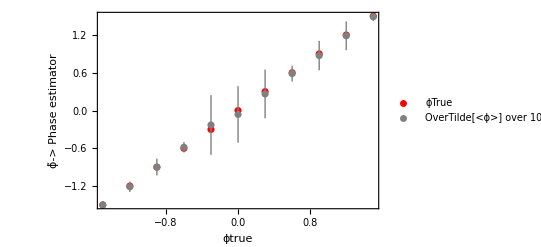

```mathematica
Show[ListPlot[Thread[{PlotResults,PlotResults}],PlotStyle->{Red,Thick},PlotLegends->{"ϕTrue"}],ListPlot[Thread[{PlotResults,PlotDevRMSE}],PlotStyle->{Gray}, PlotLegends->{"OverTilde[<ϕ>] over 100 trials ± RMSE"}], Frame->True,FrameTicks->Automatic,FrameLabel->{"ϕtrue",Style["ϕ̃-> Phase estimator",Thick]}]
```

```mathematica
(*Median +- MAD*)
```

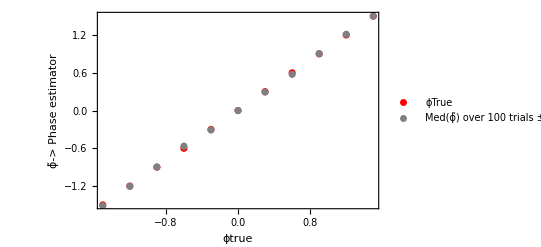

```mathematica
Show[ListPlot[Thread[{PlotResults,PlotResults}],PlotStyle->{Red,Thick},PlotLegends->{"ϕTrue"}],ListPlot[Thread[{PlotResults,PlotDevMAD}],PlotStyle->{Gray}, PlotLegends->{"Med(ϕ̃) over 100 trials ± MAD"}], Frame->True,FrameTicks->Automatic,FrameLabel->{"ϕtrue",Style["ϕ̃-> Phase estimator",Thick]}]
```

#### MC Adaptive Simulation

```mathematica
GridOfϕTrue=Table[
ntrial=100;
listOfPhaseEstimators=Table[
(*Set the number of photons*)
nph=3;
(*Start with some interval [-Delta,Delta]*)
initInterval =π;
(*Nature chooses the true value for the phase in the interval (unknown to the experimentalist)*)
ϕTrue =phitrue;
(*The experimentalist starts with center point Subscript[ϕ, 0]=0 and uncertainty Subscript[Δ, 0]=initInterval.*)
ϕtilde=0;
Δinit = initInterval;
nshots=30;
(*can variance and probability be calculated only once?*)
Clear[delta];
partialvariance=GetVariance[1,nph,delta];
(*The output is : {Subscript[P, 1] Subscript[(δϕ^2), 1],Subscript[P, 2] Subscript[(δϕ^2), 2],...}. Need to divide probability from variance*)
δϕsquared = Table[partialvariance[[n]]/Pm[[n]],{n,1,nph+1}];
phitilde=Table[
delta=Δinit;
(*list of P(m|ϕ) are the probabilities of getting outcome m*)
(*The experimentalist constructs an optimal one-shot input state for this uncertainty interval,*)
(*Plug N00N in N00N regime, Gaussian in Gaussian regime*)
If[Δinit*nph> 5,OptState=PlugGSBS[](*Print["Gaussian"];*),OptState=PlugN00NSBS[](*Print["N00N"];*)];
Table[OptState[[1,n,2]] += n ϕtilde,{n,1,nph+1}];
(*The experimentalist makes measurements m with the following probabilities*)
prob=Re[listOfPmϕ/.OptState];
(*This is the probability distribution that nature has/knows*)
prob2=Re[listOfPmϕ/.OptState/.ϕ->ϕTrue-ϕtilde];
probDistrib = Accumulate[prob2[[1]]];
(*mRand is a uniformly distributed random real between 0 and 1*)
SeedRandom[];
mRand=Random[];
(*if mRand<probDistrib[[m]], outcome m occured experimentally*)
outcomeOccured =Max[Table[If[mRand>probDistrib[[m]],m,0],{m,1,nph+1}]]+1;
Indvariance=δϕsquared/.OptState;
variance=Indvariance[[1,outcomeOccured]];
Δnext = √(12*variance);
(*varianceDistrib[[1,outcomeOccured]]*)
phaseEstimators=listOfϕ1/.OptState;
(*and the following phase estimator*)
ϕtilde+=phaseEstimators[[1,outcomeOccured]];
(*Input state of the second shot gets phase shifted by this phase above*)
Δinit=Δnext;
Δnext
,{shot,1, nshots}];
{Δnext,ϕtilde},{trial,1,ntrial}];
(*finds the mean of the varRatio over ntrials for a particular Δini*)
{ϕTrue,listOfPhaseEstimators},{phitrue,-1.5,1.5,0.3}];
```

```mathematica
{ntrial,nshots}
```

{100,10}

```mathematica
(*{ϕtrue, {{Δ,ϕ̃(after 100 shots for trial 1)} , {Δ,OverTilde[ϕ(after 100 shots for trial 2)]} ,...}}*)
```

```mathematica
MatrixForm[GridOfϕTrue]
```

(-1.5 | {{0.259422,-1.56755},{0.170769,-1.53043},{0.271216,-1.37799},{0.259422,-1.56755},{0.241567,-1.51471},{0.244883,-1.50077},{0.181929,-1.56945},{0.146673,-1.50745},{0.259422,-1.56755},{0.290194,-1.59249},{0.274245,-1.49436},{0.190061,-1.34446},{0.290194,-1.59249},{0.166957,-1.46304},{0.187729,-1.56312},{0.184236,-1.5571},{0.243105,-1.54192},{0.286202,-1.54655},{0.177968,-1.44128},{0.175476,-1.44597},{0.191006,-1.45365},{0.111064,-1.54124},{0.371124,-1.36025},{0.241567,-1.51471},{0.198265,-1.47236},{0.259422,-1.56755},{0.371124,-1.36025},{0.286202,-1.54655},{0.36165,-1.55259},{0.178774,-1.45618},{0.249928,-1.48689},{0.30896,-1.60556},{0.273312,-1.57996},{0.243105,-1.54192},{0.214821,-1.443},{0.174124,-1.39899},{0.243105,-1.54192},{0.169252,-1.54394},{0.187274,-1.49857},{0.270225,-1.4395},{0.108096,-1.50383},{0.240728,-1.52849},{0.286202,-1.54655},{0.262739,-1.46022},{0.19,-1.52481},{0.206195,-1.45763},{0.259422,-1.56755},{0.169285,-1.53947},{0.274245,-1.49436},{0.123062,-1.53012},{0.371124,-1.36025},{0.176918,-1.48372},{0.259422,-1.56755},{0.347032,-1.63539},{0.241567,-1.51471},{0.274245,-1.49436},{0.262739,-1.46022},{0.207996,-1.47019},{0.286202,-1.54655},{0.156723,-1.49429},{0.249265,-1.55492},{0.371124,-1.36025},{0.240728,-1.52849},{0.116285,-1.53784},{0.249928,-1.48689},{0.162653,-1.52294},{0.371124,-1.36025},{0.371124,-1.36025},{0.282146,-1.52714},{0.249265,-1.55492},{0.175948,-1.44864},{0.274245,-1.49436},{0.262739,-1.46022},{0.182246,-1.57549},{0.241567,-1.51471},{0.274245,-1.49436},{0.189864,-1.49187},{0.376517,-1.5311},{0.231707,-1.38377},{0.362628,-1.53661},{0.15412,-1.56288},{0.274245,-1.49436},{0.171418,-1.42885},{0.274245,-1.49436},{0.273312,-1.57996},{0.430113,-1.46431},{0.209458,-1.40527},{0.270225,-1.4395},{0.257117,-1.5449},{0.241567,-1.51471},{0.40046,-1.50591},{0.161172,-1.45906},{0.240728,-1.52849},{0.214821,-1.443},{0.16237,-1.49569},{0.159484,-1.48547},{0.286202,-1.54655},{0.249265,-1.55492},{0.380442,-1.52495},{0.128739,-1.51878}}
-1.2 | {{0.440047,-1.37243},{0.23917,-1.20804},{0.39683,-1.26798},{0.214284,-1.19965},{0.201577,-1.29653},{0.205924,-1.27631},{0.212768,-1.23093},{0.209748,-1.25222},{0.228657,-1.1913},{0.228051,-1.26419},{0.211663,-1.17747},{0.208838,-1.19889},{0.200106,-1.25815},{0.25135,-1.08747},{0.203713,-1.28297},{0.242777,-1.08397},{0.214563,-1.17133},{0.21228,-1.18521},{0.229283,-1.26653},{0.234403,-1.30026},{0.214849,-1.28531},{0.22849,-1.10849},{0.220199,-1.21001},{0.214296,-1.20462},{0.204632,-1.28885},{0.219389,-1.11811},{0.228042,-1.27778},{0.2154,-1.2959},{0.210983,-1.24873},{0.508979,-1.03738},{0.212616,-1.20518},{0.249826,-1.17101},{0.249942,-1.13997},{0.221483,-1.18942},{0.21199,-1.18914},{0.228136,-1.13378},{0.229327,-1.23276},{0.226738,-1.11171},{0.215047,-1.15017},{0.220307,-1.22793},{0.210787,-1.18875},{0.254194,-1.23935},{0.222455,-1.1951},{0.228935,-1.18022},{0.235967,-1.37175},{0.321374,-1.25118},{0.209874,-1.24264},{0.401248,-1.30854},{0.228517,-1.13532},{0.202125,-1.24336},{0.20544,-1.27434},{0.227709,-1.20403},{0.219428,-1.14814},{0.218024,-1.21609},{1.75729,-1.57414},{0.222861,-1.07453},{0.218128,-1.23659},{0.214374,-1.16125},{0.242171,-1.12068},{0.217016,-1.15915},{0.240781,-1.1987},{0.241176,-1.23744},{0.231896,-1.24303},{0.237233,-1.11222},{0.283048,-1.17456},{0.205526,-1.33828},{0.244125,-1.15238},{0.218943,-1.20738},{0.208093,-1.30648},{0.226305,-1.29088},{0.24377,-1.39371},{0.237402,-1.1921},{0.223598,-1.2729},{0.321541,-1.17243},{0.234748,-1.29275},{0.227433,-1.10465},{0.2168,-1.20286},{0.206542,-1.24336},{0.238394,-1.25318},{0.250928,-1.1228},{0.246947,-1.31281},{0.22355,-1.13206},{0.442008,-1.33105},{0.222302,-1.2165},{0.241678,-1.13854},{0.23877,-1.17571},{0.221242,-1.12155},{0.25365,-1.25345},{0.352909,-1.10979},{0.203009,-1.24286},{0.371124,-1.36025},{0.222381,-1.22329},{0.22424,-1.1931},{0.218758,-1.11851},{0.211391,-1.17624},{0.218781,-1.19379},{0.2357,-1.14797},{0.212008,-1.19168},{0.223837,-1.05423},{0.224728,-1.10472}}
-0.9 | {{0.459084,-0.818373},{0.229877,-1.00329},{0.227853,-0.908963},{0.235795,-0.822715},{0.228364,-0.865494},{0.217627,-0.931975},{0.222268,-0.926199},{0.22736,-0.939959},{0.226261,-0.91956},{0.209234,-0.887671},{0.222321,-0.93341},{0.222544,-0.920407},{0.218389,-0.810189},{0.228489,-0.988872},{0.222809,-0.883873},{0.212152,-0.781417},{0.234548,-0.801207},{0.2209,-0.847908},{0.200503,-0.838757},{0.211037,-0.843445},{0.228053,-0.935279},{0.236265,-0.929154},{0.213259,-0.923779},{0.303992,-0.751968},{0.296624,-0.909164},{1.80599,-1.55218},{0.238489,-0.953281},{0.217083,-0.847369},{0.221124,-0.945191},{0.226367,-1.02658},{0.226958,-0.880981},{0.234931,-0.866234},{0.219296,-0.912563},{0.209195,-0.848395},{0.256592,-0.849194},{0.21942,-0.990829},{0.226455,-0.989575},{0.441481,-0.487131},{0.24493,-0.880664},{0.22289,-1.02127},{0.632063,-0.567187},{0.239784,-1.00251},{0.250996,-0.84847},{0.236431,-0.881729},{0.211065,-0.809371},{0.223975,-0.90661},{0.213852,-0.88052},{0.230283,-0.925833},{0.228267,-0.971586},{0.222086,-0.887583},{0.217154,-0.905913},{0.273095,-0.867161},{0.258068,-0.902994},{0.239664,-1.00018},{0.220758,-0.895635},{0.212972,-0.809158},{0.232236,-0.838789},{0.236987,-0.996291},{0.239958,-0.827758},{0.212328,-0.805154},{0.274276,-0.815701},{0.216501,-0.885544},{0.259413,-0.91166},{0.215422,-0.948314},{0.205073,-0.872579},{0.223142,-0.9476},{0.855677,-0.59076},{0.228032,-0.991337},{0.229041,-0.929735},{0.257895,-0.858097},{0.210234,-0.8407},{0.211748,-0.894417},{0.226146,-1.05919},{0.218172,-0.911888},{0.220396,-0.98644},{0.503714,-0.616408},{0.210412,-0.776164},{0.244558,-1.02364},{0.223353,-0.9306},{0.207623,-0.842609},{0.222657,-0.849751},{0.19914,-0.788927},{0.217348,-0.948742},{0.219083,-0.838494},{0.241672,-0.855327},{0.660821,-0.929918},{0.213322,-0.813408},{0.236126,-0.970442},{0.228135,-0.96497},{0.215989,-0.959268},{0.211599,-0.826765},{0.202632,-0.835436},{0.225992,-0.913421},{0.214617,-0.943048},{0.230399,-0.908746},{0.233602,-1.02055},{0.240767,-0.897638},{0.218656,-0.812769},{0.202196,-0.805097},{2.67316,-1.57117}}
-0.6 | {{0.366604,-0.470567},{0.239256,-0.531261},{0.287226,-0.39736},{0.243556,-0.628764},{0.226034,-0.566417},{0.295331,-0.537968},{0.204462,-0.522613},{0.1877,-0.561372},{0.342728,-0.559225},{0.252192,-0.662089},{0.274104,-0.510901},{0.380746,-0.754946},{0.240542,-0.541978},{0.312209,-0.556801},{0.425497,-0.502107},{0.252192,-0.662089},{0.248932,-0.628801},{0.349861,-0.551082},{0.202813,-0.54342},{0.152223,-0.538315},{0.355313,-0.553744},{0.19534,-0.575721},{0.229006,-0.520735},{0.358263,-0.555542},{0.363767,-0.629228},{0.299341,-0.423672},{0.359517,-0.577425},{0.309307,-0.532975},{0.232924,-0.645812},{0.241683,-0.519155},{0.37143,-0.565821},{0.334653,-0.545152},{0.136342,-0.553647},{0.148665,-0.613754},{0.252813,-0.591895},{0.292318,-0.541979},{0.213424,-0.732598},{0.148755,-0.576168},{0.229403,-0.591342},{0.204841,-0.474687},{0.151457,-0.655373},{0.165194,-0.682589},{0.312209,-0.556801},{0.178843,-0.582976},{0.160136,-0.535155},{0.363767,-0.629228},{0.207433,-0.734265},{0.252047,-0.676171},{0.224911,-0.566476},{0.263047,-0.620309},{0.261248,-0.540493},{0.169628,-0.666569},{0.225026,-0.60023},{0.142514,-0.493217},{0.311103,-0.483068},{0.170897,-0.665149},{0.233357,-0.603975},{0.198495,-0.450751},{0.25269,-0.499078},{0.221358,-0.770102},{0.152483,-0.602002},{0.322371,-0.455184},{0.413819,-0.543418},{0.158167,-0.632268},{0.333231,-0.722268},{0.229188,-0.705681},{0.229403,-0.591342},{0.223486,-0.628628},{0.20332,-0.710306},{0.243556,-0.628764},{0.147386,-0.587104},{0.366604,-0.470567},{0.185641,-0.526797},{0.229006,-0.520735},{0.229188,-0.705681},{0.279108,-0.595339},{0.237455,-0.701567},{0.13179,-0.564156},{0.324205,-0.554229},{0.315285,-0.697367},{0.227698,-0.63371},{0.261248,-0.540493},{0.33373,-0.554388},{0.412935,-0.523702},{0.185058,-0.67232},{0.173491,-0.457217},{0.175453,-0.614455},{0.225984,-0.688423},{0.342056,-0.747031},{0.247623,-0.656222},{0.194912,-0.58539},{0.156193,-0.5124},{0.2504,-0.575732},{0.396443,-0.361485},{0.252281,-0.56872},{0.335287,-0.545657},{0.187479,-0.534454},{0.201264,-0.719289},{0.151486,-0.557945},{0.430073,-0.551091}}
-0.3 | {{0.179149,-0.318829},{0.368275,-0.345316},{0.222817,-0.283529},{0.209198,-0.236125},{0.263033,-0.301196},{0.235829,-0.393239},{0.215156,-0.205613},{0.376791,-0.293199},{0.4936,-0.282377},{0.20124,-0.296899},{0.185444,-0.385866},{0.195875,-0.408434},{0.251038,-0.452807},{0.237374,-0.279094},{0.233799,-0.324847},{0.214438,-0.310683},{0.257553,-0.328313},{0.299341,-0.423672},{0.281055,-0.205986},{0.518999,-0.447731},{0.187633,-0.295684},{0.227486,-0.227114},{0.33544,1.83079},{0.235857,-0.299492},{0.20718,-0.227046},{0.202292,-0.294469},{0.195379,-0.291306},{0.269795,-0.40631},{0.223673,-0.349956},{0.389864,1.69581},{0.285417,-0.168398},{0.251907,-0.351661},{0.226572,-0.320812},{0.219804,-0.352394},{0.432806,-0.476156},{0.257553,-0.328313},{0.265366,-0.24399},{0.19239,-0.283183},{0.231729,-0.311334},{0.260476,-0.310181},{0.226116,-0.346666},{0.218964,-0.213753},{0.262398,-0.247658},{0.217839,-0.354734},{0.208873,-0.276155},{0.248899,-0.221766},{0.255573,-0.334758},{0.211874,-0.133866},{0.224636,-0.326678},{0.201957,-0.229294},{0.214965,-0.371318},{0.256828,-0.336585},{0.298595,-0.358192},{0.233143,-0.51118},{0.549605,-0.566061},{0.259396,-0.291375},{0.203873,-0.264037},{0.298595,-0.358192},{0.20513,-0.274222},{0.196142,-0.338382},{0.575494,1.46809},{0.292086,-0.421898},{0.22881,-0.322542},{0.24948,-0.4151},{0.234983,-0.327192},{0.227221,-0.27368},{0.260592,-0.29345},{2.35969,-1.57078},{0.212961,-0.388773},{0.265909,-0.290643},{0.207211,-0.30771},{0.412837,-0.401845},{0.36372,-0.371519},{0.322141,1.79394},{0.2475,-0.246439},{0.20726,-0.311609},{0.194952,-0.289715},{0.271782,-0.272943},{0.322053,-0.393712},{0.19509,-0.378493},{0.217366,-0.263732},{0.205279,-0.210994},{0.21238,-0.196451},{0.246286,-0.302243},{0.309609,-0.248152},{0.192819,-0.320461},{0.231334,-0.237946},{0.24153,-0.260587},{0.215333,-0.27236},{0.44357,-0.409078},{0.237641,-0.423465},{0.297984,-0.436073},{0.316854,1.7708},{0.21685,-0.269008},{0.264023,-0.318041},{0.224831,-0.229696},{0.260092,-0.355585},{0.177095,-0.407795},{0.376791,-0.293199},{0.231374,-0.391817}}
0. | {{0.2187,0.0759964},{0.231542,0.0419473},{1.17287,-0.639839},{0.229755,-0.0891357},{0.754867,0.41375},{0.25151,0.00370823},{0.221458,0.0790956},{0.239893,-0.120015},{0.221736,0.0261314},{0.222191,0.101838},{0.227048,0.0236701},{0.217672,-0.155306},{0.223696,0.0147581},{10.7022,-1.58116},{0.225315,0.0128722},{0.229641,0.0231465},{0.224064,-0.0570208},{0.224564,0.00591521},{0.23104,0.0527707},{0.212482,0.154184},{0.226385,0.0381467},{0.220981,0.0510017},{0.222601,0.0588964},{0.223943,-0.0193187},{0.222355,0.0520064},{1.3734,-0.488618},{0.223918,0.0497293},{0.22385,-0.0280949},{0.224191,0.00850906},{0.230293,-0.0180126},{0.222883,-0.0369027},{0.223481,-0.0159906},{4.92895,1.55851},{0.224396,-0.103654},{0.226682,0.0746666},{0.26473,0.0100555},{0.362699,-1.92121},{0.223299,0.00561022},{0.223162,-0.00106132},{0.224073,0.0549883},{0.229308,-0.00670434},{0.240924,0.0268193},{0.219849,-0.0644146},{0.225589,-0.0642619},{0.224388,0.0147126},{0.331237,-0.0967327},{0.222971,-0.0360993},{0.218803,-0.08185},{0.221248,-0.0641491},{0.24294,-0.0580846},{0.225598,-0.00302997},{0.225624,0.0384244},{0.513758,-0.0061298},{0.223922,0.00166188},{0.222906,-0.0443518},{0.226658,-0.0478432},{0.223054,-0.00187432},{0.214216,-0.147563},{0.22694,0.0198065},{0.221747,0.03795},{0.222295,0.0258089},{0.231237,-0.0509414},{0.224418,-0.0197326},{0.221688,-0.0371147},{0.222379,0.0951488},{0.363972,1.83262},{0.227419,-0.00783707},{0.756532,-0.558758},{1.8342,-0.522254},{0.220575,0.0593285},{0.229465,0.109858},{0.344766,-0.198628},{0.237785,0.0778351},{0.222014,-0.0184593},{0.672501,-1.98434},{0.224082,0.0107191},{0.241686,-0.0202386},{0.223157,0.0304177},{0.952268,-0.598014},{0.230745,0.0110293},{0.222854,-0.00062802},{0.22258,-0.023424},{4.80446,-1.43143},{0.220399,-0.0592841},{0.228816,-0.0355669},{0.230587,0.0652376},{0.223555,0.0141844},{0.220262,0.0741256},{0.23233,-0.0307621},{0.225472,-0.014395},{0.222626,0.0151958},{0.223303,0.00259145},{0.227163,-0.0262317},{0.212395,-0.132677},{0.228442,-0.143288},{0.231377,-0.0994064},{0.226611,0.0274201},{0.224347,0.0696264},{0.218413,0.0870496},{0.361409,0.110816}}
0.3 | {{0.212234,0.34117},{0.298595,0.358192},{0.231142,0.260678},{0.21116,0.257424},{0.235038,0.293149},{0.194157,0.404039},{0.356775,0.395854},{0.196494,0.245332},{0.26287,0.232815},{0.246667,0.28166},{0.195025,0.276189},{0.376791,0.293199},{0.265252,0.288907},{0.203917,0.264287},{0.229194,0.254596},{0.220346,0.306983},{0.256997,0.321725},{0.238457,0.207643},{0.193839,0.315318},{0.220425,0.30016},{0.179992,0.301629},{0.233522,0.270751},{0.304986,0.208814},{0.208417,0.218637},{0.376791,0.293199},{0.191323,0.417777},{0.224749,0.282317},{0.24153,0.260587},{0.335859,0.437715},{0.223328,0.294155},{0.205238,0.257875},{0.198154,0.326952},{0.196669,0.303299},{0.299341,0.423672},{0.238147,0.20738},{0.20244,0.347178},{0.251795,0.376356},{0.534703,0.552193},{0.227313,0.401513},{0.210418,0.354144},{0.205729,0.287522},{0.449906,0.475913},{0.376791,0.293199},{0.181479,0.329046},{0.165722,0.424703},{0.238208,0.267477},{0.198005,0.316064},{0.257881,-1.58568},{0.211679,0.227054},{0.24948,0.350557},{0.258647,0.405334},{0.206041,0.280891},{0.384942,0.585318},{0.178928,0.326097},{0.259396,0.291375},{0.240311,0.376078},{0.206441,0.183701},{0.192297,0.345004},{0.196399,0.313073},{0.200957,0.278736},{0.202755,0.287445},{0.258248,0.247802},{0.329027,0.476827},{0.218326,0.304811},{0.405532,-1.80261},{0.234426,0.334791},{0.371943,0.567467},{0.191605,0.262347},{0.251795,0.376356},{0.204488,0.340344},{0.203235,0.243143},{0.395729,-1.87873},{0.21558,0.394137},{0.218522,0.28327},{0.299341,0.423672},{0.234588,0.292537},{0.209161,0.22898},{0.446091,0.304559},{0.21827,0.16034},{0.191984,0.246951},{0.213951,0.312784},{0.249652,0.242635},{0.255877,0.259477},{0.176024,0.317708},{0.221378,0.242105},{0.183348,0.273212},{0.235602,0.287147},{4.9847,1.57062},{0.237272,0.334301},{0.21274,0.138643},{0.249169,0.347417},{0.260158,0.249409},{0.201288,0.29361},{0.237488,0.27592},{0.231335,0.233022},{0.436367,0.498396},{0.193864,0.339793},{0.185048,0.290221},{0.302348,0.285259},{0.18654,0.281143}}
0.6 | {{0.130452,0.551177},{0.301365,0.500693},{0.160405,0.348942},{0.342056,0.747031},{0.348717,0.560567},{0.176857,0.639666},{0.293752,0.799843},{0.341468,0.691477},{0.378125,0.508558},{0.332033,0.524489},{0.389133,0.60128},{0.169115,0.589914},{0.355313,0.553744},{0.312209,0.556801},{0.22726,0.588366},{0.325962,0.501739},{0.238198,0.616505},{0.202919,0.691111},{0.162495,0.331381},{0.249618,0.550722},{0.261248,0.540493},{0.361143,0.495275},{0.318214,0.553058},{0.191978,0.625627},{0.438758,0.596927},{0.250779,0.670835},{0.233357,0.603975},{0.17451,0.512474},{0.188713,0.54416},{0.269795,0.40631},{0.151467,0.442864},{0.288192,0.646914},{0.253988,0.545555},{0.229403,0.591342},{0.286169,0.586148},{0.238286,0.532092},{0.148091,0.64839},{0.300215,0.666289},{0.159661,0.658753},{0.161516,0.502879},{0.199486,0.708102},{0.193219,0.685613},{0.172912,0.627381},{0.220319,0.625317},{0.21957,0.511485},{0.288774,0.658474},{0.334862,0.586503},{0.266203,0.720958},{0.061952,0.512641},{0.139173,0.607239},{0.148105,0.609679},{0.226793,0.578775},{0.183908,0.682694},{0.194115,0.667938},{0.257063,0.544672},{0.163163,0.4803},{0.335287,0.545657},{0.253166,0.513326},{0.248932,0.628801},{0.199812,0.5429},{0.421674,0.578601},{0.226795,0.548462},{0.335287,0.545657},{0.252813,0.591895},{0.271543,0.639736},{0.321348,0.733602},{0.146031,0.619636},{0.210608,0.674457},{0.229403,0.591342},{0.18213,0.536221},{0.226034,0.566417},{0.353377,0.590987},{0.187415,0.618834},{0.41032,0.571016},{0.249229,0.543895},{0.299341,0.423672},{0.300501,0.607706},{0.310478,0.561319},{0.366604,0.470567},{0.316091,0.509547},{2.55579,1.57071},{0.341418,0.555248},{0.300501,0.607706},{0.289104,0.572218},{0.206321,0.542176},{0.249618,0.550722},{0.298105,0.489635},{0.354328,0.47114},{0.229403,0.591342},{0.152339,0.588163},{0.19248,0.578644},{0.261284,0.556536},{0.238639,0.56952},{0.123671,0.516216},{0.266769,0.558328},{0.20071,0.554069},{0.32442,0.716884},{0.220712,0.605839},{0.27647,0.49694},{0.363767,0.629228}}
0.9 | {{1.26548,1.57013},{0.202701,0.800422},{0.209394,0.843016},{0.235355,0.787708},{0.227115,0.925277},{0.206954,0.885806},{0.213999,0.867159},{0.236219,0.94176},{0.236179,0.93325},{0.236729,0.86729},{0.209878,0.874547},{0.214,0.85181},{0.228058,1.01266},{0.224621,0.838827},{0.221598,0.964265},{0.226819,0.969149},{0.218802,0.89193},{0.23042,0.930353},{0.220665,0.941859},{0.353645,0.854555},{0.248628,0.800938},{0.217799,0.944272},{0.348691,0.513296},{0.238902,0.917949},{0.250669,0.883391},{0.238168,0.895157},{0.224927,0.903353},{0.248098,0.933219},{0.269757,0.917971},{0.218205,0.950949},{0.234959,0.915608},{0.223652,0.933589},{0.564371,0.550291},{0.209376,0.830601},{0.228828,0.911298},{0.218771,0.840283},{0.22748,0.84088},{0.220937,-1.19026},{0.246782,0.946523},{0.224434,0.923145},{0.228563,0.906682},{0.219232,0.971433},{0.227044,0.947688},{0.212897,0.894947},{0.209202,0.902121},{0.213297,0.86755},{0.239587,0.920815},{0.223368,0.882508},{0.224111,1.02156},{0.2213,0.944801},{0.232655,0.912913},{0.218459,0.950586},{0.223316,0.957094},{0.215023,0.918068},{0.220595,0.932374},{0.218035,0.954108},{0.222379,0.817489},{0.227926,0.808378},{0.222985,0.977749},{0.199575,0.774578},{0.23853,0.971765},{0.342056,0.747031},{0.268475,0.785815},{0.212545,0.860907},{0.208701,0.888489},{0.228913,0.941263},{0.236671,0.973034},{0.239804,0.814575},{0.226459,0.904209},{0.220902,0.890779},{0.224437,0.942549},{0.263401,0.943272},{0.232908,0.858617},{0.238555,0.737973},{0.207672,0.860423},{0.232391,0.8996},{0.221258,0.916113},{0.209343,0.883522},{0.236664,0.987398},{0.448029,0.710925},{0.242533,0.845649},{0.216253,0.886755},{0.217588,0.933587},{0.226972,0.94838},{0.221898,0.93806},{0.221176,0.915908},{0.224101,1.00748},{0.299417,0.888348},{0.21929,0.866948},{0.211158,0.814414},{0.221706,0.940568},{0.222016,0.821019},{0.231071,0.93291},{0.230549,0.885933},{0.300254,0.81724},{0.222774,0.904558},{0.332935,0.94545},{0.218013,0.876052},{0.235889,0.932393},{0.668042,0.731485}}
1.2 | {{0.234457,1.30958},{0.227099,1.18316},{0.218059,1.21986},{0.220037,1.20934},{0.210527,1.35252},{0.237483,1.2768},{0.243653,1.10489},{0.221503,1.00239},{0.213216,1.24342},{0.233394,1.2526},{0.205635,1.23577},{0.226463,1.24182},{0.248945,1.08683},{0.224994,1.24435},{0.246525,1.09426},{0.215036,1.19306},{0.236717,1.2843},{0.216787,1.14105},{0.2162,1.18932},{0.210366,1.23086},{0.915236,1.62781},{0.246632,1.20002},{0.219985,1.23453},{0.220696,1.26656},{0.250034,1.26491},{0.21583,1.24075},{0.23733,1.16149},{0.357796,1.22078},{0.207996,1.47019},{0.224409,1.0928},{0.218708,1.31947},{0.234958,1.20397},{0.228682,1.155},{0.201946,1.32122},{0.247163,1.28915},{0.223107,1.23861},{0.244163,1.15748},{0.218995,1.1575},{0.223634,1.19906},{0.224481,1.23998},{0.243403,1.32293},{0.245811,1.11783},{0.199201,1.27146},{0.200239,1.29602},{0.270185,1.12469},{0.230758,1.25475},{0.250628,1.31932},{0.223272,1.21074},{0.215066,1.20225},{0.265924,-0.909099},{0.222959,1.19373},{0.226999,1.18882},{0.21418,1.27102},{0.220772,1.21274},{0.240539,1.2586},{0.248441,1.29396},{0.21907,1.13026},{0.229896,1.09429},{0.265404,1.22421},{0.233425,1.11078},{0.569823,1.01952},{0.225282,1.14403},{0.234237,1.20995},{0.261468,1.17706},{0.211444,1.208},{0.237516,1.27802},{0.224285,1.30888},{0.246405,1.2674},{0.207862,1.2592},{0.234755,1.21552},{0.231625,1.17381},{0.217262,1.19729},{0.257234,1.135},{0.213298,1.23259},{0.225384,1.03274},{0.247347,1.11202},{0.23079,1.11884},{0.221123,1.26137},{0.577806,1.10346},{0.219663,1.10741},{0.212018,1.23061},{0.209681,1.21224},{0.24993,1.18904},{0.213772,1.24446},{0.239559,1.13314},{0.228286,1.16238},{0.230239,1.128},{0.222892,1.20242},{0.216443,1.2232},{0.255827,1.2376},{0.214199,1.23813},{0.227685,1.09005},{0.258061,1.22518},{0.229049,1.25934},{0.251655,1.14694},{0.225476,1.13452},{0.20437,1.21643},{0.224273,1.11171},{0.273528,1.23942},{0.234844,1.20235}}
1.5 | {{0.132219,1.49862},{0.181672,1.55099},{0.156048,1.51162},{0.241567,1.51471},{0.24377,1.39371},{0.181954,1.42157},{0.22521,1.40323},{0.131384,1.53115},{0.192264,1.50614},{0.192595,1.48524},{0.270225,1.4395},{0.371124,1.36025},{0.386647,1.52261},{0.363997,1.65314},{0.262739,1.46022},{0.244883,1.50077},{0.178826,1.46038},{0.241567,1.51471},{0.195411,1.47873},{0.175629,1.51688},{0.286202,1.54655},{0.40046,1.50591},{0.249265,1.55492},{0.182246,1.57549},{0.12525,1.50436},{0.328327,1.61968},{0.371124,1.36025},{0.290194,1.59249},{0.226685,1.35465},{0.181672,1.55099},{0.209437,1.44884},{0.239747,1.36137},{0.274245,1.49436},{0.184894,1.50531},{0.25605,1.47329},{0.155645,1.48855},{0.176675,1.46672},{0.170271,1.46941},{0.259422,1.56755},{0.223395,1.34377},{0.243105,1.54192},{0.142499,1.47896},{0.160016,1.47764},{0.249928,1.48689},{0.192136,1.56909},{0.290194,1.59249},{0.143247,1.47739},{0.209414,1.58713},{0.161408,1.45787},{0.270225,1.4395},{0.290194,1.59249},{0.371124,1.36025},{0.274245,1.49436},{0.371124,1.36025},{0.361657,1.5257},{0.160518,1.46125},{0.244883,1.50077},{0.350111,1.53986},{0.190739,1.51558},{0.244883,1.50077},{0.241567,1.51471},{0.371124,1.36025},{0.249265,1.55492},{0.270225,1.4395},{0.243105,1.54192},{0.206726,1.45439},{0.371124,1.36025},{0.184771,1.47869},{0.167964,1.43386},{0.355524,1.54515},{0.371124,1.36025},{0.244883,1.50077},{0.127114,1.47518},{0.181088,1.51877},{0.262739,1.46022},{0.262739,1.46022},{0.187274,1.49857},{0.244883,1.50077},{0.259231,1.60552},{0.249928,1.48689},{0.209411,1.44813},{0.274245,1.49436},{0.244883,1.50077},{0.249265,1.55492},{0.244883,1.50077},{0.179186,1.39832},{0.180367,1.45225},{0.0925276,1.53833},{0.286202,1.54655},{0.138966,1.53372},{0.249265,1.55492},{0.286202,1.54655},{0.240728,1.52849},{0.244883,1.50077},{0.126156,1.51095},{0.371124,1.36025},{0.262739,1.46022},{0.240728,1.52849},{0.209411,1.44813},{0.286202,1.54655}})

```mathematica
(*Mean of phase estimators over 10 trials*)
```

```mathematica
listOfMeanϕs=Table[{GridOfϕTrue[[m,1]],Mean[GridOfϕTrue[[m,2,All,2]]]},{m,1,Length[GridOfϕTrue]}]
```

{{-1.5,-1.50089},{-1.2,-1.21233},{-0.9,-0.897922},{-0.6,-0.583046},{-0.3,-0.229817},{0.,-0.0616155},{0.3,0.263742},{0.6,0.587077},{0.9,0.873291},{1.2,1.18736},{1.5,1.48973}}

```mathematica
(*Median of phase estimators over 10 trials - less effect of outliers*)
```

```mathematica
listOfMedianϕs=Table[{GridOfϕTrue[[m,1]],Median[GridOfϕTrue[[m,2,All,2]]]},{m,1,Length[GridOfϕTrue]}]
```

{{-1.5,-1.51471},{-1.2,-1.20433},{-0.9,-0.896636},{-0.6,-0.566446},{-0.3,-0.308946},{0.,-0.000844667},{0.3,0.293199},{0.6,0.57541},{0.9,0.903781},{1.2,1.21149},{1.5,1.50077}}

```mathematica
(*Squared error (SE) of the phase estimators from ϕtrue after 100 shots for 10 trials*)
```

```mathematica
listOfSEs=Table[Table[{GridOfϕTrue[[m,1]],(GridOfϕTrue[[m,2,n,2]]-GridOfϕTrue[[m,1]])^2},{n,1,ntrial}],{m,1,Length[GridOfϕTrue]}]
```

{{{-1.5,0.0045625},{-1.5,0.000926208},{-1.5,0.0148876},{-1.5,0.0045625},{-1.5,0.000216524},{-1.5,5.98248×10^-7},{-1.5,0.00482363},{-1.5,0.0000555511},{-1.5,0.0045625},{-1.5,0.0085542},{-1.5,0.0000317594},{-1.5,0.0241936},{-1.5,0.0085542},{-1.5,0.0013663},{-1.5,0.00398395},{-1.5,0.00326031},{-1.5,0.00175695},{-1.5,0.00216728},{-1.5,0.00344801},{-1.5,0.00291875},{-1.5,0.00214806},{-1.5,0.00170071},{-1.5,0.0195308},{-1.5,0.000216524},{-1.5,0.000763799},{-1.5,0.0045625},{-1.5,0.0195308},{-1.5,0.00216728},{-1.5,0.00276559},{-1.5,0.00192059},{-1.5,0.000171974},{-1.5,0.0111426},{-1.5,0.00639407},{-1.5,0.00175695},{-1.5,0.00324946},{-1.5,0.0102031},{-1.5,0.00175695},{-1.5,0.00193108},{-1.5,2.05007×10^-6},{-1.5,0.00365993},{-1.5,0.0000146333},{-1.5,0.000811452},{-1.5,0.00216728},{-1.5,0.00158248},{-1.5,0.000615377},{-1.5,0.00179518},{-1.5,0.0045625},{-1.5,0.00155823},{-1.5,0.0000317594},{-1.5,0.000907448},{-1.5,0.0195308},{-1.5,0.000265161},{-1.5,0.0045625},{-1.5,0.0183298},{-1.5,0.000216524},{-1.5,0.0000317594},{-1.5,0.00158248},{-1.5,0.000888747},{-1.5,0.00216728},{-1.5,0.0000326546},{-1.5,0.00301654},{-1.5,0.0195308},{-1.5,0.000811452},{-1.5,0.00143214},{-1.5,0.000171974},{-1.5,0.000526462},{-1.5,0.0195308},{-1.5,0.0195308},{-1.5,0.000736702},{-1.5,0.00301654},{-1.5,0.00263825},{-1.5,0.0000317594},{-1.5,0.00158248},{-1.5,0.00569945},{-1.5,0.000216524},{-1.5,0.0000317594},{-1.5,0.0000661325},{-1.5,0.000967359},{-1.5,0.013509},{-1.5,0.00134016},{-1.5,0.00395347},{-1.5,0.0000317594},{-1.5,0.00506217},{-1.5,0.0000317594},{-1.5,0.00639407},{-1.5,0.00127391},{-1.5,0.00897297},{-1.5,0.00365993},{-1.5,0.00201569},{-1.5,0.000216524},{-1.5,0.0000348728},{-1.5,0.00167589},{-1.5,0.000811452},{-1.5,0.00324946},{-1.5,0.0000185698},{-1.5,0.000211106},{-1.5,0.00216728},{-1.5,0.00301654},{-1.5,0.000622528},{-1.5,0.000352794}},{{-1.2,0.0297336},{-1.2,0.0000645873},{-1.2,0.00462114},{-1.2,1.22783×10^-7},{-1.2,0.00931721},{-1.2,0.00582388},{-1.2,0.000956586},{-1.2,0.00272714},{-1.2,0.0000757166},{-1.2,0.00412059},{-1.2,0.000507541},{-1.2,1.23827×10^-6},{-1.2,0.00338155},{-1.2,0.0126621},{-1.2,0.00688386},{-1.2,0.0134639},{-1.2,0.000821937},{-1.2,0.000218651},{-1.2,0.00442566},{-1.2,0.0100518},{-1.2,0.00727753},{-1.2,0.00837452},{-1.2,0.000100209},{-1.2,0.0000213782},{-1.2,0.00789385},{-1.2,0.00670523},{-1.2,0.00604915},{-1.2,0.00919613},{-1.2,0.00237444},{-1.2,0.0264464},{-1.2,0.000026785},{-1.2,0.000840393},{-1.2,0.00360412},{-1.2,0.000112019},{-1.2,0.000117998},{-1.2,0.00438486},{-1.2,0.00107332},{-1.2,0.0077955},{-1.2,0.00248298},{-1.2,0.00078033},{-1.2,0.000126547},{-1.2,0.00154865},{-1.2,0.0000239826},{-1.2,0.000391292},{-1.2,0.0294991},{-1.2,0.00261975},{-1.2,0.00181779},{-1.2,0.011781},{-1.2,0.004184},{-1.2,0.00188001},{-1.2,0.00552587},{-1.2,0.0000162229},{-1.2,0.00268931},{-1.2,0.000258902},{-1.2,0.139984},{-1.2,0.0157437},{-1.2,0.00133861},{-1.2,0.00150138},{-1.2,0.0062909},{-1.2,0.00166894},{-1.2,1.7006×10^-6},{-1.2,0.00140175},{-1.2,0.00185157},{-1.2,0.00770533},{-1.2,0.000647079},{-1.2,0.0191224},{-1.2,0.0022672},{-1.2,0.0000544618},{-1.2,0.0113389},{-1.2,0.0082583},{-1.2,0.0375248},{-1.2,0.0000624617},{-1.2,0.00531494},{-1.2,0.000760171},{-1.2,0.0086021},{-1.2,0.0090917},{-1.2,8.17094×10^-6},{-1.2,0.00188013},{-1.2,0.00282843},{-1.2,0.00595953},{-1.2,0.0127253},{-1.2,0.00461517},{-1.2,0.017174},{-1.2,0.000272137},{-1.2,0.00377793},{-1.2,0.00058983},{-1.2,0.00615441},{-1.2,0.00285724},{-1.2,0.00813823},{-1.2,0.00183676},{-1.2,0.0256792},{-1.2,0.000542513},{-1.2,0.0000475637},{-1.2,0.00664008},{-1.2,0.000564768},{-1.2,0.0000386086},{-1.2,0.0027074},{-1.2,0.0000691442},{-1.2,0.02125},{-1.2,0.00907796}},{{-0.9,0.00666301},{-0.9,0.0106688},{-0.9,0.0000803407},{-0.9,0.00597296},{-0.9,0.00119069},{-0.9,0.0010224},{-0.9,0.000686404},{-0.9,0.0015967},{-0.9,0.000382577},{-0.9,0.000151997},{-0.9,0.00111624},{-0.9,0.00041643},{-0.9,0.00806607},{-0.9,0.00789816},{-0.9,0.000260072},{-0.9,0.014062},{-0.9,0.00976007},{-0.9,0.00271357},{-0.9,0.00375076},{-0.9,0.0031985},{-0.9,0.00124462},{-0.9,0.000849972},{-0.9,0.000565427},{-0.9,0.0219134},{-0.9,0.0000839753},{-0.9,0.425344},{-0.9,0.00283891},{-0.9,0.00277003},{-0.9,0.00204227},{-0.9,0.0160218},{-0.9,0.000361719},{-0.9,0.00114014},{-0.9,0.000157832},{-0.9,0.00266305},{-0.9,0.00258124},{-0.9,0.00824997},{-0.9,0.00802374},{-0.9,0.170461},{-0.9,0.000373868},{-0.9,0.0147066},{-0.9,0.110765},{-0.9,0.010509},{-0.9,0.00265529},{-0.9,0.00033383},{-0.9,0.00821368},{-0.9,0.0000436943},{-0.9,0.000379484},{-0.9,0.000667351},{-0.9,0.00512458},{-0.9,0.00015417},{-0.9,0.0000349635},{-0.9,0.00107841},{-0.9,8.9646×10^-6},{-0.9,0.0100359},{-0.9,0.0000190563},{-0.9,0.00825223},{-0.9,0.00374681},{-0.9,0.00927203},{-0.9,0.00521886},{-0.9,0.00899575},{-0.9,0.00710634},{-0.9,0.000208974},{-0.9,0.000135954},{-0.9,0.00233427},{-0.9,0.000751902},{-0.9,0.00226575},{-0.9,0.0956294},{-0.9,0.00834244},{-0.9,0.000884176},{-0.9,0.00175587},{-0.9,0.00351651},{-0.9,0.000031174},{-0.9,0.0253417},{-0.9,0.000141317},{-0.9,0.00747193},{-0.9,0.0804244},{-0.9,0.0153354},{-0.9,0.0152859},{-0.9,0.000936381},{-0.9,0.00329376},{-0.9,0.002525},{-0.9,0.0123371},{-0.9,0.00237575},{-0.9,0.00378301},{-0.9,0.00199566},{-0.9,0.000895105},{-0.9,0.00749824},{-0.9,0.00496212},{-0.9,0.00422104},{-0.9,0.00351265},{-0.9,0.00536336},{-0.9,0.00416849},{-0.9,0.000180118},{-0.9,0.0018531},{-0.9,0.0000764847},{-0.9,0.0145325},{-0.9,5.58006×10^-6},{-0.9,0.0076092},{-0.9,0.00900657},{-0.9,0.450475}},{{-0.6,0.0167529},{-0.6,0.00472508},{-0.6,0.0410629},{-0.6,0.000827352},{-0.6,0.00112785},{-0.6,0.00384793},{-0.6,0.00598879},{-0.6,0.00149214},{-0.6,0.00166258},{-0.6,0.00385498},{-0.6,0.0079387},{-0.6,0.0240084},{-0.6,0.00336652},{-0.6,0.00186618},{-0.6,0.00958311},{-0.6,0.00385498},{-0.6,0.000829504},{-0.6,0.00239293},{-0.6,0.0032013},{-0.6,0.00380507},{-0.6,0.00213962},{-0.6,0.000589451},{-0.6,0.00628291},{-0.6,0.00197647},{-0.6,0.00085426},{-0.6,0.0310915},{-0.6,0.000509614},{-0.6,0.00449229},{-0.6,0.00209874},{-0.6,0.00653592},{-0.6,0.00116822},{-0.6,0.00300826},{-0.6,0.00214856},{-0.6,0.000189177},{-0.6,0.0000656887},{-0.6,0.00336644},{-0.6,0.0175822},{-0.6,0.000567952},{-0.6,0.0000749577},{-0.6,0.0157033},{-0.6,0.00306615},{-0.6,0.00682102},{-0.6,0.00186618},{-0.6,0.00028981},{-0.6,0.00420493},{-0.6,0.00085426},{-0.6,0.0180271},{-0.6,0.00580202},{-0.6,0.00112389},{-0.6,0.000412452},{-0.6,0.00354114},{-0.6,0.00443141},{-0.6,5.28319×10^-8},{-0.6,0.0114025},{-0.6,0.0136731},{-0.6,0.00424437},{-0.6,0.0000157981},{-0.6,0.0222751},{-0.6,0.0101852},{-0.6,0.0289346},{-0.6,4.00996×10^-6},{-0.6,0.0209716},{-0.6,0.00320157},{-0.6,0.0010412},{-0.6,0.0149495},{-0.6,0.0111684},{-0.6,0.0000749577},{-0.6,0.000819573},{-0.6,0.0121674},{-0.6,0.000827352},{-0.6,0.000166313},{-0.6,0.0167529},{-0.6,0.00535868},{-0.6,0.00628291},{-0.6,0.0111684},{-0.6,0.0000217239},{-0.6,0.0103158},{-0.6,0.00128482},{-0.6,0.00209501},{-0.6,0.00948025},{-0.6,0.00113638},{-0.6,0.00354114},{-0.6,0.00208047},{-0.6,0.00582136},{-0.6,0.00523017},{-0.6,0.0203869},{-0.6,0.000208935},{-0.6,0.00781867},{-0.6,0.021618},{-0.6,0.0031609},{-0.6,0.000213439},{-0.6,0.00767375},{-0.6,0.000588945},{-0.6,0.0568896},{-0.6,0.000978425},{-0.6,0.00295321},{-0.6,0.00429623},{-0.6,0.0142298},{-0.6,0.00176865},{-0.6,0.00239205}},{{-0.3,0.00035453},{-0.3,0.0020535},{-0.3,0.000271303},{-0.3,0.00408},{-0.3,1.42981×10^-6},{-0.3,0.00869354},{-0.3,0.00890897},{-0.3,0.0000462545},{-0.3,0.000310572},{-0.3,9.61917×10^-6},{-0.3,0.00737296},{-0.3,0.0117579},{-0.3,0.0233501},{-0.3,0.000437052},{-0.3,0.000617387},{-0.3,0.00011413},{-0.3,0.0008016},{-0.3,0.0152948},{-0.3,0.00883867},{-0.3,0.0218246},{-0.3,0.0000186277},{-0.3,0.0053123},{-0.3,4.54027},{-0.3,2.57895×10^-7},{-0.3,0.00532223},{-0.3,0.0000305933},{-0.3,0.0000755779},{-0.3,0.0113018},{-0.3,0.00249563},{-0.3,3.98326},{-0.3,0.0173192},{-0.3,0.00266884},{-0.3,0.000433149},{-0.3,0.00274515},{-0.3,0.031031},{-0.3,0.0008016},{-0.3,0.00313707},{-0.3,0.000282799},{-0.3,0.000128465},{-0.3,0.000103656},{-0.3,0.00217775},{-0.3,0.00743852},{-0.3,0.00273973},{-0.3,0.00299586},{-0.3,0.000568565},{-0.3,0.00612056},{-0.3,0.00120815},{-0.3,0.0276006},{-0.3,0.000711691},{-0.3,0.00499932},{-0.3,0.00508623},{-0.3,0.00133848},{-0.3,0.0033863},{-0.3,0.044597},{-0.3,0.0707883},{-0.3,0.0000743935},{-0.3,0.00129336},{-0.3,0.0033863},{-0.3,0.000664519},{-0.3,0.00147322},{-0.3,3.12613},{-0.3,0.0148591},{-0.3,0.000508158},{-0.3,0.0132479},{-0.3,0.000739423},{-0.3,0.000692755},{-0.3,0.0000428967},{-0.3,1.61488},{-0.3,0.00788066},{-0.3,0.0000875567},{-0.3,0.0000594498},{-0.3,0.0103725},{-0.3,0.00511491},{-0.3,4.38461},{-0.3,0.00286874},{-0.3,0.000134767},{-0.3,0.000105778},{-0.3,0.000732076},{-0.3,0.00878203},{-0.3,0.00616116},{-0.3,0.00131538},{-0.3,0.00792212},{-0.3,0.0107224},{-0.3,5.03245×10^-6},{-0.3,0.00268825},{-0.3,0.000418649},{-0.3,0.00385068},{-0.3,0.00155337},{-0.3,0.000763994},{-0.3,0.011898},{-0.3,0.0152436},{-0.3,0.0185159},{-0.3,4.28822},{-0.3,0.000960526},{-0.3,0.000325461},{-0.3,0.00494266},{-0.3,0.00308965},{-0.3,0.0116198},{-0.3,0.0000462545},{-0.3,0.00843042}},{{0.,0.00577546},{0.,0.00175958},{0.,0.409394},{0.,0.00794518},{0.,0.171189},{0.,0.000013751},{0.,0.00625612},{0.,0.0144037},{0.,0.000682852},{0.,0.0103709},{0.,0.000560272},{0.,0.0241198},{0.,0.0002178},{0.,2.50008},{0.,0.000165693},{0.,0.000535762},{0.,0.00325137},{0.,0.0000349898},{0.,0.00278474},{0.,0.0237727},{0.,0.00145517},{0.,0.00260118},{0.,0.00346878},{0.,0.000373211},{0.,0.00270466},{0.,0.238748},{0.,0.00247301},{0.,0.000789321},{0.,0.000072404},{0.,0.000324453},{0.,0.00136181},{0.,0.0002557},{0.,2.42896},{0.,0.0107442},{0.,0.0055751},{0.,0.000101113},{0.,3.69104},{0.,0.0000314746},{0.,1.12639×10^-6},{0.,0.00302372},{0.,0.0000449482},{0.,0.000719272},{0.,0.00414924},{0.,0.00412959},{0.,0.00021646},{0.,0.00935721},{0.,0.00130316},{0.,0.00669943},{0.,0.0041151},{0.,0.00337382},{0.,9.18073×10^-6},{0.,0.00147644},{0.,0.0000375744},{0.,2.76184×10^-6},{0.,0.00196708},{0.,0.00228897},{0.,3.51308×10^-6},{0.,0.0217749},{0.,0.000392298},{0.,0.00144021},{0.,0.000666102},{0.,0.00259503},{0.,0.000389377},{0.,0.0013775},{0.,0.0090533},{0.,3.35849},{0.,0.0000614196},{0.,0.312211},{0.,0.272749},{0.,0.00351987},{0.,0.0120688},{0.,0.0394533},{0.,0.00605831},{0.,0.000340745},{0.,3.93759},{0.,0.000114899},{0.,0.000409601},{0.,0.000925239},{0.,0.357621},{0.,0.000121647},{0.,3.94409×10^-7},{0.,0.000548682},{0.,2.04899},{0.,0.00351461},{0.,0.00126501},{0.,0.00425595},{0.,0.000201196},{0.,0.0054946},{0.,0.000946306},{0.,0.000207217},{0.,0.000230913},{0.,6.71564×10^-6},{0.,0.000688101},{0.,0.0176031},{0.,0.0205315},{0.,0.00988164},{0.,0.000751862},{0.,0.00484783},{0.,0.00757764},{0.,0.0122803}},{{0.3,0.00169493},{0.3,0.0033863},{0.3,0.00154624},{0.3,0.00181269},{0.3,0.0000469408},{0.3,0.010824},{0.3,0.00918801},{0.3,0.00298855},{0.3,0.00451377},{0.3,0.000336338},{0.3,0.000566958},{0.3,0.0000462545},{0.3,0.000123064},{0.3,0.0012754},{0.3,0.00206152},{0.3,0.0000487664},{0.3,0.000471961},{0.3,0.0085299},{0.3,0.000234649},{0.3,2.57396×10^-8},{0.3,2.6544×10^-6},{0.3,0.000855491},{0.3,0.00831485},{0.3,0.00661987},{0.3,0.0000462545},{0.3,0.0138714},{0.3,0.000312678},{0.3,0.00155337},{0.3,0.0189655},{0.3,0.0000341661},{0.3,0.00177449},{0.3,0.000726397},{0.3,0.0000108851},{0.3,0.0152948},{0.3,0.00857838},{0.3,0.00222573},{0.3,0.00583024},{0.3,0.0636014},{0.3,0.010305},{0.3,0.00293154},{0.3,0.000155705},{0.3,0.0309455},{0.3,0.0000462545},{0.3,0.000843645},{0.3,0.0155508},{0.3,0.00105774},{0.3,0.000258053},{0.3,3.5558},{0.3,0.00532107},{0.3,0.00255601},{0.3,0.0110953},{0.3,0.000365156},{0.3,0.0814066},{0.3,0.000681063},{0.3,0.0000743935},{0.3,0.00578793},{0.3,0.0135254},{0.3,0.00202534},{0.3,0.000170897},{0.3,0.000452163},{0.3,0.000157625},{0.3,0.00272462},{0.3,0.0312676},{0.3,0.0000231411},{0.3,4.42097},{0.3,0.00121041},{0.3,0.0715385},{0.3,0.00141773},{0.3,0.00583024},{0.3,0.00162762},{0.3,0.0032327},{0.3,4.74688},{0.3,0.00886172},{0.3,0.000279881},{0.3,0.0152948},{0.3,0.0000557029},{0.3,0.00504389},{0.3,0.0000207826},{0.3,0.0195048},{0.3,0.00281425},{0.3,0.000163442},{0.3,0.00329069},{0.3,0.00164209},{0.3,0.000313581},{0.3,0.00335188},{0.3,0.000717584},{0.3,0.000165197},{0.3,1.61447},{0.3,0.00117656},{0.3,0.026036},{0.3,0.00224833},{0.3,0.00255945},{0.3,0.0000408351},{0.3,0.000579853},{0.3,0.00448602},{0.3,0.0393611},{0.3,0.00158346},{0.3,0.0000956196},{0.3,0.000217304},{0.3,0.00035558}},{{0.6,0.00238372},{0.6,0.00986185},{0.6,0.06303},{0.6,0.021618},{0.6,0.00155493},{0.6,0.00157335},{0.6,0.0399373},{0.6,0.00836801},{0.6,0.00836155},{0.6,0.00570191},{0.6,1.63952×10^-6},{0.6,0.000101726},{0.6,0.00213962},{0.6,0.00186618},{0.6,0.000135341},{0.6,0.00965516},{0.6,0.000272417},{0.6,0.00830123},{0.6,0.0721562},{0.6,0.00242835},{0.6,0.00354114},{0.6,0.0109673},{0.6,0.00220353},{0.6,0.000656748},{0.6,9.44218×10^-6},{0.6,0.00501755},{0.6,0.0000157981},{0.6,0.00766086},{0.6,0.00311807},{0.6,0.0375158},{0.6,0.0246917},{0.6,0.00220089},{0.6,0.00296427},{0.6,0.0000749577},{0.6,0.000191876},{0.6,0.00461143},{0.6,0.00234154},{0.6,0.00439422},{0.6,0.00345193},{0.6,0.00943248},{0.6,0.011686},{0.6,0.00732955},{0.6,0.000749697},{0.6,0.000640935},{0.6,0.00783499},{0.6,0.00341925},{0.6,0.000182169},{0.6,0.0146309},{0.6,0.00763166},{0.6,0.000052406},{0.6,0.0000936907},{0.6,0.000450519},{0.6,0.00683836},{0.6,0.00461562},{0.6,0.00306116},{0.6,0.0143281},{0.6,0.00295321},{0.6,0.00751241},{0.6,0.000829504},{0.6,0.00326041},{0.6,0.0004579},{0.6,0.00265612},{0.6,0.00295321},{0.6,0.0000656887},{0.6,0.00157896},{0.6,0.0178494},{0.6,0.000385577},{0.6,0.00554377},{0.6,0.0000749577},{0.6,0.00406781},{0.6,0.00112785},{0.6,0.0000812312},{0.6,0.000354719},{0.6,0.000840089},{0.6,0.00314782},{0.6,0.0310915},{0.6,0.0000593782},{0.6,0.00149621},{0.6,0.0167529},{0.6,0.00818167},{0.6,0.942283},{0.6,0.00200277},{0.6,0.0000593782},{0.6,0.000771861},{0.6,0.00334358},{0.6,0.00242835},{0.6,0.0121804},{0.6,0.0166048},{0.6,0.0000749577},{0.6,0.000140111},{0.6,0.00045609},{0.6,0.00188909},{0.6,0.000929006},{0.6,0.00701975},{0.6,0.00173657},{0.6,0.00210964},{0.6,0.0136618},{0.6,0.0000340912},{0.6,0.0106213},{0.6,0.00085426}},{{0.9,0.449075},{0.9,0.00991586},{0.9,0.00324715},{0.9,0.0126095},{0.9,0.000638949},{0.9,0.000201479},{0.9,0.00107856},{0.9,0.00174387},{0.9,0.00110556},{0.9,0.00106993},{0.9,0.000647878},{0.9,0.00232226},{0.9,0.0126916},{0.9,0.00374211},{0.9,0.00412997},{0.9,0.00478153},{0.9,0.0000651234},{0.9,0.00092131},{0.9,0.0017522},{0.9,0.00206522},{0.9,0.00981319},{0.9,0.00196004},{0.9,0.14954},{0.9,0.00032216},{0.9,0.000275873},{0.9,0.0000234577},{0.9,0.0000112444},{0.9,0.00110352},{0.9,0.00032295},{0.9,0.00259579},{0.9,0.000243617},{0.9,0.00112822},{0.9,0.122296},{0.9,0.00481618},{0.9,0.000127654},{0.9,0.00356609},{0.9,0.00349515},{0.9,4.36918},{0.9,0.00216439},{0.9,0.00053568},{0.9,0.000044653},{0.9,0.00510262},{0.9,0.0022741},{0.9,0.0000255371},{0.9,4.49748×10^-6},{0.9,0.00105303},{0.9,0.000433256},{0.9,0.000305958},{0.9,0.0147765},{0.9,0.00200716},{0.9,0.00016674},{0.9,0.0025589},{0.9,0.00325974},{0.9,0.000326453},{0.9,0.00104811},{0.9,0.00292766},{0.9,0.00680809},{0.9,0.00839461},{0.9,0.00604498},{0.9,0.0157307},{0.9,0.00515015},{0.9,0.0233996},{0.9,0.0130382},{0.9,0.00152825},{0.9,0.000132512},{0.9,0.00170267},{0.9,0.00533399},{0.9,0.00729735},{0.9,0.0000177167},{0.9,0.0000850318},{0.9,0.00181046},{0.9,0.00187243},{0.9,0.00171258},{0.9,0.0262528},{0.9,0.00156638},{0.9,1.59845×10^-7},{0.9,0.000259622},{0.9,0.000271512},{0.9,0.0076385},{0.9,0.0357494},{0.9,0.002954},{0.9,0.000175442},{0.9,0.0011281},{0.9,0.00234067},{0.9,0.00144855},{0.9,0.000253071},{0.9,0.0115517},{0.9,0.000135763},{0.9,0.00109241},{0.9,0.00732498},{0.9,0.00164573},{0.9,0.00623796},{0.9,0.00108307},{0.9,0.000197893},{0.9,0.00684923},{0.9,0.0000207775},{0.9,0.00206569},{0.9,0.000573496},{0.9,0.00104929},{0.9,0.0283974}},{{1.2,0.0120085},{1.2,0.000283479},{1.2,0.000394248},{1.2,0.00008721},{1.2,0.0232638},{1.2,0.0058976},{1.2,0.0090467},{1.2,0.0390496},{1.2,0.00188551},{1.2,0.00276716},{1.2,0.00127967},{1.2,0.00174915},{1.2,0.012807},{1.2,0.00196729},{1.2,0.0111813},{1.2,0.0000482235},{1.2,0.00710573},{1.2,0.00347459},{1.2,0.000114049},{1.2,0.000952449},{1.2,0.183025},{1.2,5.99391×10^-10},{1.2,0.00119244},{1.2,0.00443046},{1.2,0.00421381},{1.2,0.0016606},{1.2,0.00148309},{1.2,0.000431932},{1.2,0.0730016},{1.2,0.0114916},{1.2,0.0142723},{1.2,0.0000157636},{1.2,0.00202514},{1.2,0.014695},{1.2,0.00794721},{1.2,0.00149088},{1.2,0.00180782},{1.2,0.00180594},{1.2,8.87278×10^-7},{1.2,0.00159814},{1.2,0.0151106},{1.2,0.0067527},{1.2,0.00510656},{1.2,0.00922079},{1.2,0.00567194},{1.2,0.00299736},{1.2,0.0142368},{1.2,0.000115387},{1.2,5.05207×10^-6},{1.2,4.4483},{1.2,0.0000392663},{1.2,0.000124885},{1.2,0.00504363},{1.2,0.000162209},{1.2,0.00343421},{1.2,0.00882881},{1.2,0.00486428},{1.2,0.0111748},{1.2,0.000586283},{1.2,0.00795998},{1.2,0.0325741},{1.2,0.00313301},{1.2,0.0000989219},{1.2,0.000526351},{1.2,0.0000639575},{1.2,0.00608649},{1.2,0.0118539},{1.2,0.00454294},{1.2,0.00350504},{1.2,0.000240997},{1.2,0.000685787},{1.2,7.32231×10^-6},{1.2,0.00422509},{1.2,0.0010624},{1.2,0.0279775},{1.2,0.00774047},{1.2,0.00658705},{1.2,0.00376634},{1.2,0.00932092},{1.2,0.00857317},{1.2,0.000936766},{1.2,0.000149716},{1.2,0.000120075},{1.2,0.00197678},{1.2,0.0044705},{1.2,0.00141541},{1.2,0.00518434},{1.2,5.83969×10^-6},{1.2,0.000538392},{1.2,0.00141399},{1.2,0.00145422},{1.2,0.0120899},{1.2,0.000634089},{1.2,0.00352163},{1.2,0.00281548},{1.2,0.00428809},{1.2,0.000269916},{1.2,0.00779593},{1.2,0.00155425},{1.2,5.51738×10^-6}},{{1.5,1.89776×10^-6},{1.5,0.00260038},{1.5,0.000134948},{1.5,0.000216524},{1.5,0.0112969},{1.5,0.00615127},{1.5,0.00936521},{1.5,0.000970538},{1.5,0.000037736},{1.5,0.000217734},{1.5,0.00365993},{1.5,0.0195308},{1.5,0.000511053},{1.5,0.0234516},{1.5,0.00158248},{1.5,5.98248×10^-7},{1.5,0.00157006},{1.5,0.000216524},{1.5,0.000452331},{1.5,0.000284843},{1.5,0.00216728},{1.5,0.0000348728},{1.5,0.00301654},{1.5,0.00569945},{1.5,0.0000189896},{1.5,0.0143238},{1.5,0.0195308},{1.5,0.0085542},{1.5,0.0211277},{1.5,0.00260038},{1.5,0.00261738},{1.5,0.019219},{1.5,0.0000317594},{1.5,0.0000281886},{1.5,0.000713274},{1.5,0.000131004},{1.5,0.00110781},{1.5,0.000935612},{1.5,0.0045625},{1.5,0.0244085},{1.5,0.00175695},{1.5,0.000442717},{1.5,0.000500088},{1.5,0.000171974},{1.5,0.00477337},{1.5,0.0085542},{1.5,0.000511119},{1.5,0.00759169},{1.5,0.00177495},{1.5,0.00365993},{1.5,0.0085542},{1.5,0.0195308},{1.5,0.0000317594},{1.5,0.0195308},{1.5,0.000660433},{1.5,0.00150167},{1.5,5.98248×10^-7},{1.5,0.00158903},{1.5,0.000242753},{1.5,5.98248×10^-7},{1.5,0.000216524},{1.5,0.0195308},{1.5,0.00301654},{1.5,0.00365993},{1.5,0.00175695},{1.5,0.00208064},{1.5,0.0195308},{1.5,0.000454313},{1.5,0.00437483},{1.5,0.00203814},{1.5,0.0195308},{1.5,5.98248×10^-7},{1.5,0.000616002},{1.5,0.000352318},{1.5,0.00158248},{1.5,0.00158248},{1.5,2.05007×10^-6},{1.5,5.98248×10^-7},{1.5,0.0111336},{1.5,0.000171974},{1.5,0.00269014},{1.5,0.0000317594},{1.5,5.98248×10^-7},{1.5,0.00301654},{1.5,5.98248×10^-7},{1.5,0.0103392},{1.5,0.00227961},{1.5,0.00146949},{1.5,0.00216728},{1.5,0.00113684},{1.5,0.00301654},{1.5,0.00216728},{1.5,0.000811452},{1.5,5.98248×10^-7},{1.5,0.000119935},{1.5,0.0195308},{1.5,0.00158248},{1.5,0.000811452},{1.5,0.00269014},{1.5,0.00216728}}}

```mathematica
(*Median absolute deviation from ϕtrue after 100 shots for 10 trials*)
```

```mathematica
listOfMADs=Table[Table[{GridOfϕTrue[[m,1]],Abs[GridOfϕTrue[[m,2,n,2]]-GridOfϕTrue[[m,1]]]},{n,1,ntrial}],{m,1,Length[GridOfϕTrue]}]
```

{{{-1.5,0.0675463},{-1.5,0.0304337},{-1.5,0.122015},{-1.5,0.0675463},{-1.5,0.0147147},{-1.5,0.000773465},{-1.5,0.0694523},{-1.5,0.00745326},{-1.5,0.0675463},{-1.5,0.0924889},{-1.5,0.00563554},{-1.5,0.155543},{-1.5,0.0924889},{-1.5,0.0369635},{-1.5,0.0631186},{-1.5,0.0570992},{-1.5,0.041916},{-1.5,0.0465541},{-1.5,0.0587198},{-1.5,0.0540254},{-1.5,0.0463471},{-1.5,0.0412397},{-1.5,0.139753},{-1.5,0.0147147},{-1.5,0.0276369},{-1.5,0.0675463},{-1.5,0.139753},{-1.5,0.0465541},{-1.5,0.0525889},{-1.5,0.0438245},{-1.5,0.0131139},{-1.5,0.105558},{-1.5,0.0799629},{-1.5,0.041916},{-1.5,0.0570041},{-1.5,0.10101},{-1.5,0.041916},{-1.5,0.0439441},{-1.5,0.00143181},{-1.5,0.0604973},{-1.5,0.00382535},{-1.5,0.028486},{-1.5,0.0465541},{-1.5,0.0397805},{-1.5,0.0248068},{-1.5,0.0423696},{-1.5,0.0675463},{-1.5,0.0394744},{-1.5,0.00563554},{-1.5,0.0301239},{-1.5,0.139753},{-1.5,0.0162838},{-1.5,0.0675463},{-1.5,0.135388},{-1.5,0.0147147},{-1.5,0.00563554},{-1.5,0.0397805},{-1.5,0.0298119},{-1.5,0.0465541},{-1.5,0.00571442},{-1.5,0.0549231},{-1.5,0.139753},{-1.5,0.028486},{-1.5,0.0378437},{-1.5,0.0131139},{-1.5,0.0229448},{-1.5,0.139753},{-1.5,0.139753},{-1.5,0.0271423},{-1.5,0.0549231},{-1.5,0.0513639},{-1.5,0.00563554},{-1.5,0.0397805},{-1.5,0.0754947},{-1.5,0.0147147},{-1.5,0.00563554},{-1.5,0.00813219},{-1.5,0.0311024},{-1.5,0.116228},{-1.5,0.0366082},{-1.5,0.0628766},{-1.5,0.00563554},{-1.5,0.0711489},{-1.5,0.00563554},{-1.5,0.0799629},{-1.5,0.0356919},{-1.5,0.0947258},{-1.5,0.0604973},{-1.5,0.0448965},{-1.5,0.0147147},{-1.5,0.00590532},{-1.5,0.0409376},{-1.5,0.028486},{-1.5,0.0570041},{-1.5,0.00430927},{-1.5,0.0145295},{-1.5,0.0465541},{-1.5,0.0549231},{-1.5,0.0249505},{-1.5,0.0187828}},{{-1.2,0.172434},{-1.2,0.00803662},{-1.2,0.067979},{-1.2,0.000350404},{-1.2,0.0965257},{-1.2,0.0763144},{-1.2,0.0309287},{-1.2,0.052222},{-1.2,0.00870153},{-1.2,0.0641918},{-1.2,0.0225287},{-1.2,0.00111278},{-1.2,0.0581511},{-1.2,0.112526},{-1.2,0.082969},{-1.2,0.116034},{-1.2,0.0286694},{-1.2,0.0147869},{-1.2,0.0665257},{-1.2,0.100259},{-1.2,0.0853084},{-1.2,0.0915124},{-1.2,0.0100104},{-1.2,0.00462365},{-1.2,0.0888473},{-1.2,0.0818855},{-1.2,0.0777763},{-1.2,0.0958965},{-1.2,0.0487283},{-1.2,0.162624},{-1.2,0.00517542},{-1.2,0.0289895},{-1.2,0.0600343},{-1.2,0.0105839},{-1.2,0.0108627},{-1.2,0.0662183},{-1.2,0.0327616},{-1.2,0.0882921},{-1.2,0.0498295},{-1.2,0.0279344},{-1.2,0.0112493},{-1.2,0.0393529},{-1.2,0.0048972},{-1.2,0.0197811},{-1.2,0.171753},{-1.2,0.0511835},{-1.2,0.0426356},{-1.2,0.10854},{-1.2,0.0646838},{-1.2,0.043359},{-1.2,0.0743362},{-1.2,0.00402777},{-1.2,0.0518586},{-1.2,0.0160904},{-1.2,0.374144},{-1.2,0.125474},{-1.2,0.036587},{-1.2,0.0387477},{-1.2,0.0793152},{-1.2,0.0408526},{-1.2,0.00130407},{-1.2,0.03744},{-1.2,0.0430299},{-1.2,0.08778},{-1.2,0.0254378},{-1.2,0.138284},{-1.2,0.0476152},{-1.2,0.00737982},{-1.2,0.106484},{-1.2,0.0908752},{-1.2,0.193713},{-1.2,0.00790327},{-1.2,0.0729036},{-1.2,0.0275712},{-1.2,0.0927475},{-1.2,0.0953504},{-1.2,0.00285849},{-1.2,0.0433605},{-1.2,0.053183},{-1.2,0.077198},{-1.2,0.112806},{-1.2,0.0679351},{-1.2,0.13105},{-1.2,0.0164966},{-1.2,0.0614649},{-1.2,0.0242864},{-1.2,0.0784501},{-1.2,0.0534531},{-1.2,0.0902122},{-1.2,0.0428574},{-1.2,0.160247},{-1.2,0.0232919},{-1.2,0.00689664},{-1.2,0.0814867},{-1.2,0.0237648},{-1.2,0.00621358},{-1.2,0.0520327},{-1.2,0.0083153},{-1.2,0.145774},{-1.2,0.0952783}},{{-0.9,0.0816273},{-0.9,0.10329},{-0.9,0.0089633},{-0.9,0.0772849},{-0.9,0.0345063},{-0.9,0.031975},{-0.9,0.0261993},{-0.9,0.0399587},{-0.9,0.0195596},{-0.9,0.0123287},{-0.9,0.0334102},{-0.9,0.0204066},{-0.9,0.0898113},{-0.9,0.0888716},{-0.9,0.0161267},{-0.9,0.118583},{-0.9,0.0987931},{-0.9,0.052092},{-0.9,0.0612435},{-0.9,0.0565553},{-0.9,0.0352792},{-0.9,0.0291543},{-0.9,0.0237787},{-0.9,0.148032},{-0.9,0.00916381},{-0.9,0.652184},{-0.9,0.0532814},{-0.9,0.0526311},{-0.9,0.0451915},{-0.9,0.126577},{-0.9,0.0190189},{-0.9,0.033766},{-0.9,0.0125631},{-0.9,0.0516048},{-0.9,0.0508059},{-0.9,0.0908293},{-0.9,0.0895754},{-0.9,0.412869},{-0.9,0.0193357},{-0.9,0.121271},{-0.9,0.332813},{-0.9,0.102513},{-0.9,0.0515295},{-0.9,0.018271},{-0.9,0.0906293},{-0.9,0.00661016},{-0.9,0.0194804},{-0.9,0.0258331},{-0.9,0.0715862},{-0.9,0.0124165},{-0.9,0.005913},{-0.9,0.0328391},{-0.9,0.00299409},{-0.9,0.100179},{-0.9,0.00436535},{-0.9,0.0908418},{-0.9,0.0612112},{-0.9,0.0962914},{-0.9,0.0722417},{-0.9,0.0948459},{-0.9,0.0842991},{-0.9,0.0144559},{-0.9,0.0116599},{-0.9,0.0483142},{-0.9,0.0274208},{-0.9,0.0475999},{-0.9,0.30924},{-0.9,0.091337},{-0.9,0.0297351},{-0.9,0.0419031},{-0.9,0.0593002},{-0.9,0.00558337},{-0.9,0.159191},{-0.9,0.0118877},{-0.9,0.0864403},{-0.9,0.283592},{-0.9,0.123836},{-0.9,0.123636},{-0.9,0.0306003},{-0.9,0.0573913},{-0.9,0.0502494},{-0.9,0.111073},{-0.9,0.0487417},{-0.9,0.0615062},{-0.9,0.0446728},{-0.9,0.0299183},{-0.9,0.0865924},{-0.9,0.0704423},{-0.9,0.0649696},{-0.9,0.0592676},{-0.9,0.073235},{-0.9,0.0645639},{-0.9,0.0134208},{-0.9,0.0430476},{-0.9,0.00874556},{-0.9,0.120551},{-0.9,0.00236222},{-0.9,0.0872307},{-0.9,0.0949029},{-0.9,0.671174}},{{-0.6,0.129433},{-0.6,0.0687392},{-0.6,0.20264},{-0.6,0.0287637},{-0.6,0.0335834},{-0.6,0.0620317},{-0.6,0.0773873},{-0.6,0.0386283},{-0.6,0.0407747},{-0.6,0.0620885},{-0.6,0.0890994},{-0.6,0.154946},{-0.6,0.0580217},{-0.6,0.0431992},{-0.6,0.0978934},{-0.6,0.0620885},{-0.6,0.0288011},{-0.6,0.0489176},{-0.6,0.0565801},{-0.6,0.0616852},{-0.6,0.0462561},{-0.6,0.0242786},{-0.6,0.0792648},{-0.6,0.0444576},{-0.6,0.0292277},{-0.6,0.176328},{-0.6,0.0225746},{-0.6,0.0670246},{-0.6,0.045812},{-0.6,0.080845},{-0.6,0.0341792},{-0.6,0.0548476},{-0.6,0.0463526},{-0.6,0.0137542},{-0.6,0.00810486},{-0.6,0.058021},{-0.6,0.132598},{-0.6,0.0238317},{-0.6,0.00865781},{-0.6,0.125313},{-0.6,0.0553728},{-0.6,0.0825894},{-0.6,0.0431992},{-0.6,0.0170238},{-0.6,0.0648454},{-0.6,0.0292277},{-0.6,0.134265},{-0.6,0.076171},{-0.6,0.0335245},{-0.6,0.0203089},{-0.6,0.0595075},{-0.6,0.0665688},{-0.6,0.000229852},{-0.6,0.106783},{-0.6,0.116932},{-0.6,0.0651488},{-0.6,0.00397469},{-0.6,0.149249},{-0.6,0.100922},{-0.6,0.170102},{-0.6,0.00200249},{-0.6,0.144816},{-0.6,0.0565824},{-0.6,0.0322676},{-0.6,0.122268},{-0.6,0.105681},{-0.6,0.00865781},{-0.6,0.0286282},{-0.6,0.110306},{-0.6,0.0287637},{-0.6,0.0128963},{-0.6,0.129433},{-0.6,0.073203},{-0.6,0.0792648},{-0.6,0.105681},{-0.6,0.00466089},{-0.6,0.101567},{-0.6,0.0358443},{-0.6,0.0457713},{-0.6,0.0973666},{-0.6,0.0337102},{-0.6,0.0595075},{-0.6,0.0456121},{-0.6,0.0762978},{-0.6,0.0723199},{-0.6,0.142783},{-0.6,0.0144546},{-0.6,0.0884233},{-0.6,0.147031},{-0.6,0.0562219},{-0.6,0.0146096},{-0.6,0.0875999},{-0.6,0.0242682},{-0.6,0.238515},{-0.6,0.0312798},{-0.6,0.0543434},{-0.6,0.0655456},{-0.6,0.119289},{-0.6,0.0420553},{-0.6,0.0489086}},{{-0.3,0.018829},{-0.3,0.0453156},{-0.3,0.0164713},{-0.3,0.0638749},{-0.3,0.00119575},{-0.3,0.0932391},{-0.3,0.0943873},{-0.3,0.00680107},{-0.3,0.0176231},{-0.3,0.00310148},{-0.3,0.0858659},{-0.3,0.108434},{-0.3,0.152807},{-0.3,0.0209058},{-0.3,0.0248473},{-0.3,0.0106831},{-0.3,0.0283125},{-0.3,0.123672},{-0.3,0.0940142},{-0.3,0.147731},{-0.3,0.00431598},{-0.3,0.0728855},{-0.3,2.13079},{-0.3,0.000507834},{-0.3,0.0729536},{-0.3,0.00553112},{-0.3,0.00869356},{-0.3,0.10631},{-0.3,0.0499563},{-0.3,1.99581},{-0.3,0.131602},{-0.3,0.0516609},{-0.3,0.0208122},{-0.3,0.0523942},{-0.3,0.176156},{-0.3,0.0283125},{-0.3,0.0560096},{-0.3,0.0168166},{-0.3,0.0113342},{-0.3,0.0101812},{-0.3,0.0466663},{-0.3,0.0862468},{-0.3,0.0523425},{-0.3,0.0547345},{-0.3,0.0238446},{-0.3,0.078234},{-0.3,0.0347585},{-0.3,0.166134},{-0.3,0.0266775},{-0.3,0.0707059},{-0.3,0.0713178},{-0.3,0.0365852},{-0.3,0.0581919},{-0.3,0.21118},{-0.3,0.266061},{-0.3,0.00862517},{-0.3,0.0359633},{-0.3,0.0581919},{-0.3,0.0257783},{-0.3,0.0383825},{-0.3,1.76809},{-0.3,0.121898},{-0.3,0.0225424},{-0.3,0.1151},{-0.3,0.0271923},{-0.3,0.0263202},{-0.3,0.00654956},{-0.3,1.27078},{-0.3,0.0887731},{-0.3,0.00935717},{-0.3,0.00771037},{-0.3,0.101845},{-0.3,0.0715186},{-0.3,2.09394},{-0.3,0.0535606},{-0.3,0.0116089},{-0.3,0.0102848},{-0.3,0.0270569},{-0.3,0.0937125},{-0.3,0.078493},{-0.3,0.0362682},{-0.3,0.0890063},{-0.3,0.103549},{-0.3,0.00224331},{-0.3,0.0518484},{-0.3,0.0204609},{-0.3,0.0620539},{-0.3,0.0394129},{-0.3,0.0276404},{-0.3,0.109078},{-0.3,0.123465},{-0.3,0.136073},{-0.3,2.0708},{-0.3,0.0309924},{-0.3,0.0180405},{-0.3,0.0703041},{-0.3,0.0555846},{-0.3,0.107795},{-0.3,0.00680107},{-0.3,0.0918173}},{{0.,0.0759964},{0.,0.0419473},{0.,0.639839},{0.,0.0891357},{0.,0.41375},{0.,0.00370823},{0.,0.0790956},{0.,0.120015},{0.,0.0261314},{0.,0.101838},{0.,0.0236701},{0.,0.155306},{0.,0.0147581},{0.,1.58116},{0.,0.0128722},{0.,0.0231465},{0.,0.0570208},{0.,0.00591521},{0.,0.0527707},{0.,0.154184},{0.,0.0381467},{0.,0.0510017},{0.,0.0588964},{0.,0.0193187},{0.,0.0520064},{0.,0.488618},{0.,0.0497293},{0.,0.0280949},{0.,0.00850906},{0.,0.0180126},{0.,0.0369027},{0.,0.0159906},{0.,1.55851},{0.,0.103654},{0.,0.0746666},{0.,0.0100555},{0.,1.92121},{0.,0.00561022},{0.,0.00106132},{0.,0.0549883},{0.,0.00670434},{0.,0.0268193},{0.,0.0644146},{0.,0.0642619},{0.,0.0147126},{0.,0.0967327},{0.,0.0360993},{0.,0.08185},{0.,0.0641491},{0.,0.0580846},{0.,0.00302997},{0.,0.0384244},{0.,0.0061298},{0.,0.00166188},{0.,0.0443518},{0.,0.0478432},{0.,0.00187432},{0.,0.147563},{0.,0.0198065},{0.,0.03795},{0.,0.0258089},{0.,0.0509414},{0.,0.0197326},{0.,0.0371147},{0.,0.0951488},{0.,1.83262},{0.,0.00783707},{0.,0.558758},{0.,0.522254},{0.,0.0593285},{0.,0.109858},{0.,0.198628},{0.,0.0778351},{0.,0.0184593},{0.,1.98434},{0.,0.0107191},{0.,0.0202386},{0.,0.0304177},{0.,0.598014},{0.,0.0110293},{0.,0.00062802},{0.,0.023424},{0.,1.43143},{0.,0.0592841},{0.,0.0355669},{0.,0.0652376},{0.,0.0141844},{0.,0.0741256},{0.,0.0307621},{0.,0.014395},{0.,0.0151958},{0.,0.00259145},{0.,0.0262317},{0.,0.132677},{0.,0.143288},{0.,0.0994064},{0.,0.0274201},{0.,0.0696264},{0.,0.0870496},{0.,0.110816}},{{0.3,0.0411696},{0.3,0.0581919},{0.3,0.0393222},{0.3,0.0425757},{0.3,0.00685134},{0.3,0.104039},{0.3,0.0958541},{0.3,0.0546676},{0.3,0.0671846},{0.3,0.0183395},{0.3,0.0238109},{0.3,0.00680107},{0.3,0.0110934},{0.3,0.0357127},{0.3,0.0454039},{0.3,0.00698329},{0.3,0.0217247},{0.3,0.0923575},{0.3,0.0153183},{0.3,0.000160436},{0.3,0.00162923},{0.3,0.0292488},{0.3,0.0911858},{0.3,0.0813626},{0.3,0.00680107},{0.3,0.117777},{0.3,0.0176827},{0.3,0.0394129},{0.3,0.137715},{0.3,0.00584518},{0.3,0.0421247},{0.3,0.0269518},{0.3,0.00329925},{0.3,0.123672},{0.3,0.0926195},{0.3,0.0471777},{0.3,0.076356},{0.3,0.252193},{0.3,0.101513},{0.3,0.0541437},{0.3,0.0124782},{0.3,0.175913},{0.3,0.00680107},{0.3,0.0290456},{0.3,0.124703},{0.3,0.032523},{0.3,0.016064},{0.3,1.88568},{0.3,0.0729457},{0.3,0.050557},{0.3,0.105334},{0.3,0.0191091},{0.3,0.285318},{0.3,0.0260972},{0.3,0.00862517},{0.3,0.0760784},{0.3,0.116299},{0.3,0.0450038},{0.3,0.0130727},{0.3,0.0212641},{0.3,0.0125549},{0.3,0.0521979},{0.3,0.176827},{0.3,0.00481052},{0.3,2.10261},{0.3,0.034791},{0.3,0.267467},{0.3,0.0376527},{0.3,0.076356},{0.3,0.0403438},{0.3,0.0568568},{0.3,2.17873},{0.3,0.0941367},{0.3,0.0167297},{0.3,0.123672},{0.3,0.00746343},{0.3,0.0710203},{0.3,0.00455879},{0.3,0.13966},{0.3,0.0530495},{0.3,0.0127845},{0.3,0.0573645},{0.3,0.0405227},{0.3,0.0177082},{0.3,0.0578954},{0.3,0.0267878},{0.3,0.0128529},{0.3,1.27062},{0.3,0.0343011},{0.3,0.161357},{0.3,0.0474165},{0.3,0.050591},{0.3,0.00639024},{0.3,0.0240801},{0.3,0.0669778},{0.3,0.198396},{0.3,0.0397927},{0.3,0.00977853},{0.3,0.0147412},{0.3,0.0188568}},{{0.6,0.0488233},{0.6,0.0993068},{0.6,0.251058},{0.6,0.147031},{0.6,0.0394327},{0.6,0.0396655},{0.6,0.199843},{0.6,0.0914769},{0.6,0.0914415},{0.6,0.075511},{0.6,0.00128044},{0.6,0.010086},{0.6,0.0462561},{0.6,0.0431992},{0.6,0.0116336},{0.6,0.0982607},{0.6,0.0165051},{0.6,0.0911111},{0.6,0.268619},{0.6,0.0492783},{0.6,0.0595075},{0.6,0.104725},{0.6,0.0469418},{0.6,0.0256271},{0.6,0.00307281},{0.6,0.0708347},{0.6,0.00397469},{0.6,0.0875263},{0.6,0.0558397},{0.6,0.19369},{0.6,0.157136},{0.6,0.0469137},{0.6,0.0544451},{0.6,0.00865781},{0.6,0.0138519},{0.6,0.0679075},{0.6,0.0483895},{0.6,0.0662889},{0.6,0.0587531},{0.6,0.097121},{0.6,0.108102},{0.6,0.0856128},{0.6,0.0273806},{0.6,0.0253167},{0.6,0.0885155},{0.6,0.0584743},{0.6,0.013497},{0.6,0.120958},{0.6,0.0873594},{0.6,0.0072392},{0.6,0.0096794},{0.6,0.0212254},{0.6,0.0826944},{0.6,0.0679383},{0.6,0.0553278},{0.6,0.1197},{0.6,0.0543434},{0.6,0.0866741},{0.6,0.0288011},{0.6,0.0571},{0.6,0.0213986},{0.6,0.0515375},{0.6,0.0543434},{0.6,0.00810486},{0.6,0.0397362},{0.6,0.133602},{0.6,0.0196361},{0.6,0.0744565},{0.6,0.00865781},{0.6,0.0637794},{0.6,0.0335834},{0.6,0.00901283},{0.6,0.018834},{0.6,0.0289843},{0.6,0.0561055},{0.6,0.176328},{0.6,0.00770573},{0.6,0.0386809},{0.6,0.129433},{0.6,0.0904526},{0.6,0.970713},{0.6,0.0447523},{0.6,0.00770573},{0.6,0.0277824},{0.6,0.0578237},{0.6,0.0492783},{0.6,0.110365},{0.6,0.12886},{0.6,0.00865781},{0.6,0.0118368},{0.6,0.0213563},{0.6,0.0434636},{0.6,0.0304796},{0.6,0.083784},{0.6,0.0416722},{0.6,0.0459308},{0.6,0.116884},{0.6,0.00583876},{0.6,0.10306},{0.6,0.0292277}},{{0.9,0.670131},{0.9,0.0995784},{0.9,0.0569838},{0.9,0.112292},{0.9,0.0252774},{0.9,0.0141943},{0.9,0.0328415},{0.9,0.0417597},{0.9,0.03325},{0.9,0.0327098},{0.9,0.0254535},{0.9,0.0481899},{0.9,0.112657},{0.9,0.0611728},{0.9,0.0642648},{0.9,0.0691486},{0.9,0.00806991},{0.9,0.0303531},{0.9,0.0418593},{0.9,0.0454447},{0.9,0.0990615},{0.9,0.0442724},{0.9,0.386704},{0.9,0.0179488},{0.9,0.0166094},{0.9,0.00484331},{0.9,0.00335327},{0.9,0.0332193},{0.9,0.0179708},{0.9,0.0509489},{0.9,0.0156082},{0.9,0.0335891},{0.9,0.349709},{0.9,0.0693987},{0.9,0.0112984},{0.9,0.0597167},{0.9,0.0591198},{0.9,2.09026},{0.9,0.046523},{0.9,0.0231448},{0.9,0.00668229},{0.9,0.0714326},{0.9,0.0476875},{0.9,0.00505343},{0.9,0.00212073},{0.9,0.0324504},{0.9,0.0208148},{0.9,0.0174917},{0.9,0.121558},{0.9,0.0448013},{0.9,0.0129128},{0.9,0.0505856},{0.9,0.0570941},{0.9,0.018068},{0.9,0.0323745},{0.9,0.0541078},{0.9,0.0825111},{0.9,0.0916221},{0.9,0.0777495},{0.9,0.125422},{0.9,0.0717645},{0.9,0.152969},{0.9,0.114185},{0.9,0.0390928},{0.9,0.0115114},{0.9,0.0412634},{0.9,0.0730342},{0.9,0.0854245},{0.9,0.00420913},{0.9,0.00922127},{0.9,0.0425495},{0.9,0.0432715},{0.9,0.0413833},{0.9,0.162027},{0.9,0.0395775},{0.9,0.000399807},{0.9,0.0161128},{0.9,0.0164776},{0.9,0.0873985},{0.9,0.189075},{0.9,0.0543507},{0.9,0.0132455},{0.9,0.0335872},{0.9,0.0483805},{0.9,0.0380598},{0.9,0.0159082},{0.9,0.107479},{0.9,0.0116517},{0.9,0.0330516},{0.9,0.0855861},{0.9,0.0405676},{0.9,0.0789808},{0.9,0.03291},{0.9,0.0140674},{0.9,0.0827601},{0.9,0.00455823},{0.9,0.0454498},{0.9,0.0239478},{0.9,0.0323928},{0.9,0.168515}},{{1.2,0.109583},{1.2,0.0168368},{1.2,0.0198557},{1.2,0.00933863},{1.2,0.152525},{1.2,0.0767958},{1.2,0.0951142},{1.2,0.19761},{1.2,0.0434224},{1.2,0.0526038},{1.2,0.0357724},{1.2,0.0418228},{1.2,0.113168},{1.2,0.0443541},{1.2,0.105742},{1.2,0.00694432},{1.2,0.0842955},{1.2,0.0589456},{1.2,0.0106794},{1.2,0.0308618},{1.2,0.427814},{1.2,0.0000244825},{1.2,0.0345317},{1.2,0.0665617},{1.2,0.0649139},{1.2,0.0407505},{1.2,0.0385109},{1.2,0.020783},{1.2,0.270188},{1.2,0.107199},{1.2,0.119467},{1.2,0.00397034},{1.2,0.0450015},{1.2,0.121223},{1.2,0.0891471},{1.2,0.038612},{1.2,0.0425184},{1.2,0.0424963},{1.2,0.000941955},{1.2,0.0399768},{1.2,0.122925},{1.2,0.0821748},{1.2,0.0714602},{1.2,0.096025},{1.2,0.0753123},{1.2,0.0547481},{1.2,0.119318},{1.2,0.0107418},{1.2,0.00224768},{1.2,2.1091},{1.2,0.00626628},{1.2,0.0111752},{1.2,0.0710185},{1.2,0.0127361},{1.2,0.0586022},{1.2,0.0939618},{1.2,0.0697444},{1.2,0.105711},{1.2,0.0242133},{1.2,0.0892187},{1.2,0.180483},{1.2,0.0559733},{1.2,0.00994595},{1.2,0.0229423},{1.2,0.00799734},{1.2,0.0780159},{1.2,0.108876},{1.2,0.0674014},{1.2,0.0592034},{1.2,0.0155241},{1.2,0.0261875},{1.2,0.00270598},{1.2,0.0650007},{1.2,0.0325946},{1.2,0.167265},{1.2,0.0879799},{1.2,0.0811607},{1.2,0.0613705},{1.2,0.0965449},{1.2,0.0925914},{1.2,0.0306066},{1.2,0.0122358},{1.2,0.0109579},{1.2,0.0444609},{1.2,0.0668618},{1.2,0.037622},{1.2,0.0720023},{1.2,0.00241654},{1.2,0.0232033},{1.2,0.0376031},{1.2,0.0381343},{1.2,0.109954},{1.2,0.0251811},{1.2,0.0593433},{1.2,0.0530611},{1.2,0.0654835},{1.2,0.0164291},{1.2,0.0882946},{1.2,0.0394239},{1.2,0.00234891}},{{1.5,0.00137759},{1.5,0.0509939},{1.5,0.0116167},{1.5,0.0147147},{1.5,0.106287},{1.5,0.07843},{1.5,0.096774},{1.5,0.0311535},{1.5,0.00614296},{1.5,0.0147558},{1.5,0.0604973},{1.5,0.139753},{1.5,0.0226065},{1.5,0.153139},{1.5,0.0397805},{1.5,0.000773465},{1.5,0.039624},{1.5,0.0147147},{1.5,0.0212681},{1.5,0.0168773},{1.5,0.0465541},{1.5,0.00590532},{1.5,0.0549231},{1.5,0.0754947},{1.5,0.0043577},{1.5,0.119682},{1.5,0.139753},{1.5,0.0924889},{1.5,0.145354},{1.5,0.0509939},{1.5,0.0511603},{1.5,0.138633},{1.5,0.00563554},{1.5,0.00530929},{1.5,0.0267072},{1.5,0.0114457},{1.5,0.0332838},{1.5,0.0305878},{1.5,0.0675463},{1.5,0.156232},{1.5,0.041916},{1.5,0.0210408},{1.5,0.0223627},{1.5,0.0131139},{1.5,0.0690895},{1.5,0.0924889},{1.5,0.0226079},{1.5,0.0871303},{1.5,0.0421302},{1.5,0.0604973},{1.5,0.0924889},{1.5,0.139753},{1.5,0.00563554},{1.5,0.139753},{1.5,0.0256989},{1.5,0.0387514},{1.5,0.000773465},{1.5,0.0398626},{1.5,0.0155805},{1.5,0.000773465},{1.5,0.0147147},{1.5,0.139753},{1.5,0.0549231},{1.5,0.0604973},{1.5,0.041916},{1.5,0.045614},{1.5,0.139753},{1.5,0.0213146},{1.5,0.0661425},{1.5,0.0451457},{1.5,0.139753},{1.5,0.000773465},{1.5,0.0248194},{1.5,0.0187701},{1.5,0.0397805},{1.5,0.0397805},{1.5,0.00143181},{1.5,0.000773465},{1.5,0.105516},{1.5,0.0131139},{1.5,0.0518665},{1.5,0.00563554},{1.5,0.000773465},{1.5,0.0549231},{1.5,0.000773465},{1.5,0.101682},{1.5,0.0477453},{1.5,0.0383339},{1.5,0.0465541},{1.5,0.0337171},{1.5,0.0549231},{1.5,0.0465541},{1.5,0.028486},{1.5,0.000773465},{1.5,0.0109515},{1.5,0.139753},{1.5,0.0397805},{1.5,0.028486},{1.5,0.0518665},{1.5,0.0465541}}}

```mathematica
(*MSE over 10 trials*)
```

```mathematica
Mean[listOfSEs[[1,All,2]]]
```

0.00390221

```mathematica
(*rms checks precision. small number => less statistical error*)
```

```mathematica
(*{phi_true, mean phase estimator, rmse} *)
```

```mathematica
Resultsmse=Table[{GridOfϕTrue[[m,1]],listOfMeanϕs[[m,2]],√Mean[listOfSEs[[m,All,2]]]},{m,1,Length[GridOfϕTrue]}]
```

{{-1.5,-1.50089,0.0624677},{-1.2,-1.21233,0.0826949},{-0.9,-0.897922,0.132519},{-0.6,-0.583046,0.082155},{-0.3,-0.229817,0.474353},{0.,-0.0616155,0.448292},{0.3,0.263742,0.387057},{0.6,0.587077,0.126514},{0.9,0.873291,0.233922},{1.2,1.18736,0.227923},{1.5,1.48973,0.0664924}}

```mathematica
Resultsmad=Table[{GridOfϕTrue[[m,1]],listOfMedianϕs[[m,2]],Median[listOfMADs[[m,All,2]]]},{m,1,Length[GridOfϕTrue]}]
```

{{-1.5,-1.51471,0.0421428},{-1.2,-1.20433,0.0521273},{-0.9,-0.896636,0.0523615},{-0.6,-0.566446,0.0580214},{-0.3,-0.308946,0.0523683},{0.,-0.000844667,0.0487863},{0.3,0.293199,0.0416471},{0.6,0.57541,0.0529405},{0.9,0.903781,0.0418095},{1.2,1.21149,0.0539046},{1.5,1.50077,0.0397805}}

```mathematica
(*print true if ϕtrue∈[Meanphase-rms,Meanphase+rmse]*)
```

```mathematica
(*Check if results are accurate. True=> no systematic error*)
```

```mathematica
Table[{Resultsmse[[m,1]],If[Resultsmse[[m,1]]>(Resultsmse[[m,2]]-Resultsmse[[m,3]]) && Resultsmse[[m,1]]<(Resultsmse[[m,2]]+Resultsmse[[m,3]]),True,False]},{m,1,Length[GridOfϕTrue]}]
```

{{-1.5,True},{-1.2,True},{-0.9,True},{-0.6,True},{-0.3,True},{0.,True},{0.3,True},{0.6,True},{0.9,True},{1.2,True},{1.5,True}}

```mathematica
Table[{Resultsmad[[m,1]],If[Resultsmad[[m,1]]>(Resultsmad[[m,2]]-Resultsmad[[m,3]]) && Resultsmad[[m,1]]<(Resultsmad[[m,2]]+Resultsmad[[m,3]]),True,False]},{m,1,Length[GridOfϕTrue]}]
```

{{-1.5,True},{-1.2,True},{-0.9,True},{-0.6,True},{-0.3,True},{0.,True},{0.3,True},{0.6,True},{0.9,True},{1.2,True},{1.5,True}}

```mathematica
(*Error plots*)
```

```mathematica
PlotResults=Table[Resultsmse[[m,1]],{m,1,Length[GridOfϕTrue]}]
```

{-1.5,-1.2,-0.9,-0.6,-0.3,0.,0.3,0.6,0.9,1.2,1.5}

```mathematica
PlotMAD=Table[Resultsmad[[m,3]],{m,1,Length[GridOfϕTrue]}]
```

{0.0421428,0.0521273,0.0523615,0.0580214,0.0523683,0.0487863,0.0416471,0.0529405,0.0418095,0.0539046,0.0397805}

```mathematica
PlotDevRMSE=Table[Around[Resultsmse[[m,2]],Resultsmse[[m,3]]],{m,1,Length[GridOfϕTrue]}]
```

{-1.500.06,-1.210.08,-0.900.13,-0.580.08,-0.20.5,0.00.4,0.30.4,0.590.13,0.870.23,1.190.23,1.490.07}

```mathematica
PlotDevMAD=Table[Around[Resultsmad[[m,2]],Resultsmad[[m,3]]],{m,1,Length[GridOfϕTrue]}]
```

{-1.510.04,-1.200.05,-0.900.05,-0.570.06,-0.310.05,0.000.05,0.290.04,0.580.05,0.900.04,1.210.05,1.500.04}

```mathematica
(*Mean +- RMSE*)
```

```mathematica
Show[ListPlot[Thread[{PlotResults,PlotResults}],PlotStyle->{Red,Thick},PlotLegends->{"ϕTrue"}],ListPlot[Thread[{PlotResults,PlotDevRMSE}],PlotStyle->{Gray}, PlotLegends->{"OverTilde[<ϕ>] over 100 trials ± RMSE"}], Frame->True,FrameTicks->Automatic,FrameLabel->{"ϕtrue",Style["ϕ̃-> Phase estimator",Thick]}]
```

-Graphics-

```mathematica
(*Median +- MAD*)
```

```mathematica
Show[ListPlot[Thread[{PlotResults,PlotResults}],PlotStyle->{Red,Thick},PlotLegends->{"ϕTrue"}],ListPlot[Thread[{PlotResults,PlotDevMAD}],PlotStyle->{Gray}, PlotLegends->{"Med(ϕ̃) over 100 trials ± MAD"}], Frame->True,FrameTicks->Automatic,FrameLabel->{"ϕtrue",Style["ϕ̃-> Phase estimator",Thick]}]
```

-Graphics-

## E. Probability of being unlucky - Check using MC

### Nph = 3

#### Vary ϕ_true for Δ_initial= π/10, π/5, 3π/10, 2π/5, π/2, π and plot probability of convergence over 100 trials

```mathematica
Data=Table[
GridOfϕTrue=Table[
ntrial=100;
listOfPhaseEstimators=Table[
(*Set the number of photons*)
nph=3;
(*Start with some interval [-Delta,Delta]*)
initInterval =del*π/10;
(*Nature chooses the true value for the phase in the interval (unknown to the experimentalist)*)
ϕTrue =phitrue;
(*The experimentalist starts with center point Subscript[ϕ, 0]=0 and uncertainty Subscript[Δ, 0]=initInterval.*)
ϕtilde=0;
Δinit = initInterval;
nshots=10;
(*can variance and probability be calculated only once?*)
Clear[delta];
partialvariance=GetVariance[1,nph,delta];
(*The output is : {Subscript[P, 1] Subscript[(δϕ^2), 1],Subscript[P, 2] Subscript[(δϕ^2), 2],...}. Need to divide probability from variance*)
δϕsquared = Table[partialvariance[[n]]/Pm[[n]],{n,1,nph+1}];
phitilde=Table[
delta=Δinit;
(*list of P(m|ϕ) are the probabilities of getting outcome m*)
(*The experimentalist constructs an optimal one-shot input state for this uncertainty interval,*)
(*Plug N00N in N00N regime, Gaussian in Gaussian regime*)
If[Δinit*nph> 5,OptState=PlugGSBS[](*Print["Gaussian"];*),OptState=PlugN00NSBS[](*Print["N00N"];*)];
Table[OptState[[1,n,2]] += n ϕtilde,{n,1,nph+1}];
(*The experimentalist makes measurements m with the following probabilities*)
prob=Re[listOfPmϕ/.OptState];
(*This is the probability distribution that nature has/knows*)
prob2=Re[listOfPmϕ/.OptState/.ϕ->ϕTrue-ϕtilde];
probDistrib = Accumulate[prob2[[1]]];
(*mRand is a uniformly distributed random real between 0 and 1*)
SeedRandom[];
mRand=Random[];
(*if mRand<probDistrib[[m]], outcome m occured experimentally*)
outcomeOccured =Max[Table[If[mRand>probDistrib[[m]],m,0],{m,1,nph+1}]]+1;
Indvariance=δϕsquared/.OptState;
variance=Indvariance[[1,outcomeOccured]];
Δnext = √(12*variance);
(*varianceDistrib[[1,outcomeOccured]]*)
phaseEstimators=listOfϕ1/.OptState;
(*and the following phase estimator*)
ϕtilde+=phaseEstimators[[1,outcomeOccured]];
(*Input state of the second shot gets phase shifted by this phase above*)
Δinit=Δnext;
,{shot,1, nshots}];
{Δnext,ϕtilde},{trial,1,ntrial}];
(*finds the mean of the varRatio over ntrials for a particular Δini*)
{ϕTrue,ϕTrue/(initInterval/2),listOfPhaseEstimators},{phitrue,-del*π/20,del*π/20,del*π/100}];
IfConverge=MatrixForm[Table[ProbOfTrue=0;{GridOfϕTrue[[n,1]],GridOfϕTrue[[n,2]],Table[If[GridOfϕTrue[[n,3,trial,2]]>(GridOfϕTrue[[n,1]]-GridOfϕTrue[[n,3,trial,1]]/2)&&GridOfϕTrue[[n,3,trial,2]]<(GridOfϕTrue[[n,1]]+GridOfϕTrue[[n,3,trial,1]]/2),ProbOfTrue+=1;GridOfϕTrue[[n,3,trial,2]],GridOfϕTrue[[n,3,trial,2]](*{GridOfϕTrue[[n,3,trial,2]],True}{GridOfϕTrue[[n,3,trial,2]],False}*)],{trial,1,ntrial}],N[ProbOfTrue/ntrial],del π/10},{n,1,Length[GridOfϕTrue]}]];
IfConverge1 = MatrixForm[Drop[IfConverge[[1]],None,{3}]],{del,{1,2,3,4,5,10}}];
```

```mathematica
(*Subscript[ϕ, true],Subscript[ϕ, true]/(Δ/2), probability of converging, Subscript[Δ, initial] *)
```

```mathematica
Data
```

{(-π/20 | -1 | 0.83 | π/10
-π/25 | -4/5 | 0.9 | π/10
-(3 π)/100 | -3/5 | 0.95 | π/10
-π/50 | -2/5 | 0.97 | π/10
-π/100 | -1/5 | 0.99 | π/10
0 | 0 | 1. | π/10
π/100 | 1/5 | 0.97 | π/10
π/50 | 2/5 | 0.99 | π/10
(3 π)/100 | 3/5 | 0.95 | π/10
π/25 | 4/5 | 0.91 | π/10
π/20 | 1 | 0.82 | π/10),(-π/10 | -1 | 0.9 | π/5
-(2 π)/25 | -4/5 | 0.9 | π/5
-(3 π)/50 | -3/5 | 0.93 | π/5
-π/25 | -2/5 | 0.99 | π/5
-π/50 | -1/5 | 0.95 | π/5
0 | 0 | 0.93 | π/5
π/50 | 1/5 | 0.97 | π/5
π/25 | 2/5 | 0.96 | π/5
(3 π)/50 | 3/5 | 0.92 | π/5
(2 π)/25 | 4/5 | 0.9 | π/5
π/10 | 1 | 0.9 | π/5),(-(3 π)/20 | -1 | 0.9 | (3 π)/10
-(3 π)/25 | -4/5 | 0.92 | (3 π)/10
-(9 π)/100 | -3/5 | 0.95 | (3 π)/10
-(3 π)/50 | -2/5 | 0.93 | (3 π)/10
-(3 π)/100 | -1/5 | 0.87 | (3 π)/10
0 | 0 | 0.92 | (3 π)/10
(3 π)/100 | 1/5 | 0.91 | (3 π)/10
(3 π)/50 | 2/5 | 0.92 | (3 π)/10
(9 π)/100 | 3/5 | 0.96 | (3 π)/10
(3 π)/25 | 4/5 | 0.94 | (3 π)/10
(3 π)/20 | 1 | 0.83 | (3 π)/10),(-π/5 | -1 | 0.88 | (2 π)/5
-(4 π)/25 | -4/5 | 0.96 | (2 π)/5
-(3 π)/25 | -3/5 | 0.94 | (2 π)/5
-(2 π)/25 | -2/5 | 0.9 | (2 π)/5
-π/25 | -1/5 | 0.9 | (2 π)/5
0 | 0 | 0.97 | (2 π)/5
π/25 | 1/5 | 0.91 | (2 π)/5
(2 π)/25 | 2/5 | 0.96 | (2 π)/5
(3 π)/25 | 3/5 | 0.94 | (2 π)/5
(4 π)/25 | 4/5 | 0.94 | (2 π)/5
π/5 | 1 | 0.75 | (2 π)/5),(-π/4 | -1 | 0.67 | π/2
-π/5 | -4/5 | 0.93 | π/2
-(3 π)/20 | -3/5 | 0.94 | π/2
-π/10 | -2/5 | 0.89 | π/2
-π/20 | -1/5 | 0.93 | π/2
0 | 0 | 0.89 | π/2
π/20 | 1/5 | 0.89 | π/2
π/10 | 2/5 | 0.97 | π/2
(3 π)/20 | 3/5 | 0.92 | π/2
π/5 | 4/5 | 0.95 | π/2
π/4 | 1 | 0.76 | π/2),(-π/2 | -1 | 0.92 | π
-(2 π)/5 | -4/5 | 0.84 | π
-(3 π)/10 | -3/5 | 0.92 | π
-π/5 | -2/5 | 0.89 | π
-π/10 | -1/5 | 0.9 | π
0 | 0 | 0.87 | π
π/10 | 1/5 | 0.92 | π
π/5 | 2/5 | 0.93 | π
(3 π)/10 | 3/5 | 0.85 | π
(2 π)/5 | 4/5 | 0.84 | π
π/2 | 1 | 0.93 | π)}

```mathematica
(*y -> probability of converging after 20 shots*)
```

```mathematica
y=MatrixForm[Table[Table[Data[[del,1,n,3]],{n,1, Length[Data[[1,1]]]}],{del,1, Length[Data]}]]
```

(0.83 | 0.9 | 0.95 | 0.97 | 0.99 | 1. | 0.97 | 0.99 | 0.95 | 0.91 | 0.82
0.9 | 0.9 | 0.93 | 0.99 | 0.95 | 0.93 | 0.97 | 0.96 | 0.92 | 0.9 | 0.9
0.9 | 0.92 | 0.95 | 0.93 | 0.87 | 0.92 | 0.91 | 0.92 | 0.96 | 0.94 | 0.83
0.88 | 0.96 | 0.94 | 0.9 | 0.9 | 0.97 | 0.91 | 0.96 | 0.94 | 0.94 | 0.75
0.67 | 0.93 | 0.94 | 0.89 | 0.93 | 0.89 | 0.89 | 0.97 | 0.92 | 0.95 | 0.76
0.92 | 0.84 | 0.92 | 0.89 | 0.9 | 0.87 | 0.92 | 0.93 | 0.85 | 0.84 | 0.93)

```mathematica
(*Standard error for sample proportion of success p is √(p(1-p)/100)*)
```

```mathematica
z=MatrixForm[Table[Table[Around[Data[[del,1,n,3]],√(((Data[[del,1,n,3]])(1-Data[[del,1,n,3]]))/ntrial)],{n,1, Length[Data[[1,1]]]}],{del,1, Length[Data]}]]
```

(0.830.04 | 0.9000.030 | 0.9500.022 | 0.9700.017 | 0.9900.010 | 1. | 0.9700.017 | 0.9900.010 | 0.9500.022 | 0.9100.029 | 0.820.04
0.9000.030 | 0.9000.030 | 0.9300.026 | 0.9900.010 | 0.9500.022 | 0.9300.026 | 0.9700.017 | 0.9600.020 | 0.9200.027 | 0.9000.030 | 0.9000.030
0.9000.030 | 0.9200.027 | 0.9500.022 | 0.9300.026 | 0.8700.034 | 0.9200.027 | 0.9100.029 | 0.9200.027 | 0.9600.020 | 0.9400.024 | 0.830.04
0.8800.032 | 0.9600.020 | 0.9400.024 | 0.9000.030 | 0.9000.030 | 0.9700.017 | 0.9100.029 | 0.9600.020 | 0.9400.024 | 0.9400.024 | 0.750.04
0.670.05 | 0.9300.026 | 0.9400.024 | 0.8900.031 | 0.9300.026 | 0.8900.031 | 0.8900.031 | 0.9700.017 | 0.9200.027 | 0.9500.022 | 0.760.04
0.9200.027 | 0.840.04 | 0.9200.027 | 0.8900.031 | 0.9000.030 | 0.8700.034 | 0.9200.027 | 0.9300.026 | 0.850.04 | 0.840.04 | 0.9300.026)

```mathematica
Average3=Table[MatrixForm[Mean[z[[1,n]]]],{n,1,Length[Data]}]
```

{0.9350.007,0.9320.008,0.9140.008,0.9140.008,0.8850.009,0.8920.009}

```mathematica
(*x -> ϕTrue/(Δ/2)*)
```

```mathematica
x=MatrixForm[Table[Table[Data[[del,1,n,2]],{n,1, Length[Data[[1,1]]]}],{del,1, Length[Data]}]]
```

(-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1)

```mathematica
plot = MatrixForm[Table[Thread[{x[[1,n]],y[[1,n]]}],{n,1,Length[Data]}]]
```

((-1
0.83) | (-4/5
0.9) | (-3/5
0.95) | (-2/5
0.97) | (-1/5
0.99) | (0
1.) | (1/5
0.97) | (2/5
0.99) | (3/5
0.95) | (4/5
0.91) | (1
0.82)
(-1
0.9) | (-4/5
0.9) | (-3/5
0.93) | (-2/5
0.99) | (-1/5
0.95) | (0
0.93) | (1/5
0.97) | (2/5
0.96) | (3/5
0.92) | (4/5
0.9) | (1
0.9)
(-1
0.9) | (-4/5
0.92) | (-3/5
0.95) | (-2/5
0.93) | (-1/5
0.87) | (0
0.92) | (1/5
0.91) | (2/5
0.92) | (3/5
0.96) | (4/5
0.94) | (1
0.83)
(-1
0.88) | (-4/5
0.96) | (-3/5
0.94) | (-2/5
0.9) | (-1/5
0.9) | (0
0.97) | (1/5
0.91) | (2/5
0.96) | (3/5
0.94) | (4/5
0.94) | (1
0.75)
(-1
0.67) | (-4/5
0.93) | (-3/5
0.94) | (-2/5
0.89) | (-1/5
0.93) | (0
0.89) | (1/5
0.89) | (2/5
0.97) | (3/5
0.92) | (4/5
0.95) | (1
0.76)
(-1
0.92) | (-4/5
0.84) | (-3/5
0.92) | (-2/5
0.89) | (-1/5
0.9) | (0
0.87) | (1/5
0.92) | (2/5
0.93) | (3/5
0.85) | (4/5
0.84) | (1
0.93))

```mathematica
plotStdError= MatrixForm[Table[Thread[{x[[1,n]],z[[1,n]]}],{n,1,Length[Data]}]]
```

((-1
0.830.04) | (-4/5
0.9000.030) | (-3/5
0.9500.022) | (-2/5
0.9700.017) | (-1/5
0.9900.010) | (0
1.) | (1/5
0.9700.017) | (2/5
0.9900.010) | (3/5
0.9500.022) | (4/5
0.9100.029) | (1
0.820.04)
(-1
0.9000.030) | (-4/5
0.9000.030) | (-3/5
0.9300.026) | (-2/5
0.9900.010) | (-1/5
0.9500.022) | (0
0.9300.026) | (1/5
0.9700.017) | (2/5
0.9600.020) | (3/5
0.9200.027) | (4/5
0.9000.030) | (1
0.9000.030)
(-1
0.9000.030) | (-4/5
0.9200.027) | (-3/5
0.9500.022) | (-2/5
0.9300.026) | (-1/5
0.8700.034) | (0
0.9200.027) | (1/5
0.9100.029) | (2/5
0.9200.027) | (3/5
0.9600.020) | (4/5
0.9400.024) | (1
0.830.04)
(-1
0.8800.032) | (-4/5
0.9600.020) | (-3/5
0.9400.024) | (-2/5
0.9000.030) | (-1/5
0.9000.030) | (0
0.9700.017) | (1/5
0.9100.029) | (2/5
0.9600.020) | (3/5
0.9400.024) | (4/5
0.9400.024) | (1
0.750.04)
(-1
0.670.05) | (-4/5
0.9300.026) | (-3/5
0.9400.024) | (-2/5
0.8900.031) | (-1/5
0.9300.026) | (0
0.8900.031) | (1/5
0.8900.031) | (2/5
0.9700.017) | (3/5
0.9200.027) | (4/5
0.9500.022) | (1
0.760.04)
(-1
0.9200.027) | (-4/5
0.840.04) | (-3/5
0.9200.027) | (-2/5
0.8900.031) | (-1/5
0.9000.030) | (0
0.8700.034) | (1/5
0.9200.027) | (2/5
0.9300.026) | (3/5
0.850.04) | (4/5
0.840.04) | (1
0.9300.026))

```mathematica
(*For different values of quantity A = ϕTrue/(initInterval/2) ranging from -1, 1 in increments of 1/5, we plot the probability of convergence after 10 shots computed over 100 trials for N=3 photons*)
```

```mathematica
(*color plot distinguishing different Δinitials*)
```

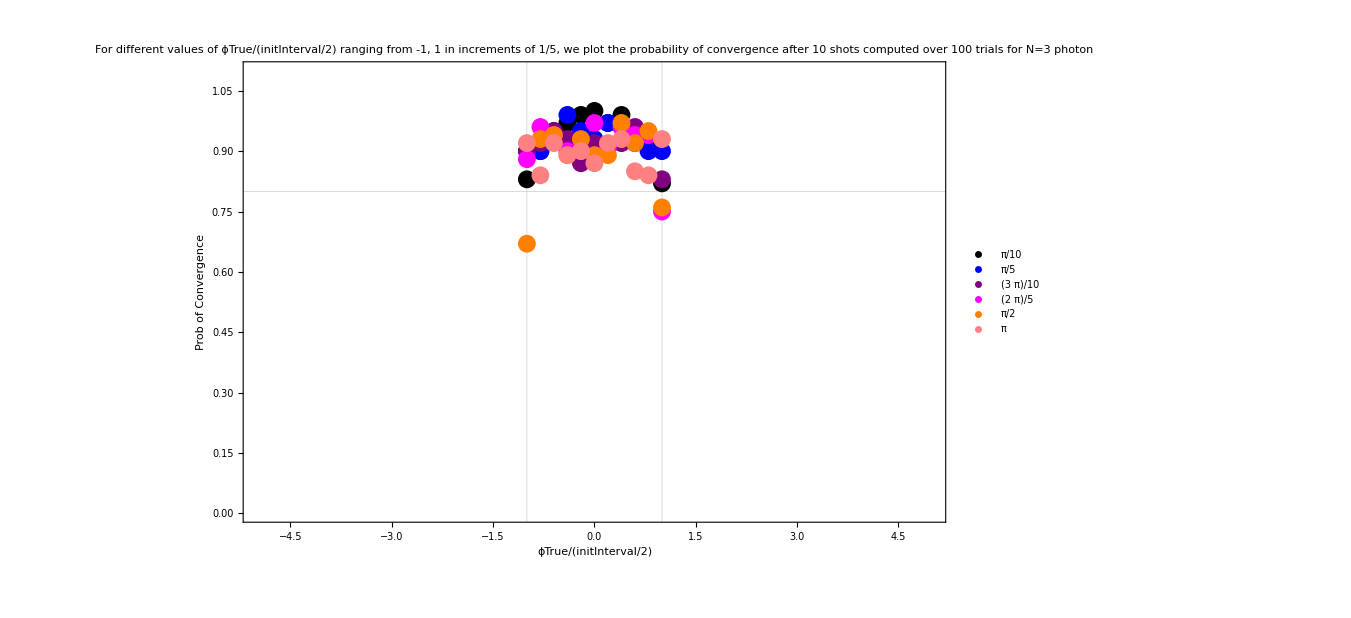

```mathematica
plot31=Show[ListPlot[plot[[1,1]],PlotStyle->{Black, Dashed},PlotLabel->"For different values of ϕTrue/(initInterval/2) ranging from -1, 1 in increments of 1/5, we plot the probability of convergence after 10 shots computed over 100 trials for N=3 photon",PlotLegends->{π/10},GridLines->{{-1,1},{0.8}}],ListPlot[plot[[1,2]],PlotStyle->{Blue,Dashed},PlotLegends->{(2π)/10}],ListPlot[plot[[1,3]],PlotStyle->{Purple, Dashed},PlotLegends->{(3π)/10}],ListPlot[plot[[1,4]],PlotStyle->{Magenta,Dashed},PlotLegends->{(4π)/10}],ListPlot[plot[[1,5]],PlotStyle->{Orange,Dashed},PlotLegends->{(5π)/10}],ListPlot[plot[[1,6]],PlotStyle->{Pink,Dashed},PlotLegends->{π}],PlotRange->{{-5,5},{0,1.1}}, Frame->True,FrameLabel->{"ϕTrue/(initInterval/2)",Style["Prob of Convergence",Thick]}, FrameTicks->Automatic, AxesOrigin-> {0,0},ImageSize->{1000, Automatic}]
```

```mathematica
(*color plot with error bars*)
```

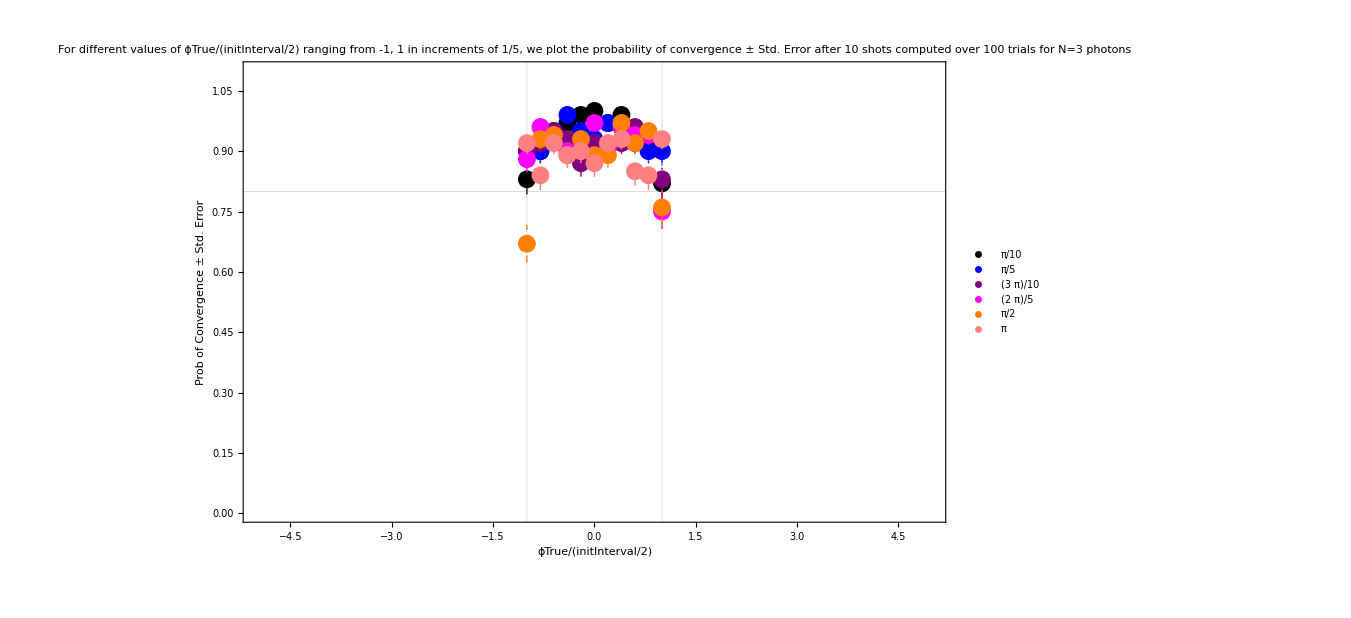

```mathematica
plot32=Show[ListPlot[plotStdError[[1,1]],PlotStyle->{Black, Dashed},PlotLabel->"For different values of ϕTrue/(initInterval/2) ranging from -1, 1 in increments of 1/5, we plot the probability of convergence ± Std. Error after 10 shots computed over 100 trials for N=3 photons",PlotLegends->{π/10},GridLines->{{-1,1},{0.8}}],ListPlot[plotStdError[[1,2]],PlotStyle->{Blue,Dashed},PlotLegends->{(2π)/10}],ListPlot[plotStdError[[1,3]],PlotStyle->{Purple, Dashed},PlotLegends->{(3π)/10}],ListPlot[plotStdError[[1,4]],PlotStyle->{Magenta,Dashed},PlotLegends->{(4π)/10}],ListPlot[plotStdError[[1,5]],PlotStyle->{Orange,Dashed},PlotLegends->{(5π)/10}],ListPlot[plotStdError[[1,6]],PlotStyle->{Pink,Dashed},PlotLegends->{π}],PlotRange->{{-5,5},{0,1.1}}, Frame->True,FrameLabel->{"ϕTrue/(initInterval/2)",Style["Prob of Convergence ± Std. Error",Thick]}, FrameTicks->Automatic, AxesOrigin-> {0,0},ImageSize->{1000, Automatic}]
```

```mathematica
(*Monochromatic plot distinguishing different N*)
```

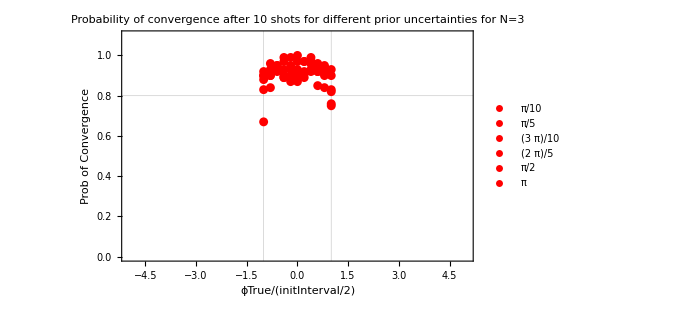

```mathematica
plot33=Show[ListPlot[plot[[1,1]],PlotStyle->{Red, Dashed},PlotLabel->"Probability of convergence after 10 shots for different prior uncertainties for N=3",PlotLegends->{π/10},GridLines->{{-1,1},{0.8}}],ListPlot[plot[[1,2]],PlotStyle->{Red,Dashed},PlotLegends->{(2π)/10}],ListPlot[plot[[1,3]],PlotStyle->{Red, Dashed},PlotLegends->{(3π)/10}],ListPlot[plot[[1,4]],PlotStyle->{Red,Dashed},PlotLegends->{(4π)/10}],ListPlot[plot[[1,5]],PlotStyle->{Red,Dashed},PlotLegends->{(5π)/10}],ListPlot[plot[[1,6]],PlotStyle->{Red,Dashed},PlotLegends->{π}],PlotRange->{{-5,5},{0,1.1}}, Frame->True,FrameLabel->{"ϕTrue/(initInterval/2)",Style["Prob of Convergence",Thick]}, FrameTicks->Automatic, AxesOrigin-> {0,0},ImageSize->{500, Automatic}]
```

```mathematica
(*Monochromatic plot with error bars*)
```

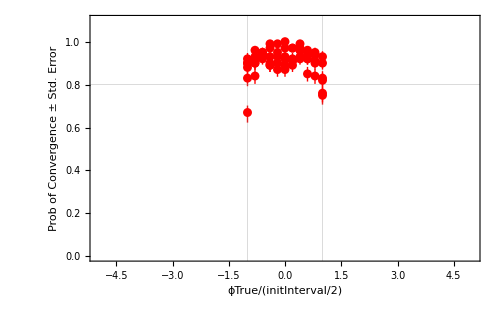

```mathematica
plot34=Show[ListPlot[plotStdError[[1,1]],PlotStyle->{Red, Dashed},GridLines->{{-1,1},{0.8}}],ListPlot[plotStdError[[1,2]],PlotStyle->{Red,Dashed}],ListPlot[plotStdError[[1,3]],PlotStyle->{Red, Dashed}],ListPlot[plotStdError[[1,4]],PlotStyle->{Red,Dashed}],ListPlot[plotStdError[[1,5]],PlotStyle->{Red,Dashed}],ListPlot[plotStdError[[1,6]],PlotStyle->{Red,Dashed}],PlotRange->{{-5,5},{0,1.1}}, Frame->True,FrameLabel->{"ϕTrue/(initInterval/2)",Style["Prob of Convergence ± Std. Error",Thick]}, FrameTicks->Automatic, AxesOrigin-> {0,0}]
```

```mathematica
plot34=-Graphics-;
```

```mathematica
(*Average of all the points in the interval between -1,1*)
```

```mathematica
Average3
```

{0.9350.007,0.9320.008,0.9140.008,0.9140.008,0.8850.009,0.8920.009}

```mathematica
Around[Mean[Table[Average3[[n,1,1]],{n,1,Length[Data]}]],Mean[Table[Average3[[n,1,2]],{n,1,Length[Data]}]]]
```

0.9120.008

```mathematica
Average3=0.9120.008
```

0.9120.008

```mathematica
Average3=Around[Average3[[1]],Sqrt[Average3[[1]](1-Average3[[1]])/100]]
```

0.9120.028

### Nph = 5

#### Vary ϕ_true for Δ_initial= π/10, π/5, 3π/10, 2π/5, π/2, π and plot probability of convergence over 100 trials

```mathematica
Data=Table[
GridOfϕTrue=Table[
ntrial=100;
listOfPhaseEstimators=Table[
(*Set the number of photons*)
nph=5;
(*Start with some interval [-Delta,Delta]*)
initInterval =del*π/10;
(*Nature chooses the true value for the phase in the interval (unknown to the experimentalist)*)
ϕTrue =phitrue;
(*The experimentalist starts with center point Subscript[ϕ, 0]=0 and uncertainty Subscript[Δ, 0]=initInterval.*)
ϕtilde=0;
Δinit = initInterval;
nshots=10;
(*can variance and probability be calculated only once?*)
Clear[delta];
partialvariance=GetVariance[1,nph,delta];
(*The output is : {Subscript[P, 1] Subscript[(δϕ^2), 1],Subscript[P, 2] Subscript[(δϕ^2), 2],...}. Need to divide probability from variance*)
δϕsquared = Table[partialvariance[[n]]/Pm[[n]],{n,1,nph+1}];
phitilde=Table[
delta=Δinit;
(*list of P(m|ϕ) are the probabilities of getting outcome m*)
(*The experimentalist constructs an optimal one-shot input state for this uncertainty interval,*)
(*Plug N00N in N00N regime, Gaussian in Gaussian regime*)
If[Δinit*nph> 5,OptState=PlugGSBS[](*Print["Gaussian"];*),OptState=PlugN00NSBS[](*Print["N00N"];*)];
Table[OptState[[1,n,2]] += n ϕtilde,{n,1,nph+1}];
(*The experimentalist makes measurements m with the following probabilities*)
prob=Re[listOfPmϕ/.OptState];
(*This is the probability distribution that nature has/knows*)
prob2=Re[listOfPmϕ/.OptState/.ϕ->ϕTrue-ϕtilde];
probDistrib = Accumulate[prob2[[1]]];
(*mRand is a uniformly distributed random real between 0 and 1*)
SeedRandom[];
mRand=Random[];
(*if mRand<probDistrib[[m]], outcome m occured experimentally*)
outcomeOccured =Max[Table[If[mRand>probDistrib[[m]],m,0],{m,1,nph+1}]]+1;
Indvariance=δϕsquared/.OptState;
variance=Indvariance[[1,outcomeOccured]];
Δnext = √(12*variance);
(*varianceDistrib[[1,outcomeOccured]]*)
phaseEstimators=listOfϕ1/.OptState;
(*and the following phase estimator*)
ϕtilde+=phaseEstimators[[1,outcomeOccured]];
(*Input state of the second shot gets phase shifted by this phase above*)
Δinit=Δnext;
,{shot,1, nshots}];
{Δnext,ϕtilde},{trial,1,ntrial}];
(*finds the mean of the varRatio over ntrials for a particular Δini*)
{ϕTrue,ϕTrue/(initInterval/2),listOfPhaseEstimators},{phitrue,-del*π/20,del*π/20,del*π/100}];
IfConverge=MatrixForm[Table[ProbOfTrue=0;{GridOfϕTrue[[n,1]],GridOfϕTrue[[n,2]],Table[If[GridOfϕTrue[[n,3,trial,2]]>(GridOfϕTrue[[n,1]]-GridOfϕTrue[[n,3,trial,1]]/2)&&GridOfϕTrue[[n,3,trial,2]]<(GridOfϕTrue[[n,1]]+GridOfϕTrue[[n,3,trial,1]]/2),ProbOfTrue+=1;GridOfϕTrue[[n,3,trial,2]],GridOfϕTrue[[n,3,trial,2]](*{GridOfϕTrue[[n,3,trial,2]],True}{GridOfϕTrue[[n,3,trial,2]],False}*)],{trial,1,ntrial}],N[ProbOfTrue/ntrial],del π/10},{n,1,Length[GridOfϕTrue]}]];
IfConverge1 = MatrixForm[Drop[IfConverge[[1]],None,{3}]],{del,{1,2,3,4,5,10}}];
```

```mathematica
(*Subscript[ϕ, true],Subscript[ϕ, true]/(Δ/2), probability of converging, Subscript[Δ, initial] *)
```

```mathematica
Data
```

{(-π/20 | -1 | 0.85 | π/10
-π/25 | -4/5 | 0.89 | π/10
-(3 π)/100 | -3/5 | 0.92 | π/10
-π/50 | -2/5 | 0.96 | π/10
-π/100 | -1/5 | 0.95 | π/10
0 | 0 | 0.98 | π/10
π/100 | 1/5 | 0.97 | π/10
π/50 | 2/5 | 0.9 | π/10
(3 π)/100 | 3/5 | 0.92 | π/10
π/25 | 4/5 | 0.88 | π/10
π/20 | 1 | 0.79 | π/10),(-π/10 | -1 | 0.77 | π/5
-(2 π)/25 | -4/5 | 0.9 | π/5
-(3 π)/50 | -3/5 | 0.87 | π/5
-π/25 | -2/5 | 0.95 | π/5
-π/50 | -1/5 | 0.95 | π/5
0 | 0 | 0.89 | π/5
π/50 | 1/5 | 0.92 | π/5
π/25 | 2/5 | 0.92 | π/5
(3 π)/50 | 3/5 | 0.86 | π/5
(2 π)/25 | 4/5 | 0.93 | π/5
π/10 | 1 | 0.78 | π/5),(-(3 π)/20 | -1 | 0.78 | (3 π)/10
-(3 π)/25 | -4/5 | 0.94 | (3 π)/10
-(9 π)/100 | -3/5 | 0.96 | (3 π)/10
-(3 π)/50 | -2/5 | 0.94 | (3 π)/10
-(3 π)/100 | -1/5 | 0.91 | (3 π)/10
0 | 0 | 0.9 | (3 π)/10
(3 π)/100 | 1/5 | 0.92 | (3 π)/10
(3 π)/50 | 2/5 | 0.93 | (3 π)/10
(9 π)/100 | 3/5 | 0.93 | (3 π)/10
(3 π)/25 | 4/5 | 0.92 | (3 π)/10
(3 π)/20 | 1 | 0.8 | (3 π)/10),(-π/5 | -1 | 0.91 | (2 π)/5
-(4 π)/25 | -4/5 | 0.93 | (2 π)/5
-(3 π)/25 | -3/5 | 0.89 | (2 π)/5
-(2 π)/25 | -2/5 | 0.91 | (2 π)/5
-π/25 | -1/5 | 0.88 | (2 π)/5
0 | 0 | 0.92 | (2 π)/5
π/25 | 1/5 | 0.89 | (2 π)/5
(2 π)/25 | 2/5 | 0.93 | (2 π)/5
(3 π)/25 | 3/5 | 0.88 | (2 π)/5
(4 π)/25 | 4/5 | 0.88 | (2 π)/5
π/5 | 1 | 0.91 | (2 π)/5),(-π/4 | -1 | 0.89 | π/2
-π/5 | -4/5 | 0.87 | π/2
-(3 π)/20 | -3/5 | 0.88 | π/2
-π/10 | -2/5 | 0.89 | π/2
-π/20 | -1/5 | 0.89 | π/2
0 | 0 | 0.85 | π/2
π/20 | 1/5 | 0.92 | π/2
π/10 | 2/5 | 0.91 | π/2
(3 π)/20 | 3/5 | 0.9 | π/2
π/5 | 4/5 | 0.9 | π/2
π/4 | 1 | 0.88 | π/2),(-π/2 | -1 | 0.84 | π
-(2 π)/5 | -4/5 | 0.91 | π
-(3 π)/10 | -3/5 | 0.93 | π
-π/5 | -2/5 | 0.91 | π
-π/10 | -1/5 | 0.9 | π
0 | 0 | 0.88 | π
π/10 | 1/5 | 0.9 | π
π/5 | 2/5 | 0.85 | π
(3 π)/10 | 3/5 | 0.92 | π
(2 π)/5 | 4/5 | 0.81 | π
π/2 | 1 | 0.85 | π)}

```mathematica
(*y -> probability of converging after 20 shots*)
```

```mathematica
y=MatrixForm[Table[Table[Data[[del,1,n,3]],{n,1, Length[Data[[1,1]]]}],{del,1, Length[Data]}]]
```

(0.85 | 0.89 | 0.92 | 0.96 | 0.95 | 0.98 | 0.97 | 0.9 | 0.92 | 0.88 | 0.79
0.77 | 0.9 | 0.87 | 0.95 | 0.95 | 0.89 | 0.92 | 0.92 | 0.86 | 0.93 | 0.78
0.78 | 0.94 | 0.96 | 0.94 | 0.91 | 0.9 | 0.92 | 0.93 | 0.93 | 0.92 | 0.8
0.91 | 0.93 | 0.89 | 0.91 | 0.88 | 0.92 | 0.89 | 0.93 | 0.88 | 0.88 | 0.91
0.89 | 0.87 | 0.88 | 0.89 | 0.89 | 0.85 | 0.92 | 0.91 | 0.9 | 0.9 | 0.88
0.84 | 0.91 | 0.93 | 0.91 | 0.9 | 0.88 | 0.9 | 0.85 | 0.92 | 0.81 | 0.85)

```mathematica
(*Standard error for sample proportion of success p is √(p(1-p)/100)*)
```

```mathematica
z=MatrixForm[Table[Table[Around[Data[[del,1,n,3]],√(((Data[[del,1,n,3]])(1-Data[[del,1,n,3]]))/ntrial)],{n,1, Length[Data[[1,1]]]}],{del,1, Length[Data]}]]
```

(0.850.04 | 0.8900.031 | 0.9200.027 | 0.9600.020 | 0.9500.022 | 0.9800.014 | 0.9700.017 | 0.9000.030 | 0.9200.027 | 0.8800.032 | 0.790.04
0.770.04 | 0.9000.030 | 0.8700.034 | 0.9500.022 | 0.9500.022 | 0.8900.031 | 0.9200.027 | 0.9200.027 | 0.8600.035 | 0.9300.026 | 0.780.04
0.780.04 | 0.9400.024 | 0.9600.020 | 0.9400.024 | 0.9100.029 | 0.9000.030 | 0.9200.027 | 0.9300.026 | 0.9300.026 | 0.9200.027 | 0.800.04
0.9100.029 | 0.9300.026 | 0.8900.031 | 0.9100.029 | 0.8800.032 | 0.9200.027 | 0.8900.031 | 0.9300.026 | 0.8800.032 | 0.8800.032 | 0.9100.029
0.8900.031 | 0.8700.034 | 0.8800.032 | 0.8900.031 | 0.8900.031 | 0.850.04 | 0.9200.027 | 0.9100.029 | 0.9000.030 | 0.9000.030 | 0.8800.032
0.840.04 | 0.9100.029 | 0.9300.026 | 0.9100.029 | 0.9000.030 | 0.8800.032 | 0.9000.030 | 0.850.04 | 0.9200.027 | 0.810.04 | 0.850.04)

```mathematica
Average3=Table[MatrixForm[Mean[z[[1,n]]]],{n,1,Length[Data]}]
```

{0.9100.008,0.8850.009,0.9030.009,0.9030.009,0.8890.009,0.8820.010}

```mathematica
(*x -> ϕTrue/(Δ/2)*)
```

```mathematica
x=MatrixForm[Table[Table[Data[[del,1,n,2]],{n,1, Length[Data[[1,1]]]}],{del,1, Length[Data]}]]
```

(-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1)

```mathematica
plot = MatrixForm[Table[Thread[{x[[1,n]],y[[1,n]]}],{n,1,Length[Data]}]]
```

((-1
0.85) | (-4/5
0.89) | (-3/5
0.92) | (-2/5
0.96) | (-1/5
0.95) | (0
0.98) | (1/5
0.97) | (2/5
0.9) | (3/5
0.92) | (4/5
0.88) | (1
0.79)
(-1
0.77) | (-4/5
0.9) | (-3/5
0.87) | (-2/5
0.95) | (-1/5
0.95) | (0
0.89) | (1/5
0.92) | (2/5
0.92) | (3/5
0.86) | (4/5
0.93) | (1
0.78)
(-1
0.78) | (-4/5
0.94) | (-3/5
0.96) | (-2/5
0.94) | (-1/5
0.91) | (0
0.9) | (1/5
0.92) | (2/5
0.93) | (3/5
0.93) | (4/5
0.92) | (1
0.8)
(-1
0.91) | (-4/5
0.93) | (-3/5
0.89) | (-2/5
0.91) | (-1/5
0.88) | (0
0.92) | (1/5
0.89) | (2/5
0.93) | (3/5
0.88) | (4/5
0.88) | (1
0.91)
(-1
0.89) | (-4/5
0.87) | (-3/5
0.88) | (-2/5
0.89) | (-1/5
0.89) | (0
0.85) | (1/5
0.92) | (2/5
0.91) | (3/5
0.9) | (4/5
0.9) | (1
0.88)
(-1
0.84) | (-4/5
0.91) | (-3/5
0.93) | (-2/5
0.91) | (-1/5
0.9) | (0
0.88) | (1/5
0.9) | (2/5
0.85) | (3/5
0.92) | (4/5
0.81) | (1
0.85))

```mathematica
plotStdError= MatrixForm[Table[Thread[{x[[1,n]],z[[1,n]]}],{n,1,Length[Data]}]]
```

((-1
0.850.04) | (-4/5
0.8900.031) | (-3/5
0.9200.027) | (-2/5
0.9600.020) | (-1/5
0.9500.022) | (0
0.9800.014) | (1/5
0.9700.017) | (2/5
0.9000.030) | (3/5
0.9200.027) | (4/5
0.8800.032) | (1
0.790.04)
(-1
0.770.04) | (-4/5
0.9000.030) | (-3/5
0.8700.034) | (-2/5
0.9500.022) | (-1/5
0.9500.022) | (0
0.8900.031) | (1/5
0.9200.027) | (2/5
0.9200.027) | (3/5
0.8600.035) | (4/5
0.9300.026) | (1
0.780.04)
(-1
0.780.04) | (-4/5
0.9400.024) | (-3/5
0.9600.020) | (-2/5
0.9400.024) | (-1/5
0.9100.029) | (0
0.9000.030) | (1/5
0.9200.027) | (2/5
0.9300.026) | (3/5
0.9300.026) | (4/5
0.9200.027) | (1
0.800.04)
(-1
0.9100.029) | (-4/5
0.9300.026) | (-3/5
0.8900.031) | (-2/5
0.9100.029) | (-1/5
0.8800.032) | (0
0.9200.027) | (1/5
0.8900.031) | (2/5
0.9300.026) | (3/5
0.8800.032) | (4/5
0.8800.032) | (1
0.9100.029)
(-1
0.8900.031) | (-4/5
0.8700.034) | (-3/5
0.8800.032) | (-2/5
0.8900.031) | (-1/5
0.8900.031) | (0
0.850.04) | (1/5
0.9200.027) | (2/5
0.9100.029) | (3/5
0.9000.030) | (4/5
0.9000.030) | (1
0.8800.032)
(-1
0.840.04) | (-4/5
0.9100.029) | (-3/5
0.9300.026) | (-2/5
0.9100.029) | (-1/5
0.9000.030) | (0
0.8800.032) | (1/5
0.9000.030) | (2/5
0.850.04) | (3/5
0.9200.027) | (4/5
0.810.04) | (1
0.850.04))

```mathematica
(*For different values of quantity A = ϕTrue/(initInterval/2) ranging from -1, 1 in increments of 1/5, we plot the probability of convergence after 10 shots computed over 100 trials for N=3 photons*)
```

```mathematica
(*color plot distinguishing different Δinitials*)
```

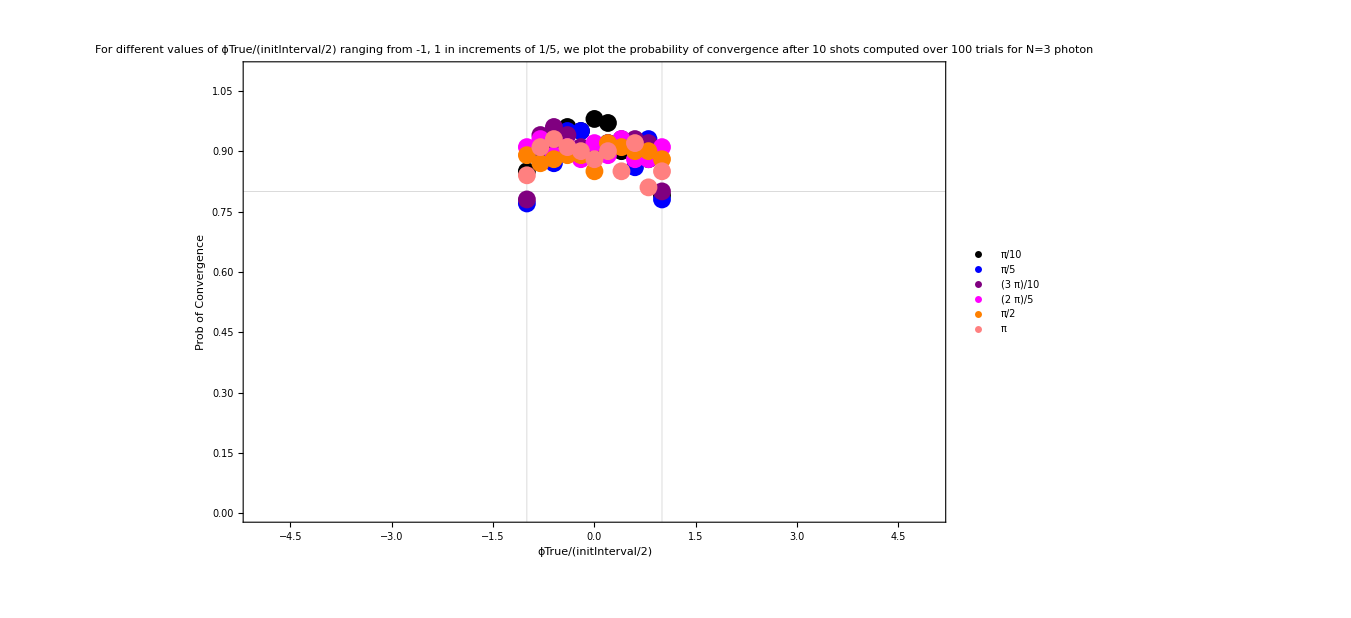

```mathematica
plot31=Show[ListPlot[plot[[1,1]],PlotStyle->{Black, Dashed},PlotLabel->"For different values of ϕTrue/(initInterval/2) ranging from -1, 1 in increments of 1/5, we plot the probability of convergence after 10 shots computed over 100 trials for N=3 photon",PlotLegends->{π/10},GridLines->{{-1,1},{0.8}}],ListPlot[plot[[1,2]],PlotStyle->{Blue,Dashed},PlotLegends->{(2π)/10}],ListPlot[plot[[1,3]],PlotStyle->{Purple, Dashed},PlotLegends->{(3π)/10}],ListPlot[plot[[1,4]],PlotStyle->{Magenta,Dashed},PlotLegends->{(4π)/10}],ListPlot[plot[[1,5]],PlotStyle->{Orange,Dashed},PlotLegends->{(5π)/10}],ListPlot[plot[[1,6]],PlotStyle->{Pink,Dashed},PlotLegends->{π}],PlotRange->{{-5,5},{0,1.1}}, Frame->True,FrameLabel->{"ϕTrue/(initInterval/2)",Style["Prob of Convergence",Thick]}, FrameTicks->Automatic, AxesOrigin-> {0,0},ImageSize->{1000, Automatic}]
```

```mathematica
(*color plot with error bars*)
```

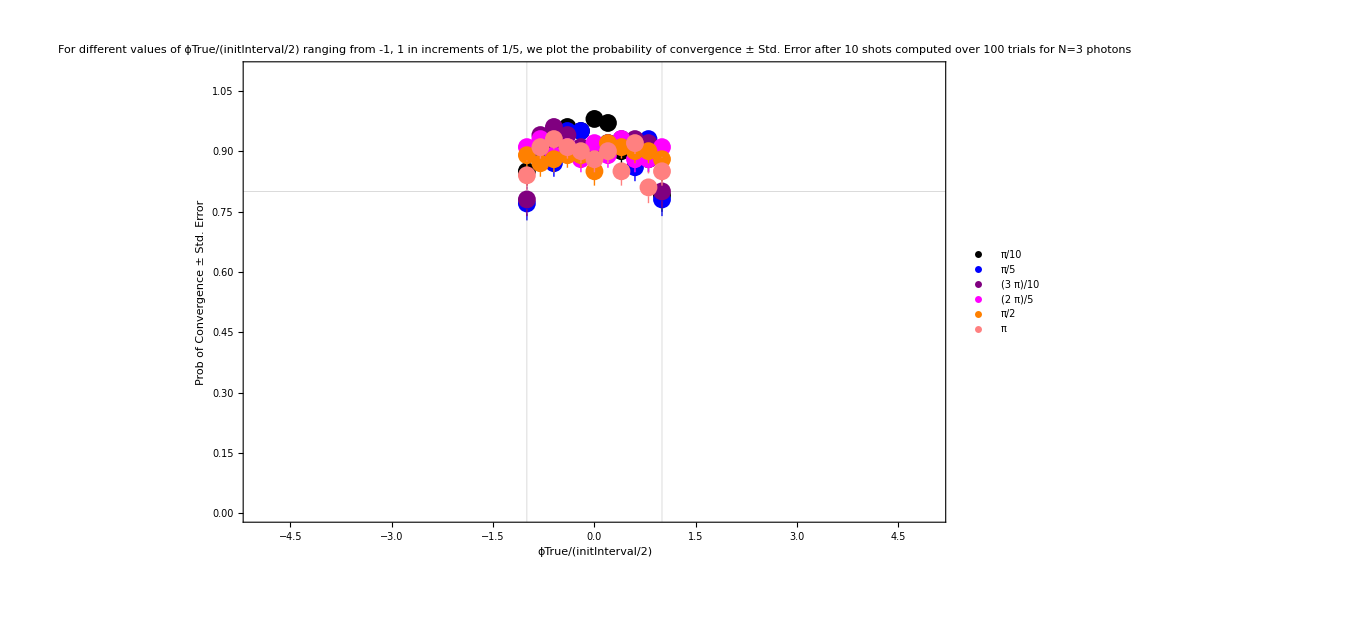

```mathematica
plot32=Show[ListPlot[plotStdError[[1,1]],PlotStyle->{Black, Dashed},PlotLabel->"For different values of ϕTrue/(initInterval/2) ranging from -1, 1 in increments of 1/5, we plot the probability of convergence ± Std. Error after 10 shots computed over 100 trials for N=3 photons",PlotLegends->{π/10},GridLines->{{-1,1},{0.8}}],ListPlot[plotStdError[[1,2]],PlotStyle->{Blue,Dashed},PlotLegends->{(2π)/10}],ListPlot[plotStdError[[1,3]],PlotStyle->{Purple, Dashed},PlotLegends->{(3π)/10}],ListPlot[plotStdError[[1,4]],PlotStyle->{Magenta,Dashed},PlotLegends->{(4π)/10}],ListPlot[plotStdError[[1,5]],PlotStyle->{Orange,Dashed},PlotLegends->{(5π)/10}],ListPlot[plotStdError[[1,6]],PlotStyle->{Pink,Dashed},PlotLegends->{π}],PlotRange->{{-5,5},{0,1.1}}, Frame->True,FrameLabel->{"ϕTrue/(initInterval/2)",Style["Prob of Convergence ± Std. Error",Thick]}, FrameTicks->Automatic, AxesOrigin-> {0,0},ImageSize->{1000, Automatic}]
```

```mathematica
(*Monochromatic plot distinguishing different N*)
```

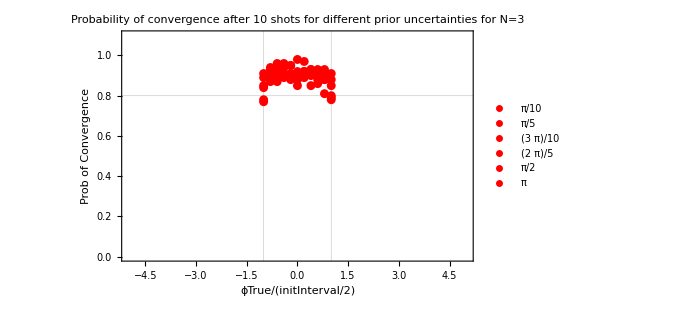

```mathematica
plot33=Show[ListPlot[plot[[1,1]],PlotStyle->{Red, Dashed},PlotLabel->"Probability of convergence after 10 shots for different prior uncertainties for N=3",PlotLegends->{π/10},GridLines->{{-1,1},{0.8}}],ListPlot[plot[[1,2]],PlotStyle->{Red,Dashed},PlotLegends->{(2π)/10}],ListPlot[plot[[1,3]],PlotStyle->{Red, Dashed},PlotLegends->{(3π)/10}],ListPlot[plot[[1,4]],PlotStyle->{Red,Dashed},PlotLegends->{(4π)/10}],ListPlot[plot[[1,5]],PlotStyle->{Red,Dashed},PlotLegends->{(5π)/10}],ListPlot[plot[[1,6]],PlotStyle->{Red,Dashed},PlotLegends->{π}],PlotRange->{{-5,5},{0,1.1}}, Frame->True,FrameLabel->{"ϕTrue/(initInterval/2)",Style["Prob of Convergence",Thick]}, FrameTicks->Automatic, AxesOrigin-> {0,0},ImageSize->{500, Automatic}]
```

```mathematica
(*Monochromatic plot with error bars*)
```

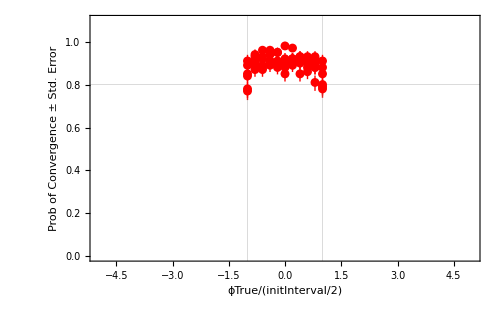

```mathematica
plot34=Show[ListPlot[plotStdError[[1,1]],PlotStyle->{Red, Dashed},GridLines->{{-1,1},{0.8}}],ListPlot[plotStdError[[1,2]],PlotStyle->{Red,Dashed}],ListPlot[plotStdError[[1,3]],PlotStyle->{Red, Dashed}],ListPlot[plotStdError[[1,4]],PlotStyle->{Red,Dashed}],ListPlot[plotStdError[[1,5]],PlotStyle->{Red,Dashed}],ListPlot[plotStdError[[1,6]],PlotStyle->{Red,Dashed}],PlotRange->{{-5,5},{0,1.1}}, Frame->True,FrameLabel->{"ϕTrue/(initInterval/2)",Style["Prob of Convergence ± Std. Error",Thick]}, FrameTicks->Automatic, AxesOrigin-> {0,0}]
```

```mathematica
plot54=-Graphics-;
```

```mathematica
(*Average of all the points in the interval between -1,1*)
```

```mathematica
Average3
```

{0.9100.008,0.8850.009,0.9030.009,0.9030.009,0.8890.009,0.8820.010}

```mathematica
Average3=Around[Mean[Table[Average3[[n,1,1]],{n,1,Length[Data]}]],Mean[Table[Average3[[n,1,2]],{n,1,Length[Data]}]]]
```

0.8950.009

```mathematica
Average5=0.8950.009
```

0.8950.009

```mathematica
Average5=Around[Average5[[1]],Sqrt[Average5[[1]](1-Average5[[1]])/100]]
```

0.8950.031

### Nph = 7

#### Vary ϕ_true for Δ_initial= π/10, π/5, 3π/10, 2π/5, π/2, π and plot probability of convergence over 100 trials

```mathematica
Data=Table[
GridOfϕTrue=Table[
ntrial=100;
listOfPhaseEstimators=Table[
(*Set the number of photons*)
nph=7;
(*Start with some interval [-Delta,Delta]*)
initInterval =del*π/10;
(*Nature chooses the true value for the phase in the interval (unknown to the experimentalist)*)
ϕTrue =phitrue;
(*The experimentalist starts with center point Subscript[ϕ, 0]=0 and uncertainty Subscript[Δ, 0]=initInterval.*)
ϕtilde=0;
Δinit = initInterval;
nshots=10;
(*can variance and probability be calculated only once?*)
Clear[delta];
partialvariance=GetVariance[1,nph,delta];
(*The output is : {Subscript[P, 1] Subscript[(δϕ^2), 1],Subscript[P, 2] Subscript[(δϕ^2), 2],...}. Need to divide probability from variance*)
δϕsquared = Table[partialvariance[[n]]/Pm[[n]],{n,1,nph+1}];
phitilde=Table[
delta=Δinit;
(*list of P(m|ϕ) are the probabilities of getting outcome m*)
(*The experimentalist constructs an optimal one-shot input state for this uncertainty interval,*)
(*Plug N00N in N00N regime, Gaussian in Gaussian regime*)
If[Δinit*nph> 5,OptState=PlugGSBS[](*Print["Gaussian"];*),OptState=PlugN00NSBS[](*Print["N00N"];*)];
Table[OptState[[1,n,2]] += n ϕtilde,{n,1,nph+1}];
(*The experimentalist makes measurements m with the following probabilities*)
prob=Re[listOfPmϕ/.OptState];
(*This is the probability distribution that nature has/knows*)
prob2=Re[listOfPmϕ/.OptState/.ϕ->ϕTrue-ϕtilde];
probDistrib = Accumulate[prob2[[1]]];
(*mRand is a uniformly distributed random real between 0 and 1*)
SeedRandom[];
mRand=Random[];
(*if mRand<probDistrib[[m]], outcome m occured experimentally*)
outcomeOccured =Max[Table[If[mRand>probDistrib[[m]],m,0],{m,1,nph+1}]]+1;
Indvariance=δϕsquared/.OptState;
variance=Indvariance[[1,outcomeOccured]];
Δnext = √(12*variance);
(*varianceDistrib[[1,outcomeOccured]]*)
phaseEstimators=listOfϕ1/.OptState;
(*and the following phase estimator*)
ϕtilde+=phaseEstimators[[1,outcomeOccured]];
(*Input state of the second shot gets phase shifted by this phase above*)
Δinit=Δnext;
,{shot,1, nshots}];
{Δnext,ϕtilde},{trial,1,ntrial}];
(*finds the mean of the varRatio over ntrials for a particular Δini*)
{ϕTrue,ϕTrue/(initInterval/2),listOfPhaseEstimators},{phitrue,-del*π/20,del*π/20,del*π/100}];
IfConverge=MatrixForm[Table[ProbOfTrue=0;{GridOfϕTrue[[n,1]],GridOfϕTrue[[n,2]],Table[If[GridOfϕTrue[[n,3,trial,2]]>(GridOfϕTrue[[n,1]]-GridOfϕTrue[[n,3,trial,1]]/2)&&GridOfϕTrue[[n,3,trial,2]]<(GridOfϕTrue[[n,1]]+GridOfϕTrue[[n,3,trial,1]]/2),ProbOfTrue+=1;GridOfϕTrue[[n,3,trial,2]],GridOfϕTrue[[n,3,trial,2]](*{GridOfϕTrue[[n,3,trial,2]],True}{GridOfϕTrue[[n,3,trial,2]],False}*)],{trial,1,ntrial}],N[ProbOfTrue/ntrial],del π/10},{n,1,Length[GridOfϕTrue]}]];
IfConverge1 = MatrixForm[Drop[IfConverge[[1]],None,{3}]],{del,{1,2,3,4,5,10}}];
```

```mathematica
(*Subscript[ϕ, true],Subscript[ϕ, true]/(Δ/2), probability of converging, Subscript[Δ, initial] *)
```

```mathematica
Data
```

{(-π/20 | -1 | 0.86 | π/10
-π/25 | -4/5 | 0.88 | π/10
-(3 π)/100 | -3/5 | 0.91 | π/10
-π/50 | -2/5 | 0.94 | π/10
-π/100 | -1/5 | 0.94 | π/10
0 | 0 | 0.93 | π/10
π/100 | 1/5 | 0.94 | π/10
π/50 | 2/5 | 0.94 | π/10
(3 π)/100 | 3/5 | 0.92 | π/10
π/25 | 4/5 | 0.88 | π/10
π/20 | 1 | 0.89 | π/10),(-π/10 | -1 | 0.85 | π/5
-(2 π)/25 | -4/5 | 0.93 | π/5
-(3 π)/50 | -3/5 | 0.97 | π/5
-π/25 | -2/5 | 0.89 | π/5
-π/50 | -1/5 | 0.91 | π/5
0 | 0 | 0.83 | π/5
π/50 | 1/5 | 0.93 | π/5
π/25 | 2/5 | 0.87 | π/5
(3 π)/50 | 3/5 | 0.93 | π/5
(2 π)/25 | 4/5 | 0.93 | π/5
π/10 | 1 | 0.81 | π/5),(-(3 π)/20 | -1 | 0.92 | (3 π)/10
-(3 π)/25 | -4/5 | 0.92 | (3 π)/10
-(9 π)/100 | -3/5 | 0.87 | (3 π)/10
-(3 π)/50 | -2/5 | 0.9 | (3 π)/10
-(3 π)/100 | -1/5 | 0.89 | (3 π)/10
0 | 0 | 0.94 | (3 π)/10
(3 π)/100 | 1/5 | 0.89 | (3 π)/10
(3 π)/50 | 2/5 | 0.91 | (3 π)/10
(9 π)/100 | 3/5 | 0.83 | (3 π)/10
(3 π)/25 | 4/5 | 0.87 | (3 π)/10
(3 π)/20 | 1 | 0.94 | (3 π)/10),(-π/5 | -1 | 0.9 | (2 π)/5
-(4 π)/25 | -4/5 | 0.92 | (2 π)/5
-(3 π)/25 | -3/5 | 0.84 | (2 π)/5
-(2 π)/25 | -2/5 | 0.94 | (2 π)/5
-π/25 | -1/5 | 0.93 | (2 π)/5
0 | 0 | 0.87 | (2 π)/5
π/25 | 1/5 | 0.88 | (2 π)/5
(2 π)/25 | 2/5 | 0.91 | (2 π)/5
(3 π)/25 | 3/5 | 0.89 | (2 π)/5
(4 π)/25 | 4/5 | 0.89 | (2 π)/5
π/5 | 1 | 0.94 | (2 π)/5),(-π/4 | -1 | 0.84 | π/2
-π/5 | -4/5 | 0.95 | π/2
-(3 π)/20 | -3/5 | 0.94 | π/2
-π/10 | -2/5 | 0.96 | π/2
-π/20 | -1/5 | 0.94 | π/2
0 | 0 | 0.83 | π/2
π/20 | 1/5 | 0.92 | π/2
π/10 | 2/5 | 0.91 | π/2
(3 π)/20 | 3/5 | 0.94 | π/2
π/5 | 4/5 | 0.97 | π/2
π/4 | 1 | 0.82 | π/2),(-π/2 | -1 | 0.89 | π
-(2 π)/5 | -4/5 | 0.92 | π
-(3 π)/10 | -3/5 | 0.89 | π
-π/5 | -2/5 | 0.85 | π
-π/10 | -1/5 | 0.84 | π
0 | 0 | 0.78 | π
π/10 | 1/5 | 0.86 | π
π/5 | 2/5 | 0.77 | π
(3 π)/10 | 3/5 | 0.86 | π
(2 π)/5 | 4/5 | 0.92 | π
π/2 | 1 | 0.87 | π)}

```mathematica
(*y -> probability of converging after 20 shots*)
```

```mathematica
y=MatrixForm[Table[Table[Data[[del,1,n,3]],{n,1, Length[Data[[1,1]]]}],{del,1, Length[Data]}]]
```

(0.86 | 0.88 | 0.91 | 0.94 | 0.94 | 0.93 | 0.94 | 0.94 | 0.92 | 0.88 | 0.89
0.85 | 0.93 | 0.97 | 0.89 | 0.91 | 0.83 | 0.93 | 0.87 | 0.93 | 0.93 | 0.81
0.92 | 0.92 | 0.87 | 0.9 | 0.89 | 0.94 | 0.89 | 0.91 | 0.83 | 0.87 | 0.94
0.9 | 0.92 | 0.84 | 0.94 | 0.93 | 0.87 | 0.88 | 0.91 | 0.89 | 0.89 | 0.94
0.84 | 0.95 | 0.94 | 0.96 | 0.94 | 0.83 | 0.92 | 0.91 | 0.94 | 0.97 | 0.82
0.89 | 0.92 | 0.89 | 0.85 | 0.84 | 0.78 | 0.86 | 0.77 | 0.86 | 0.92 | 0.87)

```mathematica
(*Standard error for sample proportion of success p is √(p(1-p)/100)*)
```

```mathematica
z=MatrixForm[Table[Table[Around[Data[[del,1,n,3]],√(((Data[[del,1,n,3]])(1-Data[[del,1,n,3]]))/ntrial)],{n,1, Length[Data[[1,1]]]}],{del,1, Length[Data]}]]
```

(0.8600.035 | 0.8800.032 | 0.9100.029 | 0.9400.024 | 0.9400.024 | 0.9300.026 | 0.9400.024 | 0.9400.024 | 0.9200.027 | 0.8800.032 | 0.8900.031
0.850.04 | 0.9300.026 | 0.9700.017 | 0.8900.031 | 0.9100.029 | 0.830.04 | 0.9300.026 | 0.8700.034 | 0.9300.026 | 0.9300.026 | 0.810.04
0.9200.027 | 0.9200.027 | 0.8700.034 | 0.9000.030 | 0.8900.031 | 0.9400.024 | 0.8900.031 | 0.9100.029 | 0.830.04 | 0.8700.034 | 0.9400.024
0.9000.030 | 0.9200.027 | 0.840.04 | 0.9400.024 | 0.9300.026 | 0.8700.034 | 0.8800.032 | 0.9100.029 | 0.8900.031 | 0.8900.031 | 0.9400.024
0.840.04 | 0.9500.022 | 0.9400.024 | 0.9600.020 | 0.9400.024 | 0.830.04 | 0.9200.027 | 0.9100.029 | 0.9400.024 | 0.9700.017 | 0.820.04
0.8900.031 | 0.9200.027 | 0.8900.031 | 0.850.04 | 0.840.04 | 0.780.04 | 0.8600.035 | 0.770.04 | 0.8600.035 | 0.9200.027 | 0.8700.034)

```mathematica
Average7=Table[MatrixForm[Mean[z[[1,n]]]],{n,1,Length[Data]}]
```

{0.9120.009,0.8950.009,0.8980.009,0.9010.009,0.9110.008,0.8590.010}

```mathematica
(*x -> ϕTrue/(Δ/2)*)
```

```mathematica
x=MatrixForm[Table[Table[Data[[del,1,n,2]],{n,1, Length[Data[[1,1]]]}],{del,1, Length[Data]}]]
```

(-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1)

```mathematica
plot = MatrixForm[Table[Thread[{x[[1,n]],y[[1,n]]}],{n,1,Length[Data]}]]
```

((-1
0.86) | (-4/5
0.88) | (-3/5
0.91) | (-2/5
0.94) | (-1/5
0.94) | (0
0.93) | (1/5
0.94) | (2/5
0.94) | (3/5
0.92) | (4/5
0.88) | (1
0.89)
(-1
0.85) | (-4/5
0.93) | (-3/5
0.97) | (-2/5
0.89) | (-1/5
0.91) | (0
0.83) | (1/5
0.93) | (2/5
0.87) | (3/5
0.93) | (4/5
0.93) | (1
0.81)
(-1
0.92) | (-4/5
0.92) | (-3/5
0.87) | (-2/5
0.9) | (-1/5
0.89) | (0
0.94) | (1/5
0.89) | (2/5
0.91) | (3/5
0.83) | (4/5
0.87) | (1
0.94)
(-1
0.9) | (-4/5
0.92) | (-3/5
0.84) | (-2/5
0.94) | (-1/5
0.93) | (0
0.87) | (1/5
0.88) | (2/5
0.91) | (3/5
0.89) | (4/5
0.89) | (1
0.94)
(-1
0.84) | (-4/5
0.95) | (-3/5
0.94) | (-2/5
0.96) | (-1/5
0.94) | (0
0.83) | (1/5
0.92) | (2/5
0.91) | (3/5
0.94) | (4/5
0.97) | (1
0.82)
(-1
0.89) | (-4/5
0.92) | (-3/5
0.89) | (-2/5
0.85) | (-1/5
0.84) | (0
0.78) | (1/5
0.86) | (2/5
0.77) | (3/5
0.86) | (4/5
0.92) | (1
0.87))

```mathematica
plotStdError= MatrixForm[Table[Thread[{x[[1,n]],z[[1,n]]}],{n,1,Length[Data]}]]
```

((-1
0.8600.035) | (-4/5
0.8800.032) | (-3/5
0.9100.029) | (-2/5
0.9400.024) | (-1/5
0.9400.024) | (0
0.9300.026) | (1/5
0.9400.024) | (2/5
0.9400.024) | (3/5
0.9200.027) | (4/5
0.8800.032) | (1
0.8900.031)
(-1
0.850.04) | (-4/5
0.9300.026) | (-3/5
0.9700.017) | (-2/5
0.8900.031) | (-1/5
0.9100.029) | (0
0.830.04) | (1/5
0.9300.026) | (2/5
0.8700.034) | (3/5
0.9300.026) | (4/5
0.9300.026) | (1
0.810.04)
(-1
0.9200.027) | (-4/5
0.9200.027) | (-3/5
0.8700.034) | (-2/5
0.9000.030) | (-1/5
0.8900.031) | (0
0.9400.024) | (1/5
0.8900.031) | (2/5
0.9100.029) | (3/5
0.830.04) | (4/5
0.8700.034) | (1
0.9400.024)
(-1
0.9000.030) | (-4/5
0.9200.027) | (-3/5
0.840.04) | (-2/5
0.9400.024) | (-1/5
0.9300.026) | (0
0.8700.034) | (1/5
0.8800.032) | (2/5
0.9100.029) | (3/5
0.8900.031) | (4/5
0.8900.031) | (1
0.9400.024)
(-1
0.840.04) | (-4/5
0.9500.022) | (-3/5
0.9400.024) | (-2/5
0.9600.020) | (-1/5
0.9400.024) | (0
0.830.04) | (1/5
0.9200.027) | (2/5
0.9100.029) | (3/5
0.9400.024) | (4/5
0.9700.017) | (1
0.820.04)
(-1
0.8900.031) | (-4/5
0.9200.027) | (-3/5
0.8900.031) | (-2/5
0.850.04) | (-1/5
0.840.04) | (0
0.780.04) | (1/5
0.8600.035) | (2/5
0.770.04) | (3/5
0.8600.035) | (4/5
0.9200.027) | (1
0.8700.034))

```mathematica
(*For different values of quantity A = ϕTrue/(initInterval/2) ranging from -1, 1 in increments of 1/5, we plot the probability of convergence after 10 shots computed over 100 trials for N=3 photons*)
```

```mathematica
(*color plot distinguishing different Δinitials*)
```

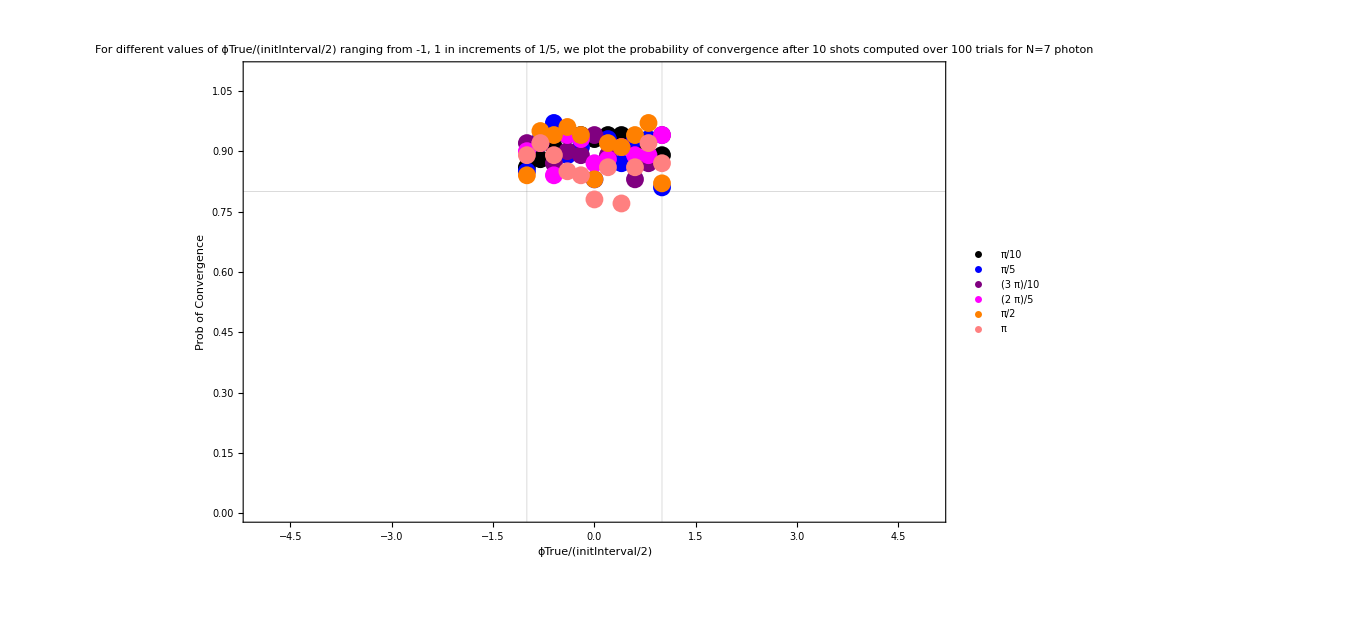

```mathematica
plot71=Show[ListPlot[plot[[1,1]],PlotStyle->{Black, Dashed},PlotLabel->"For different values of ϕTrue/(initInterval/2) ranging from -1, 1 in increments of 1/5, we plot the probability of convergence after 10 shots computed over 100 trials for N=7 photon",PlotLegends->{π/10},GridLines->{{-1,1},{0.8}}],ListPlot[plot[[1,2]],PlotStyle->{Blue,Dashed},PlotLegends->{(2π)/10}],ListPlot[plot[[1,3]],PlotStyle->{Purple, Dashed},PlotLegends->{(3π)/10}],ListPlot[plot[[1,4]],PlotStyle->{Magenta,Dashed},PlotLegends->{(4π)/10}],ListPlot[plot[[1,5]],PlotStyle->{Orange,Dashed},PlotLegends->{(5π)/10}],ListPlot[plot[[1,6]],PlotStyle->{Pink,Dashed},PlotLegends->{π}],PlotRange->{{-5,5},{0,1.1}}, Frame->True,FrameLabel->{"ϕTrue/(initInterval/2)",Style["Prob of Convergence",Thick]}, FrameTicks->Automatic, AxesOrigin-> {0,0},ImageSize->{1000, Automatic}]
```

```mathematica
(*color plot with error bars*)
```

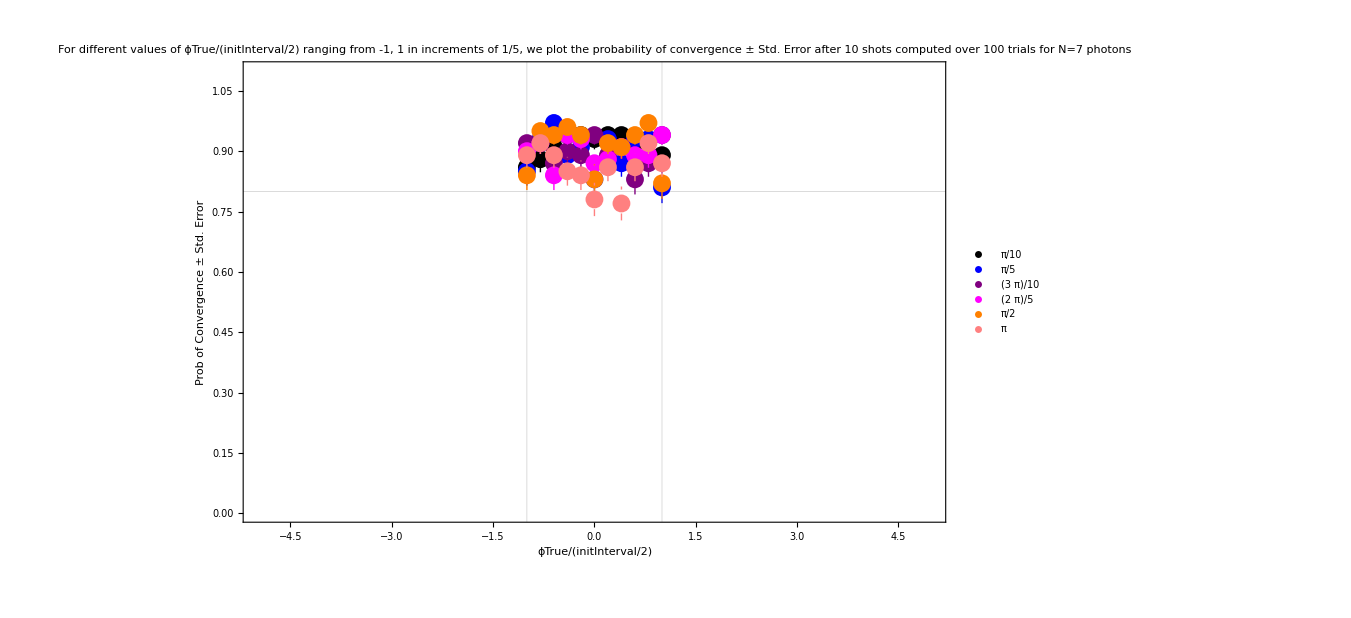

```mathematica
plot72=Show[ListPlot[plotStdError[[1,1]],PlotStyle->{Black, Dashed},PlotLabel->"For different values of ϕTrue/(initInterval/2) ranging from -1, 1 in increments of 1/5, we plot the probability of convergence ± Std. Error after 10 shots computed over 100 trials for N=7 photons",PlotLegends->{π/10},GridLines->{{-1,1},{0.8}}],ListPlot[plotStdError[[1,2]],PlotStyle->{Blue,Dashed},PlotLegends->{(2π)/10}],ListPlot[plotStdError[[1,3]],PlotStyle->{Purple, Dashed},PlotLegends->{(3π)/10}],ListPlot[plotStdError[[1,4]],PlotStyle->{Magenta,Dashed},PlotLegends->{(4π)/10}],ListPlot[plotStdError[[1,5]],PlotStyle->{Orange,Dashed},PlotLegends->{(5π)/10}],ListPlot[plotStdError[[1,6]],PlotStyle->{Pink,Dashed},PlotLegends->{π}],PlotRange->{{-5,5},{0,1.1}}, Frame->True,FrameLabel->{"ϕTrue/(initInterval/2)",Style["Prob of Convergence ± Std. Error",Thick]}, FrameTicks->Automatic, AxesOrigin-> {0,0},ImageSize->{1000, Automatic}]
```

```mathematica
(*Monochromatic plot distinguishing different N*)
```

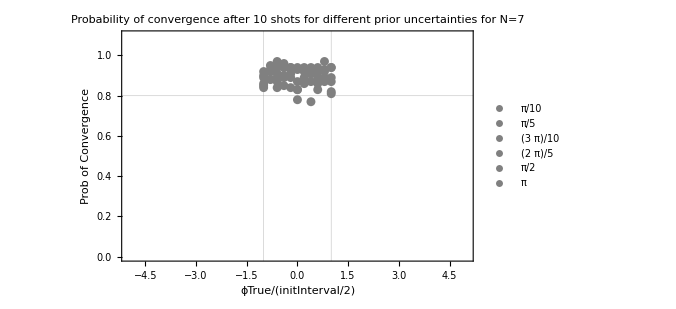

```mathematica
plot73=Show[ListPlot[plot[[1,1]],PlotStyle->{Gray, Dashed},PlotLabel->"Probability of convergence after 10 shots for different prior uncertainties for N=7",PlotLegends->{π/10},GridLines->{{-1,1},{0.8}}],ListPlot[plot[[1,2]],PlotStyle->{Gray,Dashed},PlotLegends->{(2π)/10}],ListPlot[plot[[1,3]],PlotStyle->{Gray, Dashed},PlotLegends->{(3π)/10}],ListPlot[plot[[1,4]],PlotStyle->{Gray,Dashed},PlotLegends->{(4π)/10}],ListPlot[plot[[1,5]],PlotStyle->{Gray,Dashed},PlotLegends->{(5π)/10}],ListPlot[plot[[1,6]],PlotStyle->{Gray,Dashed},PlotLegends->{π}],PlotRange->{{-5,5},{0,1.1}}, Frame->True,FrameLabel->{"ϕTrue/(initInterval/2)",Style["Prob of Convergence",Thick]}, FrameTicks->Automatic, AxesOrigin-> {0,0},ImageSize->{500, Automatic}]
```

```mathematica
(*Monochromatic plot with error bars*)
```

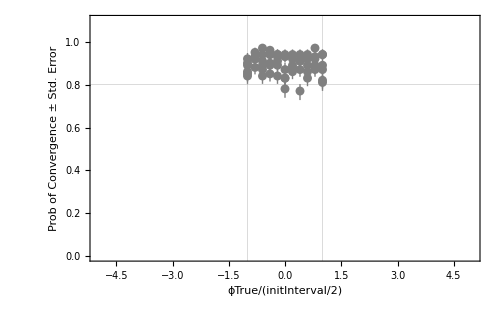

```mathematica
plot74=Show[ListPlot[plotStdError[[1,1]],PlotStyle->{Gray, Dashed},GridLines->{{-1,1},{0.8}}],ListPlot[plotStdError[[1,2]],PlotStyle->{Gray,Dashed}],ListPlot[plotStdError[[1,3]],PlotStyle->{Gray, Dashed}],ListPlot[plotStdError[[1,4]],PlotStyle->{Gray,Dashed}],ListPlot[plotStdError[[1,5]],PlotStyle->{Gray,Dashed}],ListPlot[plotStdError[[1,6]],PlotStyle->{Gray,Dashed}],PlotRange->{{-5,5},{0,1.1}}, Frame->True,FrameLabel->{"ϕTrue/(initInterval/2)",Style["Prob of Convergence ± Std. Error",Thick]}, FrameTicks->Automatic, AxesOrigin-> {0,0}]
```

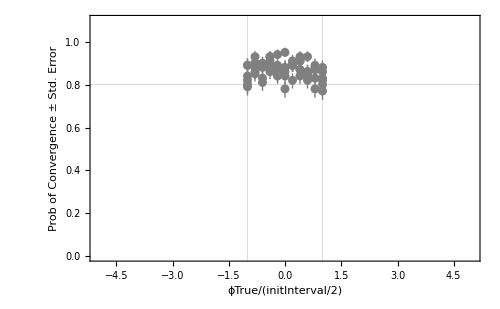
```mathematica
plot74=-Graphics-;
```

```mathematica
(*Average of all the points in the interval between -1,1*)
```

```mathematica
Average7
```

{0.9120.009,0.8950.009,0.8980.009,0.9010.009,0.9110.008,0.8590.010}

```mathematica
Average7=Around[Mean[Table[Average7[[n,1,1]],{n,1,Length[Data]}]],Mean[Table[Average7[[n,1,2]],{n,1,Length[Data]}]]]
```

0.8960.009

```mathematica
Average7=0.8960.009
```

0.8960.009

```mathematica
Average7=Around[Average7[[1]],Sqrt[Average7[[1]](1-Average7[[1]])/100]]
```

0.8960.031

### Nph = 10

#### Vary ϕ_true for Δ_initial= π/10, π/5, 3π/10, 2π/5, π/2, π and plot probability of convergence over 100 trials

```mathematica
Data=Table[
GridOfϕTrue=Table[
ntrial=100;
listOfPhaseEstimators=Table[
(*Set the number of photons*)
nph=10;
(*Start with some interval [-Delta,Delta]*)
initInterval =del*π/10;
(*Nature chooses the true value for the phase in the interval (unknown to the experimentalist)*)
ϕTrue =phitrue;
(*The experimentalist starts with center point Subscript[ϕ, 0]=0 and uncertainty Subscript[Δ, 0]=initInterval.*)
ϕtilde=0;
Δinit = initInterval;
nshots=10;
(*can variance and probability be calculated only once?*)
Clear[delta];
partialvariance=GetVariance[1,nph,delta];
(*The output is : {Subscript[P, 1] Subscript[(δϕ^2), 1],Subscript[P, 2] Subscript[(δϕ^2), 2],...}. Need to divide probability from variance*)
δϕsquared = Table[partialvariance[[n]]/Pm[[n]],{n,1,nph+1}];
phitilde=Table[
delta=Δinit;
(*list of P(m|ϕ) are the probabilities of getting outcome m*)
(*The experimentalist constructs an optimal one-shot input state for this uncertainty interval,*)
(*Plug N00N in N00N regime, Gaussian in Gaussian regime*)
If[Δinit*nph> 5,OptState=PlugGSBS[](*Print["Gaussian"];*),OptState=PlugN00NSBS[](*Print["N00N"];*)];
Table[OptState[[1,n,2]] += n ϕtilde,{n,1,nph+1}];
(*The experimentalist makes measurements m with the following probabilities*)
prob=Re[listOfPmϕ/.OptState];
(*This is the probability distribution that nature has/knows*)
prob2=Re[listOfPmϕ/.OptState/.ϕ->ϕTrue-ϕtilde];
probDistrib = Accumulate[prob2[[1]]];
(*mRand is a uniformly distributed random real between 0 and 1*)
SeedRandom[];
mRand=Random[];
(*if mRand<probDistrib[[m]], outcome m occured experimentally*)
outcomeOccured =Max[Table[If[mRand>probDistrib[[m]],m,0],{m,1,nph+1}]]+1;
Indvariance=δϕsquared/.OptState;
variance=Indvariance[[1,outcomeOccured]];
Δnext = √(12*variance);
(*varianceDistrib[[1,outcomeOccured]]*)
phaseEstimators=listOfϕ1/.OptState;
(*and the following phase estimator*)
ϕtilde+=phaseEstimators[[1,outcomeOccured]];
(*Input state of the second shot gets phase shifted by this phase above*)
Δinit=Δnext;
,{shot,1, nshots}];
{Δnext,ϕtilde},{trial,1,ntrial}];
(*finds the mean of the varRatio over ntrials for a particular Δini*)
{ϕTrue,ϕTrue/(initInterval/2),listOfPhaseEstimators},{phitrue,-del*π/20,del*π/20,del*π/100}];
IfConverge=MatrixForm[Table[ProbOfTrue=0;{GridOfϕTrue[[n,1]],GridOfϕTrue[[n,2]],Table[If[GridOfϕTrue[[n,3,trial,2]]>(GridOfϕTrue[[n,1]]-GridOfϕTrue[[n,3,trial,1]]/2)&&GridOfϕTrue[[n,3,trial,2]]<(GridOfϕTrue[[n,1]]+GridOfϕTrue[[n,3,trial,1]]/2),ProbOfTrue+=1;GridOfϕTrue[[n,3,trial,2]],GridOfϕTrue[[n,3,trial,2]](*{GridOfϕTrue[[n,3,trial,2]],True}{GridOfϕTrue[[n,3,trial,2]],False}*)],{trial,1,ntrial}],N[ProbOfTrue/ntrial],del π/10},{n,1,Length[GridOfϕTrue]}]];
IfConverge1 = MatrixForm[Drop[IfConverge[[1]],None,{3}]],{del,{1,2,3,4,5,10}}];
```

```mathematica
(*Subscript[ϕ, true],Subscript[ϕ, true]/(Δ/2), probability of converging, Subscript[Δ, initial] *)
```

```mathematica
Data
```

{(-π/20 | -1 | 0.71 | π/10
-π/25 | -4/5 | 0.9 | π/10
-(3 π)/100 | -3/5 | 0.82 | π/10
-π/50 | -2/5 | 0.87 | π/10
-π/100 | -1/5 | 0.91 | π/10
0 | 0 | 0.9 | π/10
π/100 | 1/5 | 0.93 | π/10
π/50 | 2/5 | 0.9 | π/10
(3 π)/100 | 3/5 | 0.94 | π/10
π/25 | 4/5 | 0.91 | π/10
π/20 | 1 | 0.81 | π/10),(-π/10 | -1 | 0.83 | π/5
-(2 π)/25 | -4/5 | 0.9 | π/5
-(3 π)/50 | -3/5 | 0.9 | π/5
-π/25 | -2/5 | 0.93 | π/5
-π/50 | -1/5 | 0.85 | π/5
0 | 0 | 0.86 | π/5
π/50 | 1/5 | 0.89 | π/5
π/25 | 2/5 | 0.94 | π/5
(3 π)/50 | 3/5 | 0.93 | π/5
(2 π)/25 | 4/5 | 0.89 | π/5
π/10 | 1 | 0.79 | π/5),(-(3 π)/20 | -1 | 0.95 | (3 π)/10
-(3 π)/25 | -4/5 | 0.91 | (3 π)/10
-(9 π)/100 | -3/5 | 0.81 | (3 π)/10
-(3 π)/50 | -2/5 | 0.84 | (3 π)/10
-(3 π)/100 | -1/5 | 0.88 | (3 π)/10
0 | 0 | 0.9 | (3 π)/10
(3 π)/100 | 1/5 | 0.93 | (3 π)/10
(3 π)/50 | 2/5 | 0.9 | (3 π)/10
(9 π)/100 | 3/5 | 0.91 | (3 π)/10
(3 π)/25 | 4/5 | 0.93 | (3 π)/10
(3 π)/20 | 1 | 0.85 | (3 π)/10),(-π/5 | -1 | 0.91 | (2 π)/5
-(4 π)/25 | -4/5 | 0.94 | (2 π)/5
-(3 π)/25 | -3/5 | 0.92 | (2 π)/5
-(2 π)/25 | -2/5 | 0.77 | (2 π)/5
-π/25 | -1/5 | 0.87 | (2 π)/5
0 | 0 | 0.77 | (2 π)/5
π/25 | 1/5 | 0.89 | (2 π)/5
(2 π)/25 | 2/5 | 0.87 | (2 π)/5
(3 π)/25 | 3/5 | 0.92 | (2 π)/5
(4 π)/25 | 4/5 | 0.96 | (2 π)/5
π/5 | 1 | 0.86 | (2 π)/5),(-π/4 | -1 | 0.94 | π/2
-π/5 | -4/5 | 0.88 | π/2
-(3 π)/20 | -3/5 | 0.93 | π/2
-π/10 | -2/5 | 0.86 | π/2
-π/20 | -1/5 | 0.89 | π/2
0 | 0 | 0.87 | π/2
π/20 | 1/5 | 0.97 | π/2
π/10 | 2/5 | 0.85 | π/2
(3 π)/20 | 3/5 | 0.91 | π/2
π/5 | 4/5 | 0.89 | π/2
π/4 | 1 | 0.92 | π/2),(-π/2 | -1 | 0.87 | π
-(2 π)/5 | -4/5 | 0.9 | π
-(3 π)/10 | -3/5 | 0.88 | π
-π/5 | -2/5 | 0.86 | π
-π/10 | -1/5 | 0.81 | π
0 | 0 | 0.84 | π
π/10 | 1/5 | 0.81 | π
π/5 | 2/5 | 0.83 | π
(3 π)/10 | 3/5 | 0.89 | π
(2 π)/5 | 4/5 | 0.89 | π
π/2 | 1 | 0.9 | π)}

```mathematica
(*y -> probability of converging after 20 shots*)
```

```mathematica
y=MatrixForm[Table[Table[Data[[del,1,n,3]],{n,1, Length[Data[[1,1]]]}],{del,1, Length[Data]}]]
```

(0.71 | 0.9 | 0.82 | 0.87 | 0.91 | 0.9 | 0.93 | 0.9 | 0.94 | 0.91 | 0.81
0.83 | 0.9 | 0.9 | 0.93 | 0.85 | 0.86 | 0.89 | 0.94 | 0.93 | 0.89 | 0.79
0.95 | 0.91 | 0.81 | 0.84 | 0.88 | 0.9 | 0.93 | 0.9 | 0.91 | 0.93 | 0.85
0.91 | 0.94 | 0.92 | 0.77 | 0.87 | 0.77 | 0.89 | 0.87 | 0.92 | 0.96 | 0.86
0.94 | 0.88 | 0.93 | 0.86 | 0.89 | 0.87 | 0.97 | 0.85 | 0.91 | 0.89 | 0.92
0.87 | 0.9 | 0.88 | 0.86 | 0.81 | 0.84 | 0.81 | 0.83 | 0.89 | 0.89 | 0.9)

```mathematica
(*Standard error for sample proportion of success p is √(p(1-p)/100)*)
```

```mathematica
z=MatrixForm[Table[Table[Around[Data[[del,1,n,3]],√(((Data[[del,1,n,3]])(1-Data[[del,1,n,3]]))/ntrial)],{n,1, Length[Data[[1,1]]]}],{del,1, Length[Data]}]]
```

(0.710.05 | 0.9000.030 | 0.820.04 | 0.8700.034 | 0.9100.029 | 0.9000.030 | 0.9300.026 | 0.9000.030 | 0.9400.024 | 0.9100.029 | 0.810.04
0.830.04 | 0.9000.030 | 0.9000.030 | 0.9300.026 | 0.850.04 | 0.8600.035 | 0.8900.031 | 0.9400.024 | 0.9300.026 | 0.8900.031 | 0.790.04
0.9500.022 | 0.9100.029 | 0.810.04 | 0.840.04 | 0.8800.032 | 0.9000.030 | 0.9300.026 | 0.9000.030 | 0.9100.029 | 0.9300.026 | 0.850.04
0.9100.029 | 0.9400.024 | 0.9200.027 | 0.770.04 | 0.8700.034 | 0.770.04 | 0.8900.031 | 0.8700.034 | 0.9200.027 | 0.9600.020 | 0.8600.035
0.9400.024 | 0.8800.032 | 0.9300.026 | 0.8600.035 | 0.8900.031 | 0.8700.034 | 0.9700.017 | 0.850.04 | 0.9100.029 | 0.8900.031 | 0.9200.027
0.8700.034 | 0.9000.030 | 0.8800.032 | 0.8600.035 | 0.810.04 | 0.840.04 | 0.810.04 | 0.830.04 | 0.8900.031 | 0.8900.031 | 0.9000.030)

```mathematica
Average10=Table[MatrixForm[Mean[z[[1,n]]]],{n,1,Length[Data]}]
```

{0.8730.010,0.8830.010,0.8920.009,0.8800.010,0.9010.009,0.8620.010}

```mathematica
(*x -> ϕTrue/(Δ/2)*)
```

```mathematica
x=MatrixForm[Table[Table[Data[[del,1,n,2]],{n,1, Length[Data[[1,1]]]}],{del,1, Length[Data]}]]
```

(-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1)

```mathematica
plot = MatrixForm[Table[Thread[{x[[1,n]],y[[1,n]]}],{n,1,Length[Data]}]]
```

((-1
0.71) | (-4/5
0.9) | (-3/5
0.82) | (-2/5
0.87) | (-1/5
0.91) | (0
0.9) | (1/5
0.93) | (2/5
0.9) | (3/5
0.94) | (4/5
0.91) | (1
0.81)
(-1
0.83) | (-4/5
0.9) | (-3/5
0.9) | (-2/5
0.93) | (-1/5
0.85) | (0
0.86) | (1/5
0.89) | (2/5
0.94) | (3/5
0.93) | (4/5
0.89) | (1
0.79)
(-1
0.95) | (-4/5
0.91) | (-3/5
0.81) | (-2/5
0.84) | (-1/5
0.88) | (0
0.9) | (1/5
0.93) | (2/5
0.9) | (3/5
0.91) | (4/5
0.93) | (1
0.85)
(-1
0.91) | (-4/5
0.94) | (-3/5
0.92) | (-2/5
0.77) | (-1/5
0.87) | (0
0.77) | (1/5
0.89) | (2/5
0.87) | (3/5
0.92) | (4/5
0.96) | (1
0.86)
(-1
0.94) | (-4/5
0.88) | (-3/5
0.93) | (-2/5
0.86) | (-1/5
0.89) | (0
0.87) | (1/5
0.97) | (2/5
0.85) | (3/5
0.91) | (4/5
0.89) | (1
0.92)
(-1
0.87) | (-4/5
0.9) | (-3/5
0.88) | (-2/5
0.86) | (-1/5
0.81) | (0
0.84) | (1/5
0.81) | (2/5
0.83) | (3/5
0.89) | (4/5
0.89) | (1
0.9))

```mathematica
plotStdError= MatrixForm[Table[Thread[{x[[1,n]],z[[1,n]]}],{n,1,Length[Data]}]]
```

((-1
0.710.05) | (-4/5
0.9000.030) | (-3/5
0.820.04) | (-2/5
0.8700.034) | (-1/5
0.9100.029) | (0
0.9000.030) | (1/5
0.9300.026) | (2/5
0.9000.030) | (3/5
0.9400.024) | (4/5
0.9100.029) | (1
0.810.04)
(-1
0.830.04) | (-4/5
0.9000.030) | (-3/5
0.9000.030) | (-2/5
0.9300.026) | (-1/5
0.850.04) | (0
0.8600.035) | (1/5
0.8900.031) | (2/5
0.9400.024) | (3/5
0.9300.026) | (4/5
0.8900.031) | (1
0.790.04)
(-1
0.9500.022) | (-4/5
0.9100.029) | (-3/5
0.810.04) | (-2/5
0.840.04) | (-1/5
0.8800.032) | (0
0.9000.030) | (1/5
0.9300.026) | (2/5
0.9000.030) | (3/5
0.9100.029) | (4/5
0.9300.026) | (1
0.850.04)
(-1
0.9100.029) | (-4/5
0.9400.024) | (-3/5
0.9200.027) | (-2/5
0.770.04) | (-1/5
0.8700.034) | (0
0.770.04) | (1/5
0.8900.031) | (2/5
0.8700.034) | (3/5
0.9200.027) | (4/5
0.9600.020) | (1
0.8600.035)
(-1
0.9400.024) | (-4/5
0.8800.032) | (-3/5
0.9300.026) | (-2/5
0.8600.035) | (-1/5
0.8900.031) | (0
0.8700.034) | (1/5
0.9700.017) | (2/5
0.850.04) | (3/5
0.9100.029) | (4/5
0.8900.031) | (1
0.9200.027)
(-1
0.8700.034) | (-4/5
0.9000.030) | (-3/5
0.8800.032) | (-2/5
0.8600.035) | (-1/5
0.810.04) | (0
0.840.04) | (1/5
0.810.04) | (2/5
0.830.04) | (3/5
0.8900.031) | (4/5
0.8900.031) | (1
0.9000.030))

```mathematica
(*For different values of quantity A = ϕTrue/(initInterval/2) ranging from -1, 1 in increments of 1/5, we plot the probability of convergence after 10 shots computed over 100 trials for N=3 photons*)
```

```mathematica
(*color plot distinguishing different Δinitials*)
```

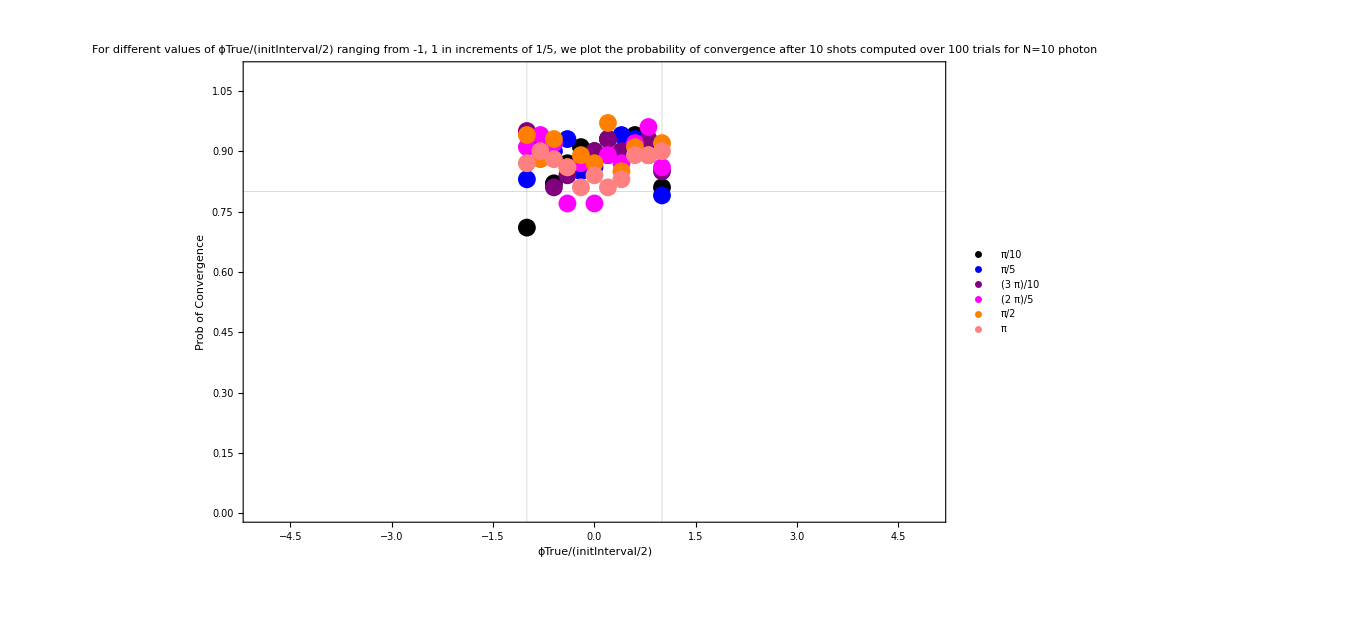

```mathematica
plot101=Show[ListPlot[plot[[1,1]],PlotStyle->{Black, Dashed},PlotLabel->"For different values of ϕTrue/(initInterval/2) ranging from -1, 1 in increments of 1/5, we plot the probability of convergence after 10 shots computed over 100 trials for N=10 photon",PlotLegends->{π/10},GridLines->{{-1,1},{0.8}}],ListPlot[plot[[1,2]],PlotStyle->{Blue,Dashed},PlotLegends->{(2π)/10}],ListPlot[plot[[1,3]],PlotStyle->{Purple, Dashed},PlotLegends->{(3π)/10}],ListPlot[plot[[1,4]],PlotStyle->{Magenta,Dashed},PlotLegends->{(4π)/10}],ListPlot[plot[[1,5]],PlotStyle->{Orange,Dashed},PlotLegends->{(5π)/10}],ListPlot[plot[[1,6]],PlotStyle->{Pink,Dashed},PlotLegends->{π}],PlotRange->{{-5,5},{0,1.1}}, Frame->True,FrameLabel->{"ϕTrue/(initInterval/2)",Style["Prob of Convergence",Thick]}, FrameTicks->Automatic, AxesOrigin-> {0,0},ImageSize->{1000, Automatic}]
```

```mathematica
(*color plot with error bars*)
```

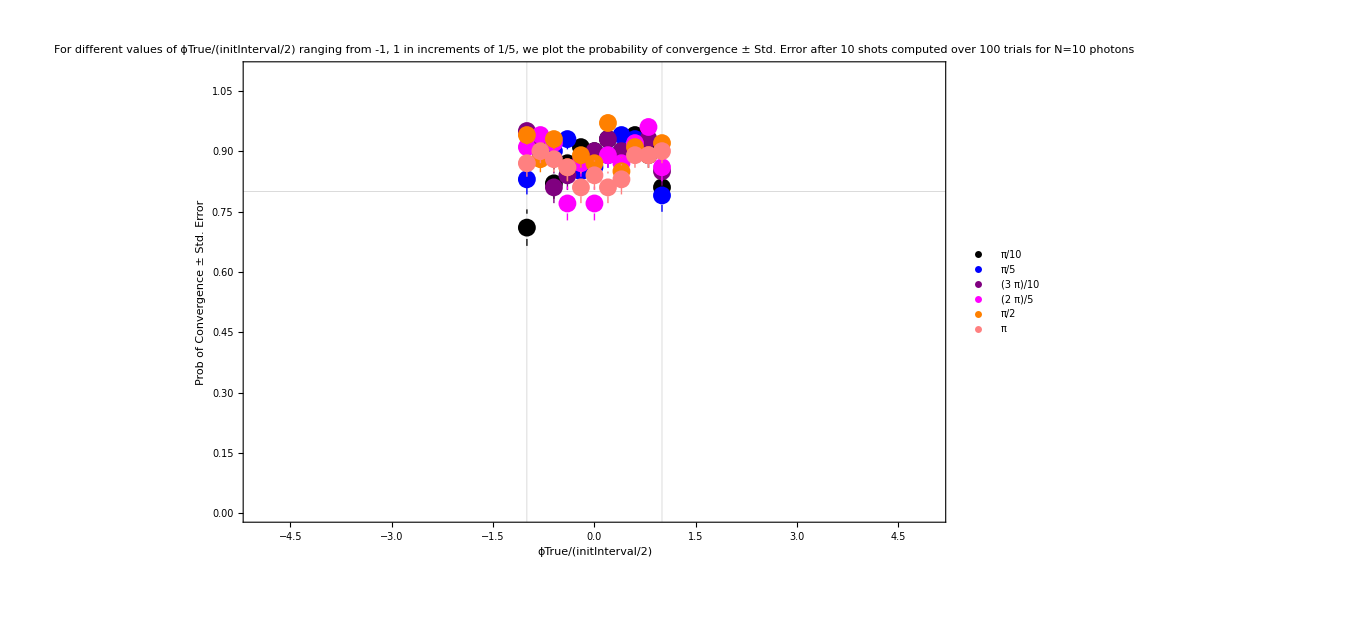

```mathematica
plot102=Show[ListPlot[plotStdError[[1,1]],PlotStyle->{Black, Dashed},PlotLabel->"For different values of ϕTrue/(initInterval/2) ranging from -1, 1 in increments of 1/5, we plot the probability of convergence ± Std. Error after 10 shots computed over 100 trials for N=10 photons",PlotLegends->{π/10},GridLines->{{-1,1},{0.8}}],ListPlot[plotStdError[[1,2]],PlotStyle->{Blue,Dashed},PlotLegends->{(2π)/10}],ListPlot[plotStdError[[1,3]],PlotStyle->{Purple, Dashed},PlotLegends->{(3π)/10}],ListPlot[plotStdError[[1,4]],PlotStyle->{Magenta,Dashed},PlotLegends->{(4π)/10}],ListPlot[plotStdError[[1,5]],PlotStyle->{Orange,Dashed},PlotLegends->{(5π)/10}],ListPlot[plotStdError[[1,6]],PlotStyle->{Pink,Dashed},PlotLegends->{π}],PlotRange->{{-5,5},{0,1.1}}, Frame->True,FrameLabel->{"ϕTrue/(initInterval/2)",Style["Prob of Convergence ± Std. Error",Thick]}, FrameTicks->Automatic, AxesOrigin-> {0,0},ImageSize->{1000, Automatic}]
```

```mathematica
(*Monochromatic plot distinguishing different N*)
```

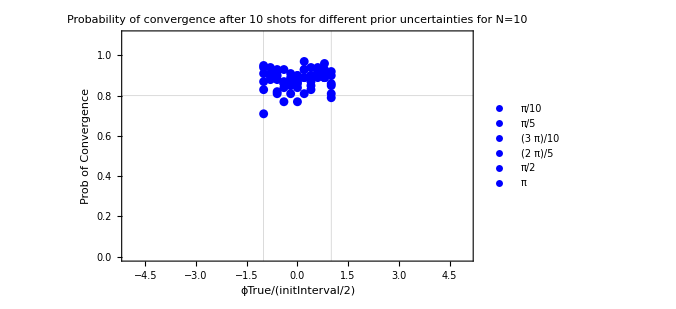

```mathematica
plot103=Show[ListPlot[plot[[1,1]],PlotStyle->{Blue, Dashed},PlotLabel->"Probability of convergence after 10 shots for different prior uncertainties for N=10",PlotLegends->{π/10},GridLines->{{-1,1},{0.8}}],ListPlot[plot[[1,2]],PlotStyle->{Blue,Dashed},PlotLegends->{(2π)/10}],ListPlot[plot[[1,3]],PlotStyle->{Blue, Dashed},PlotLegends->{(3π)/10}],ListPlot[plot[[1,4]],PlotStyle->{Blue,Dashed},PlotLegends->{(4π)/10}],ListPlot[plot[[1,5]],PlotStyle->{Blue,Dashed},PlotLegends->{(5π)/10}],ListPlot[plot[[1,6]],PlotStyle->{Blue,Dashed},PlotLegends->{π}],PlotRange->{{-5,5},{0,1.1}}, Frame->True,FrameLabel->{"ϕTrue/(initInterval/2)",Style["Prob of Convergence",Thick]}, FrameTicks->Automatic, AxesOrigin-> {0,0},ImageSize->{500, Automatic}]
```

```mathematica
(*Monochromatic plot with error bars*)
```

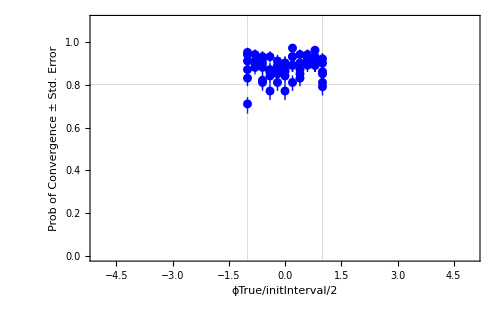

```mathematica
plot104=Show[ListPlot[plotStdError[[1,1]],PlotStyle->{Blue, Dashed},GridLines->{{-1,1},{0.8}}],ListPlot[plotStdError[[1,2]],PlotStyle->{Blue,Dashed}],ListPlot[plotStdError[[1,3]],PlotStyle->{Blue, Dashed}],ListPlot[plotStdError[[1,4]],PlotStyle->{Blue,Dashed}],ListPlot[plotStdError[[1,5]],PlotStyle->{Blue,Dashed}],ListPlot[plotStdError[[1,6]],PlotStyle->{Blue,Dashed}],PlotRange->{{-5,5},{0,1.1}}, Frame->True,FrameLabel->{"ϕTrue/initInterval/2",Style["Prob of Convergence ± Std. Error",Thick]}, FrameTicks->Automatic, AxesOrigin-> {0,0}]
```

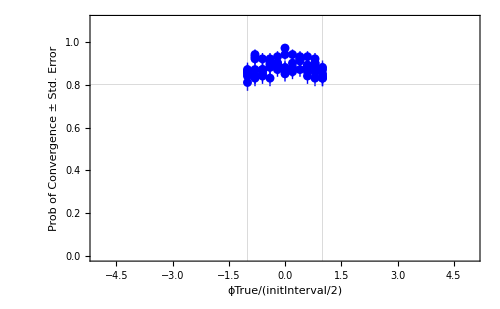
```mathematica
plot104=-Graphics-;
```

```mathematica
(*Average of all the points in the interval between -1,1*)
```

```mathematica
Average10
```

{0.8730.010,0.8830.010,0.8920.009,0.8800.010,0.9010.009,0.8620.010}

```mathematica
Average10=Around[Mean[Table[Average10[[n,1,1]],{n,1,Length[Data]}]],Mean[Table[Average10[[n,1,2]],{n,1,Length[Data]}]]]
```

0.8820.010

```mathematica
Average10=0.8820.010
```

0.8820.010

```mathematica
Average10=Around[Average10[[1]],Sqrt[Average10[[1]](1-Average10[[1]])/100]]
```

0.8820.032

### Compare N=3,5,7,10

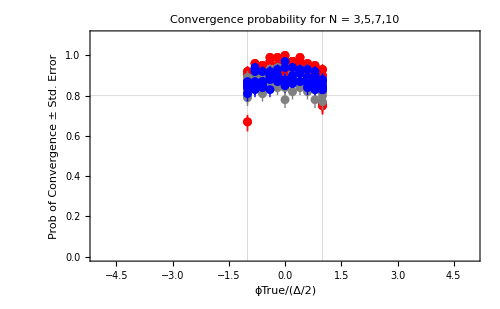

```mathematica
Show[plot34,plot54,plot74,plot104,FrameLabel->{{Style["Prob of Convergence ± Std. Error",Thickness[Large]],None},{HoldForm["\!\(\*FractionBox[\(ϕTrue\), \(Δ/2\)]\)"],None}},PlotLabel->"Convergence probability for N = 3,5,7,10", LabelStyle->{GrayLevel[0]}]
```

```mathematica
plot104=Show[ListPlot[plotStdError[[1,1]],PlotStyle->{Blue, Dashed},GridLines->{{-1,1},{0.8}}],ListPlot[plotStdError[[1,2]],PlotStyle->{Blue,Dashed}],ListPlot[plotStdError[[1,3]],PlotStyle->{Blue, Dashed}],ListPlot[plotStdError[[1,4]],PlotStyle->{Blue,Dashed},PlotLegends->Placed[{"N=10"},{Right,Center}]],ListPlot[plotStdError[[1,5]],PlotStyle->{Blue,Dashed}],ListPlot[plotStdError[[1,6]],PlotStyle->{Blue,Dashed}],PlotRange->{{-1.5,1.5},{0.6,1.1}}, Frame->True,FrameLabel->{"ϕTrue/initInterval/2",Style["Prob of Convergence ± Std. Error",Thick]}, FrameTicks->Automatic, AxesOrigin-> {0,0}]
```

```mathematica
AverageConvergence={Average3,Average5,Average7,Average10}
```

{0.9120.028,0.8950.031,0.8960.031,0.8820.032}

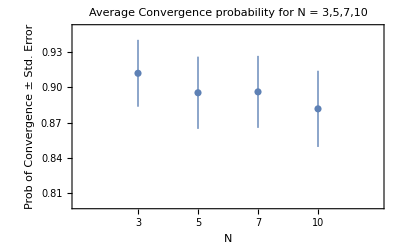

```mathematica
ListPlot[AverageConvergence,PlotRange->{{-0,5},{0.8,0.95}},PlotLabel->"Average Convergence probability for N = 3,5,7,10", Frame->True,FrameLabel-> {"N","Prob of Convergence ± Std. Error"},FrameTicks->{{Automatic,Automatic},{{{1,"3"},{2,"5"},{3,"7"},{4,"10"}},Automatic}}]
```

```mathematica
AverageConvergence2=MatrixForm[{{Average3[[1]], Average3[[2]]},{Average5[[1]], Average5[[2]]},{Average7[[1]], Average7[[2]]},{Average10[[1]], Average10[[2]]}}]
```

(0.900303 | 0.0286173
0.877727 | 0.0320042
0.867879 | 0.0333102
0.881515 | 0.03184)

```mathematica
Mean[AverageConvergence2[[1]]]
```

{0.881856,0.0314429}

#### Compare average convergence probability of adaptive with semi-adaptive

```mathematica
(*Semi-Adaptive*)
```

```mathematica
AverageConvergenceSA={0.9000.029,0.8780.032,0.8680.033,0.8820.032}
```

{0.9000.029,0.8780.032,0.8680.033,0.8820.032}

```mathematica
(*Adaptive*)
```

```mathematica
AverageConvergenceA={0.9120.028,0.8950.031,0.8960.031,0.8820.032}
```

{0.9120.028,0.8950.031,0.8960.031,0.8820.032}

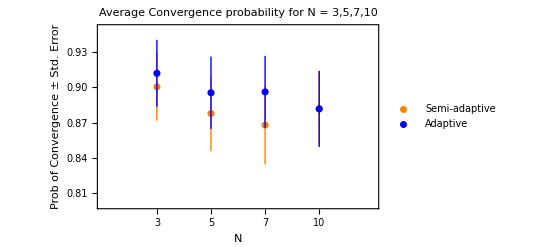

```mathematica
Show[ListPlot[AverageConvergenceSA, PlotStyle->Orange, PlotLegends->{"Semi-adaptive"}],ListPlot[AverageConvergenceA ,PlotStyle->Blue,PlotLegends->{"Adaptive"}],PlotRange->{{-0,5},{0.8,0.95}},PlotLabel->"Average Convergence probability for N = 3,5,7,10", Frame->True,FrameLabel-> {"N","Prob of Convergence ± Std. Error"},AxesOrigin->{0,0},FrameTicks->{{Automatic,Automatic},{{{1,"3"},{2,"5"},{3,"7"},{4,"10"}},Automatic}}]
```